# HTMEK Kinetics Analysis v.1.9

## Craig Markin and Daniel Mokhtari Herschlag and Fordyce Labs

## Analysis and plotting functions:

The hidden cell below contains all the necessary functions for analyzing HTMEK kinetic and inhibition data. Evaluate this cell first.

```mathematica
importstandardcurve[path_]:=Module[{dataIN,parsed,standardcurvedata},

dataIN=Import[path,"Data"];

(* iterating n from 2 drops the .csv header text *)
parsed=Table[{dataIN[[n,2]],dataIN[[n,3]],dataIN[[n,9]],dataIN[[n,13]],dataIN[[n,8]],dataIN[[n,6]]},{n,2,Length[dataIN]}];

(* convert [] brackets to curly brackets {} *)
standardcurvedata=Table[{StringDelete[parsed[[n,1]],"\""],ToExpression[StringReplace[StringReplace[parsed[[n,2]],"("->"{"],")"->"}"]],parsed[[n,3]],parsed[[n,4]],Partition[Riffle[ToExpression[StringReplace[StringReplace[parsed[[n,5]],"["->"{"],"]"->"}"]],ToExpression[StringReplace[StringReplace[parsed[[n,6]],"["->"{"],"]"->"}"]]],2]},{n,1,Length[parsed]}]

]

replaceBrackets[stringList_]:=Module[{test1,stringReplaced},

stringReplaced=If[StringQ[stringList]==True&&(StringContainsQ[stringList,"["]==True||StringContainsQ[stringList,"("]==True),ToExpression[StringReplace[stringList,{"["->"{","("->"{","]"->"}",")"->"}"}]],stringList]

]

replaceBracketsBack[in_]:=Return[If[ListQ[in]==True,

StringReplace[ToString[DecimalForm[in]],{"{"->"[","}"->"]"}],

in]]

makeProgressCurvePlotRFU[timeData_,medianIntensityData_,rate_,intercept_,pointsUsed_,standardCurveSlope_,standardCurveIntercept_,substrateConc_]:=Module[{data,noPointsFit,xmin,ymin,padding,xscale,yscale},

data=Partition[Riffle[timeData,medianIntensityData],2];

noPointsFit=Length[pointsUsed];

(* set plotting and padding values *)
xmin=Last[data][[1]];
ymin=Last[data][[2]];

padding=50;

xscale=1.1;
yscale=1.4;

Overlay[{

ListPlot[data,ImagePadding->padding,PlotRange->{{-200,xmin*xscale},{0,ymin*yscale}},PlotStyle->Directive[GrayLevel[0.4],PointSize[0.015]],Frame->{False,True,True,False},FrameStyle->{Black,Black,Black,Black},FrameTicks->All,Axes->False,FrameLabel->{"Time (s)","RFU","Time (s)","RFU"},ImageSize->450,GridLines->{None,{standardCurveSlope*substrateConc+standardCurveIntercept,standardCurveIntercept}},GridLinesStyle->Directive[Darker[Red],Dashed],Epilog->{Inset[Style[StringJoin["[S]=",ToString[Round[substrateConc]],"uM"]],{xmin/1.25,ymin*yscale/4}]}],

Plot[rate*time+intercept,{time,-200,data[[noPointsFit,1]]+150.},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,data[[noPointsFit,1]]+150.},{0,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],

Plot[rate*time+intercept,{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{0,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.4]]],

ListPlot[data[[1;;noPointsFit]],PlotRange->{{-200,data[[noPointsFit,1]]+150.},{0,ymin*yscale}},ImagePadding->padding,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Darker[ColorData[3,"ColorList"][[1+1]]],Black,Black,Darker[ColorData[3,"ColorList"][[1+1]]]},Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]]],PlotStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]],PointSize[0.03],Opacity[0.8]],FrameLabel->{"Time (s)","RFU","Time (s)","RFU"},ImageSize->450,GridLines->{None,{65535.}},GridLinesStyle->Directive[GrayLevel[0.5],Dashed]]

}]]

makeProgressCurvePlot[timeData_,progressCurve_,rate_,intercept_,pointsUsed_,substrateConc_,expFitModel_]:=Module[{data,noPointsFit,xmin,ymin,padding,xscale,yscale,firstPointY},

(*data=Partition[Riffle[timeData,progressCurve],2];*)

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

noPointsFit=Length[pointsUsed];

(* set plotting and padding values *)
xmin=Last[data][[1]];
ymin=Last[data][[2]];

padding=50;

xscale=1.1;
yscale=1.4;

firstPointY=Min[data[[All,2]]]-0.5;

Overlay[{

ListPlot[data,ImagePadding->padding,PlotRange->{{-200,xmin*xscale},{firstPointY,ymin*yscale}},PlotStyle->Directive[GrayLevel[0.4],PointSize[0.015]],Frame->{False,True,True,False},FrameStyle->{Black,Black,Black,Black},FrameTicks->All,Axes->False,FrameLabel->{"Time (s)","Product (uM)","Time (s)","Product (uM)"},ImageSize->450,GridLines->{None,{substrateConc}},GridLinesStyle->Directive[Darker[Red],Dashed],Epilog->{Inset[Style[StringJoin["[S]=",ToString[Round[substrateConc]],"uM"]],{xmin/1.25,ymin*yscale/4}]}],

Plot[rate*time+intercept,{time,-200,data[[noPointsFit,1]]+150.},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,data[[noPointsFit,1]]+150.},{firstPointY,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],

Plot[rate*time+intercept,{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{firstPointY,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.4]]],

If[Length[expFitModel]==4,Plot[expFitModel[time],{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{firstPointY,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,Darker[Hue[1*0.1]]]],""],

ListPlot[data[[1;;noPointsFit]],PlotRange->{{-200,data[[noPointsFit,1]]+150.},{firstPointY,ymin*yscale}},ImagePadding->padding,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{Darker[ColorData[3,"ColorList"][[1+1]]],Black,Black,Darker[ColorData[3,"ColorList"][[1+1]]]},Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]]],PlotStyle->Directive[Darker[ColorData[3,"ColorList"][[1+1]]],PointSize[0.03],Opacity[0.8]],FrameLabel->{"Time (s)","RFU","Time (s)","RFU"},ImageSize->450,GridLines->{None,{65535.}},GridLinesStyle->Directive[GrayLevel[0.5],Dashed]]

}]]

makeProgressCurvePlotPBP[timeData_,turnoverData_,rate_,intercept_,pointsUsed_,substrateConc_,PBPconc_,coplotExp_,expFitModel_]:=Module[{data,noPointsFit,xmin,ymin,padding,xscale,yscale,kobstest,yPlotRangeMin},

data=Sort[Partition[Riffle[timeData,turnoverData],2],#1[[1]]<#2[[1]]&];

noPointsFit=Length[pointsUsed];

(* set plotting and padding values *)
xmin=Last[data][[1]];
(*ymin=Last[data][[2]];*)

ymin=If[First[Sort[data,#1[[2]]>#2[[2]]&]][[2]]≤60.0,First[Sort[data,#1[[2]]>#2[[2]]&]][[2]],60.0];

yPlotRangeMin=If[Last[Sort[data,#1[[2]]>#2[[2]]&]][[2]]≥0,-0.1,Last[Sort[data,#1[[2]]>#2[[2]]&]][[2]]*1.5];

padding=50;

xscale=1.1;
yscale=1.4;

(*kobstest=kobs/.expFitModel[[1,2]];

Print[kobstest];*)

If[noPointsFit≥1,Overlay[{

ListPlot[data,ImagePadding->padding,PlotRange->{{-200,xmin*xscale},{yPlotRangeMin,ymin*yscale}},PlotStyle->Directive[GrayLevel[0.4],PointSize[0.015]],Frame->{False,True,True,False},FrameStyle->{Black,Black,Black,Black},FrameTicks->All,Axes->False,FrameLabel->{"Time (s)","[Pi]","Time (s)","[Pi]"},ImageSize->450,GridLines->{None,{substrateConc,PBPconc}},GridLinesStyle->Directive[Darker[Red],Dashed],Epilog->{Inset[Style[StringJoin["[S]=",ToString[Round[substrateConc]],"uM"]],Scaled[{0.8,0.4}]]}],

Plot[rate*time+intercept,{time,-200,data[[noPointsFit,1]]+150.},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,data[[noPointsFit,1]]+150.},{yPlotRangeMin,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.5]]],

Plot[rate*time+intercept,{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{yPlotRangeMin,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.4]]],

If[Length[expFitModel]==4,Plot[expFitModel[time],{time,-200,xmin*xscale},ImagePadding->padding,Frame->{False,False,False,False},Axes->False,PlotRange->{{-200,xmin*xscale},{yPlotRangeMin,ymin*yscale}},ImageSize->450,PlotStyle->Directive[Dashed,GrayLevel[0.5]]],""],

ListPlot[data[[1;;noPointsFit]],PlotRange->{{-200,data[[noPointsFit,1]]+150.},{yPlotRangeMin,ymin*yscale}},ImagePadding->padding,Frame->{True,False,False,True},FrameTicks->All,FrameStyle->{GrayLevel[0.5],Black,Black,GrayLevel[0.5]},Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Darker[Red]],PlotStyle->Directive[GrayLevel[0.5],PointSize[0.03],Opacity[0.8]],FrameLabel->{"Time (s)","[Pi]","Time (s)","[Pi]"},ImageSize->450,GridLines->{None,{65535.}},GridLinesStyle->Directive[Darker[Red],Dashed]]

}]]]

isotherm[kd_,ptot_,scale_,offset_,x_]:=(0.5*((kd+x+ptot)-((kd+x+ptot)^2-(4*x*ptot))^0.5))*scale+offset

inverseIsotherm[kd_,ptot_,scale_,offset_,intensity_]:=(1. (1. intensity^2-2. intensity offset+1. offset^2-1. intensity kd scale+1. kd offset scale-1. intensity ptot scale+1. offset ptot scale))/(scale (intensity-1. offset-1. ptot scale))

inverseIsothermList[kd_,ptot_,scale_,offset_,intensities_]:=Table[intensity=intensities[[n]];(1. (1. intensity^2-2. intensity offset+1. offset^2-1. intensity kd scale+1. kd offset scale-1. intensity ptot scale+1. offset ptot scale))/(scale (intensity-1. offset-1. ptot scale)),{n,1,Length[intensities]}]

regenerateProgressCurve[timeData_,medianIntensityData_,standardCurveParams_,sensorConc_]:=Module[{data},

data=Partition[Riffle[timeData,medianIntensityData],2];

Table[{data[[n,1]],inverseIsotherm[standardCurveParams⟦1⟧,standardCurveParams⟦2⟧,standardCurveParams⟦3⟧,standardCurveParams⟦4⟧,data[[n,2]]]},{n,1,Length[data]}]

]

makePBPcurvePlot[standardCurveParams_,standardCurveData_]:=Show[

ListPlot[standardCurveData,PlotRange->All,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[P_i] (uM)","PBP Intensity"},ImageSize->450,ImagePadding->{{50,50},{50,1}},PlotStyle->Directive[Darker[Cyan],PointSize[0.02]]],

Plot[isotherm[standardCurveParams[[1]],standardCurveParams[[2]],standardCurveParams[[3]],standardCurveParams[[4]],Pi],{Pi,0,160},PlotRange->{0,All},PlotStyle->Directive[Darker[Cyan]],Frame->True,Axes->False,ImageSize->450,FrameStyle->Black]

]

linearFitWalkingProgressCurve[timeData_,progressCurve_]:=Module[{data,linFits},

(* n.b. had to add Select because 1 point is expressed in scientific notation in input csv, and doesn't parse properly *)
data=Select[Partition[Riffle[timeData,progressCurve],2],Head[#[[2]]]==Real&];

linFits=Table[{n,LinearModelFit[data[[1;;n]],x,x]},{n,2,Length[data]}];

Table[{linFits[[n,1]],linFits[[n,2,1,2,2]],linFits[[n,2,1,2,1]],linFits[[n,2]]},{n,1,Length[linFits]}]

]

optimizeLinFit[timeData_,progressCurve_,substrateConc_,stdCurveSlope_,stdCurveIntercept_,cutoff_]:=Module[{data,cutoffNew,dataForFit,sensorSat,dataForFitTemp,fit},

(* fit all points under 30% of total expected turnover, unless this leaves < 2 points in which default to a 2-point fit *)

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

sensorSat=65536.0*0.9;

cutoffNew=Which[(substrateConc*stdCurveSlope+stdCurveIntercept)<sensorSat,cutoff*substrateConc,(substrateConc*stdCurveSlope+stdCurveIntercept)≥sensorSat&&(substrateConc*cutoff*stdCurveSlope+stdCurveIntercept)<sensorSat,cutoff*substrateConc,(substrateConc*stdCurveSlope+stdCurveIntercept)≥sensorSat&&(substrateConc*cutoff*stdCurveSlope+stdCurveIntercept)≥sensorSat,((sensorSat-stdCurveIntercept)/stdCurveSlope)];

dataForFitTemp=Select[data,#[[2]]<cutoffNew&];

dataForFit=If[Length[dataForFitTemp]<2,data[[1;;2]],dataForFitTemp]

]

fitOptimized[dataIN_]:=Module[{data,linFit,params},

(* works for both cMUP and MeP assays *)

data=Normal[dataIN];

linFit=LinearModelFit[data,x,x]//Quiet;

params=If[Length[data]<2,{"NaN","NaN","NaN","NaN"},{linFit[[1,2,2]],linFit[[1,2,1]],linFit,If[Length[data]>2,linFit["RSquared"],1.0],data[[All,2]]}];

{"OptLinFitSlope"->params[[1]],"OptLinFitIntercept"->params[[2]],"OptLinFitModel"->params[[3]],"OptLinFitR2"->params[[4]]}

]

optimizeLinFitPBP[timeData_,progressCurve_,substrateConc_,sensorConc_,cutoff_]:=Module[{data,cutoffNew,dataForFitTemp,dataForFit,itr},

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

(* for the PBP coupled assay, the fitting strategy will depend on the relative concentrations of substrate and PBP -> if [S]<[PBP] use cutoff*[S] as cutoff, else use cutoff*[PBP] *)
cutoffNew=Which[substrateConc<sensorConc,cutoff*substrateConc,(cutoff*substrateConc)>sensorConc*2/3,sensorConc*2/3,substrateConc>sensorConc&&(cutoff*substrateConc)<sensorConc*2/3,cutoff*substrateConc];

(*dataForFitTemp=Select[data,#[[2]]<cutoffNew&];*)
(* revised method for selecting points to fit - begin by taking first two points (as will need these in any case), and then appending one-by-one as long as criterion is met *)
dataForFitTemp=data[[1;;2]];
itr=3;
If[substrateConc≠0,While[data[[itr,2]]<cutoffNew&&itr<Length[data],AppendTo[dataForFitTemp,data[[itr]]];itr++],dataForFitTemp=data[[1;;10]]];

dataForFit=If[Length[dataForFitTemp]<2,data[[1;;2]],dataForFitTemp]

]

fitOptimizedLinFitPointsPBP[dataIN_]:=Module[{linFit,data},

data=Normal[dataIN];

linFit=If[Length[data]≥2,LinearModelFit[data,x,x],"NaN"];

If[Length[data]<2,{"NaN","NaN","NaN","NaN"},{"OptLinFitSlope"->linFit[[1,2,2]],"OptLinFitIntercept"->linFit[[1,2,1]],"OptLinFitR2"->If[Length[data]>2,linFit["RSquared"],1.0],"Data"->data[[All,2]]}]

]

exponentialFit[timeData_,progressCurve_,substrateConc_,stdCurveSlope_,stdCurveIntercept_]:=Module[{forFit,expFit,kobsout,bout,cout,forFitOnlyGoodPoints,out,data},

data=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

forFit=Select[data,Head[#[[2]]]==Real&];

out=If[(stdCurveSlope*substrateConc+stdCurveIntercept)≤65536.0*0.9,

expFit=NonlinearModelFit[forFit,{(1-Exp[-kobs*t])*b+c,b>0&&kobs<0.02&&b<substrateConc*1.25&&c>-4&&c<5&&kobs>0},{kobs,b,c},t];

kobsout=kobs/.expFit[[1,2]];
bout=b/.expFit[[1,2]];
cout=c/.expFit[[1,2]];

{kobsout,bout,cout,expFit["RSquared"],expFit},

forFitOnlyGoodPoints=Select[forFit,#[[2]]<((65536.0-stdCurveIntercept)/stdCurveSlope)*0.9&];

expFit=NonlinearModelFit[forFitOnlyGoodPoints,{(1-Exp[-kobs*t])*substrateConc+c,kobs<0.2&&c>-2&&c<5&&kobs>0},{kobs,c},t];

kobsout=kobs/.expFit[[1,2]];
bout=substrateConc;
cout=c/.expFit[[1,2]];

If[Length[expFit[[1]]]==3,{kobsout,bout,cout,expFit["RSquared"],expFit},{"NaN","NaN","NaN","NaN","NaN"}]

];

out

]

exponentialFitPBP[timeData_,progressCurve_,substrateConc_,PBPconc_]:=Module[{forFit,expFit,kobsout,bout,cout,forFitOnlyGoodPoints,out},

Clear[kobs,b,c];

forFit=Sort[Table[{timeData[[n]],progressCurve[[n]]},{n,1,Length[timeData]}],#1[[1]]<#2[[1]]&];

out=If[substrateConc≤PBPconc,

expFit=NonlinearModelFit[forFit,{(1-Exp[-kobs*t])*b+c,b>substrateConc*0.8&&b<substrateConc*1.2&&kobs<0.02&&c>-4&&c<3&&kobs>0},{kobs,b,c},t];

kobsout=kobs/.expFit[[1,2]];
bout=b/.expFit[[1,2]];
cout=c/.expFit[[1,2]];

{kobsout,bout,cout,expFit["RSquared"],expFit},

forFitOnlyGoodPoints=Select[forFit,#[[2]]<PBPconc*0.85&];

expFit=NonlinearModelFit[forFitOnlyGoodPoints,{(1-Exp[-kobs*t])*substrateConc+c,kobs<0.02&&c>-4&&c<3&&kobs>0},{kobs,c},t];

kobsout=kobs/.expFit[[1,2]];
bout=substrateConc;
cout=c/.expFit[[1,2]];

If[Length[expFit[[1]]]==3,{kobsout,bout,cout,expFit["RSquared"],expFit},{"NaN","NaN","NaN","NaN","NaN"}]

];

out

]

fitStdCurve[data_]:=Module[{fit},

fit=LinearModelFit[Normal[data],x,x];

{fit[[1,2,2]],fit[[1,2,1]]}

]

fitStdCurveNew[concentrations_,intensities_]:=Module[{fit,data},

data=Table[{concentrations[[n]],intensities[[n]]},{n,1,Length[concentrations]}];

fit=LinearModelFit[Normal[data],x,x];

{fit[[1,2,2]],fit[[1,2,1]]}

]

makeStdCurvePlot[slope_,intercept_,data_]:=Show[

ListPlot[data,PlotRange->All,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMU] (uM)","cMU Intensity"},ImageSize->450,ImagePadding->50,PlotStyle->Directive[Darker[Cyan],PointSize[0.02]]],

Plot[slope*cMU+intercept,{cMU,0,105},PlotStyle->Directive[Darker[Cyan]],Frame->True,Axes->False,ImageSize->450,FrameStyle->Black]

]

makeStdCurvePlotNew[slope_,intercept_,concentrations_,intensities_]:=Module[{data},

data=Table[{concentrations[[n]],intensities[[n]]},{n,1,Length[concentrations]}];

Show[

ListPlot[data,PlotRange->All,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMU] (uM)","cMU Intensity"},ImageSize->450,ImagePadding->50,PlotStyle->Directive[Darker[Cyan],PointSize[0.02]]],

Plot[slope*cMU+intercept,{cMU,0,105},PlotStyle->Directive[Darker[Cyan]],Frame->True,Axes->False,ImageSize->450,FrameStyle->Black]

]]

(* need to add inhibitor concentration column to the dataset *)

fitInhibition[dataset_,rateKey_,keyAppend_,scaleByGFP_:1]:=Module[{removeControl},

(* reads in Dataset, fits chosen rates (determined by key) to linear and Michaelis-Menten models, returning a list of associations, and merging fit data with input data to create a new aggregate dataset *)

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

fitdata=Table[(

Clear[fits,data,data2,dataNorm,rates,inhibitorConcentrations,eGFPscalingList];

inhibitorConcentrations=Normal[grouped[n,All,"InhibitorConcentrations"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[grouped[n,All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Mean[Normal[grouped[n,All,"eGFPSummedI"]]]/eGFPslope/1000.,{Length[inhibitorconcentrations]}]];

rates=Normal[grouped[n,All,rateKey]];

data=Table[{inhibitorConcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[inhibitorConcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=Max[data2b[[All,2]]];

data2=data2b;

dataNorm=Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}];

fits=NonlinearModelFit[dataNorm,{Vmax/(1+inhibitor/Ki),Ki>0.0&&Vmax>0.75&&Vmax<1.5},{Ki,Vmax},inhibitor];

Vmaxout=(Vmax/.fits[[1,2]])*dataMax;
KIout=Ki/.fits[[1,2]];

(* drop individual points and refit *)

droppedfits=Table[

{dataNorm[[n]],NonlinearModelFit[Drop[dataNorm,{n}],{Vmax/(1+inhibitor/Ki),Ki>0.0&&Vmax>0.75&&Vmax<1.5},{Ki,Vmax},inhibitor]}

,{n,1,Length[dataNorm]}];

(* extract parameters *)
VmaxDropouts=(Vmax/.droppedfits[[All,2,1,2]])*dataMax;
KIDropouts=Ki/.droppedfits[[All,2,1,2]];

eGFPscaleUnits=If[scaleByGFP==1,"Scaled initial rate (s^-1)","Initial rate (uM/s)"];

(* control data *)
controlData=groupedControl[n];

inhibitorConcentrationsControl=Normal[controlData[All,"InhibitorConcentrations"]];

eGFPscalingListControl=Which[scaleByGFP==1,Normal[controlData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Mean[Normal[controlData[n,All,"eGFPSummedI"]]]/eGFPslope/1000.,{Length[inhibitorconcentrations]}]];

controlPlotTEMP=Table[{controlData[run,"InhibitorConcentrations"],controlData[run,rateKey],eGFPscalingListControl[[run]]},{run,1,Length[controlData]}];

controlPlot=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

controlPlotNorm=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]/Vmaxout},{run,1,Length[controlPlotTEMP]}];

controlPlotReplace0=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.1,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];
controlPlotNormReplace0=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.1,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]/Vmaxout},{run,1,Length[controlPlotTEMP]}];

controlPlotReplace02=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.01,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];
controlPlotNormReplace02=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.01,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]/Vmaxout},{run,1,Length[controlPlotTEMP]}];

(* full inhibition fit *)
(*MMfitplot=Show[LogLinearPlot[fits[x]*dataMax,{x,0.4,1250},PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[I] (uM)","Initial rate (uM/s)"}],ListLogLinearPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,GridLines->{None,{data2[[1,2]]}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"[I] (uM)",eGFPscaleUnits}],

ListLogLinearPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]];*)

xticks={{{0.1,0},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{100,100},{500,500},{1000,1000},{5000,5000},{10000,10000}},None};
xticks2={{{0.01,0},{0.1,0.1},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{100,100},{500,500},{1000,1000},{5000,5000},{10000,10000}},None};

brokenAxisPlot=Show[ListLogLinearPlot[ReplacePart[data2,{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax,{x,0.13,5000}],

ListLogLinearPlot[controlPlotReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotReplace0[[run]],{run,1,Length[controlPlotReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlot2=Show[ListLogLinearPlot[ReplacePart[data2,{1,1}->0.01],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.015,0.018},None},GridLinesStyle->Black,ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax,{x,0.01,5000}],

ListLogLinearPlot[controlPlotReplace02,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotReplace02[[run]],{run,1,Length[controlPlotReplace02]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlot3=Show[ListLogLinearPlot[ReplacePart[data2,{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax,{x,0.13,5000}],LogLinearPlot[fits[0.00001]*dataMax,{x,0.01,0.118}],

ListLogLinearPlot[controlPlotReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotReplace0[[run]],{run,1,Length[controlPlotReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

(* normalized broken axis loglinear plot - normalization is to fitted Vmax *)
brokenAxisPlotNormalized=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]/Vmaxout}&/@data2),{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax/Vmaxout,{x,0.13,5000}],

ListLogLinearPlot[controlPlotNormReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotNormReplace0[[run]],{run,1,Length[controlPlotNormReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlotNormalized2=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]/Vmaxout}&/@data2),{1,1}->0.01],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax/Vmaxout,{x,0.01,5000}],

ListLogLinearPlot[controlPlotNormReplace02,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotNormReplace02[[run]],{run,1,Length[controlPlotNormReplace02]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

brokenAxisPlotNormalized3=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]/Vmaxout}&/@data2),{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},xticks2},GridLines->{{0.12,0.13},None},GridLinesStyle->Black,ImageSize->450,GridLinesStyle->Gray,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[inhibitorConcentrations]*1.2},All}],LogLinearPlot[fits[x]*dataMax/Vmaxout,{x,0.13,5000}],LogLinearPlot[fits[0.00001]*dataMax,{x,0.01,0.118}],

ListLogLinearPlot[controlPlotNormReplace0,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlotNormReplace0[[run]],{run,1,Length[controlPlotNormReplace0]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

(* plot dropout fitting *)
(*dropoutFitPlot=Show[Table[{LogLinearPlot[droppedfits[[run,2]][x]*dataMax,{x,0.4,1250},PlotRange->{0,All},PlotStyle->Directive[Lighter[Join[ColorData[3,"ColorList"],ColorData[4,"ColorList"]][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListLogLinearPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[Join[ColorData[3,"ColorList"],ColorData[4,"ColorList"]][[run+1]]],PointSize[0.02]]]},{run,1,Length[droppedfits]}],ListLogLinearPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]],ImageSize->450,ImagePadding->50,GridLines->{None,{data2[[1,2]]}},GridLinesStyle->Directive[Gray, Dashed],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[I] (uM)",eGFPscaleUnits}];*)

eGFPscaleAppend=If[scaleByGFP==1," PerPointScaled"," Unscaled"];

(* StringJoin["InhibitionFitPlot"," ",keyAppend,eGFPscaleAppend]->MMfitplot

StringJoin["InhibitionFitPlotAll"," ",keyAppend,eGFPscaleAppend]->dropoutFitPlot

 *)

(* note that when plotting MMFitObj need to apply the scale factor *)
Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["VmaxMMfit"," ",keyAppend,eGFPscaleAppend]->((Vmax/.fits[[1,2]])*dataMax),StringJoin["KiInhibitionFit"," ",keyAppend,eGFPscaleAppend]->(Ki/.fits[[1,2]]),StringJoin["InhibitionFitObj"," ",keyAppend,eGFPscaleAppend]->(fits),StringJoin["InhibitionFit ScaleFactor"," ",keyAppend]->(dataMax),StringJoin["InhibitionFitRsquared"," ",keyAppend,eGFPscaleAppend]->fits["RSquared"],StringJoin["DataPointsUsedforInhibitionfitting"," ",keyAppend,eGFPscaleAppend]->Normal[DeleteCases[grouped[n,All,rateKey],"NaN"]],StringJoin["BrokenAxisFitPlot"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlot,StringJoin["BrokenAxisFitPlot2"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlot2,StringJoin["BrokenAxisFitPlot3"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlot3,StringJoin["BrokenAxisFitPlotNormalized"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlotNormalized,StringJoin["BrokenAxisFitPlotNormalized2"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlotNormalized2,StringJoin["BrokenAxisFitPlotNormalized3"," ",keyAppend,eGFPscaleAppend]->brokenAxisPlotNormalized3,StringJoin["DropoutFitObjects"," ",keyAppend,eGFPscaleAppend]->droppedfits,StringJoin["ControlPoints"," ",keyAppend,eGFPscaleAppend]->controlPlot}]),

{n,1,Length[grouped]}];

Dataset[JoinAcross[Normal[dataset],fitdata,"Indices","Left"]]

]

fitInhibitionRestrain0[dataset_,rateKey_,keyAppend_,scaleByGFP_:1]:=Module[{removeControl,grouped,fitdata,fits,rates,data,data2,dataMax,dataNorm,droppedfits,Vmaxout,KIout,dropoutFitPlot,slopeout,interceptout,dropoutLinearFitPlot,MMfitplot,fullLinearFitPlot,eGFPscalingList,data2a,data2b,eGFPscaleAppend,eGFPscaleUnits,inhibitorConcentrations,onlyControl,groupedControl,controlData,inhibitorConcentrationsControl,eGFPscalingListControl,controlPlotTEMP,controlPlot},

(* reads in Dataset, fits chosen rates (determined by key) to linear and Michaelis-Menten models, returning a list of associations, and merging fit data with input data to create a new aggregate dataset *)

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

fitdata=Table[(

Clear[fits,data,data2,dataNorm,rates,inhibitorConcentrations,eGFPscalingList];

inhibitorConcentrations=Normal[grouped[n,All,"InhibitorConcentration"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[grouped[n,All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[1,{Length[inhibitorConcentrations]}]];

rates=Normal[grouped[n,All,rateKey]];

data=Table[{inhibitorConcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[inhibitorConcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=First[data2b[[All,2]]];

data2=data2b;

dataNorm=Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}];

(* restraining Vmax to the 0 point *)
fits=NonlinearModelFit[dataNorm,{1.0/(1+inhibitor/Ki),Ki>0.0},{Ki},inhibitor];

(* drop individual points and refit *)

droppedfits=Table[

{dataNorm[[n]],NonlinearModelFit[dataNorm,{1.0/(1+inhibitor/Ki),Ki>0.0},{Ki},inhibitor]}

,{n,1,Length[dataNorm]}];

(* extract parameters *)
Vmaxout=1.0*dataMax;
KIout=KI/.droppedfits[[All,2,1,2]];

eGFPscaleUnits=If[scaleByGFP==1,"Scaled initial rate (s^-1)","Initial rate (uM/s)"];

(* control data *)
controlData=groupedControl[n];

inhibitorConcentrationsControl=Normal[controlData[All,"InhibitorConcentration"]];

eGFPscalingListControl=Which[scaleByGFP==1,Normal[controlData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[1,{Length[inhibitorConcentrationsControl]}]];

controlPlotTEMP=Table[{controlData[run,"InhibitorConcentration"],controlData[run,rateKey],eGFPscalingListControl[[run]]},{run,1,Length[controlData]}];

controlPlot=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

(* full inhibition fit *)
MMfitplot=Show[LogLinearPlot[fits[x]*dataMax,{x,0.4,1250},PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[I] (uM)","Initial rate (uM/s)"}],ListLogLinearPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,GridLines->{None,{data2[[1,2]]}},GridLinesStyle->Directive[Gray, Dashed],FrameLabel->{"[I] (uM)",eGFPscaleUnits}],

ListLogLinearPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]];

(* plot dropout fitting *)
dropoutFitPlot=Show[Table[{LogLinearPlot[droppedfits[[run,2]][x]*dataMax,{x,0.4,1250},PlotRange->{0,All},PlotStyle->Directive[Lighter[Join[ColorData[3,"ColorList"],ColorData[4,"ColorList"]][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListLogLinearPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[Join[ColorData[3,"ColorList"],ColorData[4,"ColorList"]][[run+1]]],PointSize[0.02]]]},{run,1,Length[droppedfits]}],ListLogLinearPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]],ImageSize->450,ImagePadding->50,GridLines->{None,{data2[[1,2]]}},GridLinesStyle->Directive[Gray, Dashed],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[I] (uM)",eGFPscaleUnits}];

eGFPscaleAppend=If[scaleByGFP==1," PerPointScaled"," Unscaled"];

(* note that when plotting MMFitObj need to apply the scale factor *)
Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["VmaxMMfit"," ",keyAppend,eGFPscaleAppend]->(dataMax),StringJoin["KiInhibitionFit"," ",keyAppend,eGFPscaleAppend]->(Ki/.fits[[1,2]]),StringJoin["InhibitionFitObj"," ",keyAppend,eGFPscaleAppend]->(fits),StringJoin["InhibitionFit ScaleFactor"," ",keyAppend]->(dataMax),StringJoin["InhibitionFitRsquared"," ",keyAppend,eGFPscaleAppend]->fits["RSquared"],StringJoin["DataPointsUsedforInhibitionfitting"," ",keyAppend,eGFPscaleAppend]->Length[Normal[DeleteCases[grouped[n,All,rateKey],"NaN"]]],StringJoin["InhibitionFitPlot"," ",keyAppend,eGFPscaleAppend]->MMfitplot,StringJoin["InhibitionFitPlotAll"," ",keyAppend,eGFPscaleAppend]->dropoutFitPlot,StringJoin["DropoutFitObjects"," ",keyAppend,eGFPscaleAppend]->droppedfits}]),

{n,1,Length[grouped]}];

Dataset[JoinAcross[Normal[dataset],fitdata,"Indices","Left"]]

]

fitMichaelisMentenNoPlotting[dataset_,rateKey_,keyAppend_,scaleByGFP_:1]:=Module[{removeControl,grouped,fitdata,fits,rates,data,data2,dataMax,dataNorm,droppedfits,Vmaxout,KIout,dropoutFitPlot,slopeout,interceptout,dropoutLinearFitPlot,MMfitplot,fullLinearFitPlot,eGFPscalingList,data2a,data2b,eGFPscaleAppend,eGFPscaleUnits,substrateconcentrations,onlyControl,groupedControl,controlData,substrateConcentrationsControl,eGFPscalingListControl,controlPlotTEMP,controlPlot},

(* reads in Dataset, fits chosen rates (determined by key) to linear and Michaelis-Menten models, returning a list of associations, and merging fit data with input data to create a new aggregate dataset *)

start=AbsoluteTime[];

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

fitdata=Table[(

Clear[fits,data,data2,rates,substrateconcentrations,eGFPscalingList];

substrateconcentrations=Normal[grouped[n,All,"SubstrateConc"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[grouped[n,All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[1,{Length[substrateconcentrations]}]];

rates=Normal[grouped[n,All,rateKey]];

data=Table[{substrateconcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[substrateconcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=Max[data2b[[All,2]]];

data2=data2b;

dataNorm=Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}];

fits={LinearModelFit[data2,x,x],NonlinearModelFit[dataNorm,{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate]};

(* drop individual points and refit *)

droppedfits=Table[

{dataNorm[[n]],NonlinearModelFit[Drop[dataNorm,{n}],{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate],LinearModelFit[Drop[data2,{n}],x,x]}

,{n,1,Length[dataNorm]}];

(* extract parameters *)
Vmaxout=(Vmax/.droppedfits[[All,2,1,2]])*dataMax;
KMout=KM/.droppedfits[[All,2,1,2]];
slopeout=droppedfits[[All,3,1,2,2]];
interceptout=droppedfits[[All,3,1,2,1]];

eGFPscaleUnits=If[scaleByGFP==1,"Scaled initial rate (s^-1)","Initial rate (uM/s)"];

eGFPscaleAppend=If[scaleByGFP==1," PerPointScaled"," Unscaled"];

Vmaxorkcat=If[scaleByGFP==1,"kcatMMfit","VmaxMMfit"];

(* note that when plotting MMFitObj need to apply the scale factor *)
Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["LinFitSlope"," ",keyAppend,eGFPscaleAppend]->fits[[1,1,2,2]],StringJoin["LinFitIntercept"," ",keyAppend,eGFPscaleAppend]->fits[[1,1,2,1]],StringJoin["LinMMFitObj"," ",keyAppend,eGFPscaleAppend]->fits[[1]],StringJoin["LinMMFitRsquared"," ",keyAppend,eGFPscaleAppend]->fits[[1]]["RSquared"],StringJoin[Vmaxorkcat," ",keyAppend,eGFPscaleAppend]->((Vmax/.fits[[2,1,2]])*dataMax),StringJoin["KmMMfit"," ",keyAppend,eGFPscaleAppend]->(KM/.fits[[2,1,2]]),StringJoin["MMFitObj"," ",keyAppend,eGFPscaleAppend]->(fits[[2]]),StringJoin["MMFit ScaleFactor"," ",keyAppend,eGFPscaleAppend]->(dataMax),StringJoin["MMFitRsquared"," ",keyAppend,eGFPscaleAppend]->fits[[2]]["RSquared"],StringJoin["DataPointsUsedforMMfitting"," ",keyAppend,eGFPscaleAppend]->Length[Normal[DeleteCases[grouped[n,All,rateKey],"NaN"]]]}]),

{n,1,Length[grouped]}];

Dataset[JoinAcross[Normal[dataset],fitdata,"Indices","Left"]]

];

fitMichaelisMenten[dataset_,rateKey_,keyAppend_,scaleByGFP_:1]:=Module[{removeControl,grouped,fitdata,fits,rates,data,data2,dataMax,dataNorm,droppedfits,Vmaxout,KIout,dropoutFitPlot,slopeout,interceptout,dropoutLinearFitPlot,MMfitplot,fullLinearFitPlot,eGFPscalingList,data2a,data2b,eGFPscaleAppend,eGFPscaleUnits,substrateconcentrations,onlyControl,groupedControl,controlData,substrateConcentrationsControl,eGFPscalingListControl,controlPlotTEMP,controlPlot,Vmaxorkcat},

(* reads in Dataset, fits chosen rates (determined by key) to linear and Michaelis-Menten models, returning a list of associations, and merging fit data with input data to create a new aggregate dataset *)

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

fitdata=Table[(

Clear[fits,data,data2,rates,substrateconcentrations,eGFPscalingList];

substrateconcentrations=Normal[grouped[n,All,"SubstrateConc"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[grouped[n,All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[1,{Length[substrateconcentrations]}]];

rates=Normal[grouped[n,All,rateKey]];

data=Table[{substrateconcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[substrateconcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=Max[data2b[[All,2]]];

data2=data2b;

dataNorm=Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}];

fits=If[(Normal[grouped[n,1,"eGFPSummedI"]]/eGFPslope)>0.01,{LinearModelFit[data2,x,x],NonlinearModelFit[dataNorm,{Vmax*substrate/(KM+substrate)+offset,KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate]},{Indeterminate,Indeterminate}];

(* drop individual points and refit *)
(*
droppedfits=Table[

{dataNorm[[n]],NonlinearModelFit[Drop[dataNorm,{n}],{Vmax*substrate/(KM+substrate),KM>0&&Vmax>0},{Vmax,KM},substrate],LinearModelFit[Drop[data2,{n}],x,x]}

,{n,1,Length[dataNorm]}];

(* extract parameters *)
Vmaxout=(Vmax/.droppedfits[[All,2,1,2]])*dataMax;
KMout=KM/.droppedfits[[All,2,1,2]];
slopeout=droppedfits[[All,3,1,2,2]];
interceptout=droppedfits[[All,3,1,2,1]];
*)
eGFPscaleUnits=If[scaleByGFP==1,"Scaled initial rate (s^-1)","Initial rate (uM/s)"];

(* control data *)
controlData=groupedControl[n];

substrateConcentrationsControl=Normal[controlData[All,"SubstrateConc"]];

eGFPscalingListControl=Which[scaleByGFP==1,Normal[controlData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[1,{Length[substrateConcentrationsControl]}]];

controlPlotTEMP=Table[{controlData[run,"SubstrateConc"],controlData[run,rateKey],eGFPscalingListControl[[run]]},{run,1,Length[controlData]}];

controlPlot=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

(* full MM fit *)
(*MMfitplot=Show[Plot[fits[[2]][x]*dataMax,{x,0,1250},PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}],ListPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[Callout[controlPlot[[run]],"Remeasured"],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]
];*)

MMfitplot=Show[Plot[fits[[2]][x]*dataMax,{x,0,Max[substrateconcentrations]*1.25},PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[Substrate] (uM)",eGFPscaleUnits}],ListPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]
];

(* full linear fit *)
(*fullLinearFitPlot=Show[Plot[fits[[1]][x],{x,0,1250}],ListPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],

ListPlot[Table[Callout[controlPlot[[run]],"Remeasured"],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]

];*)

fullLinearFitPlot=Show[Plot[fits[[1]][x],{x,0,Max[substrateconcentrations]*1.25},PlotRange->{0,All}],ListPlot[data2,PlotRange->{0,All},ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[Substrate] (uM)",eGFPscaleUnits}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],

ListPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

(* plot dropout fitting *)
(*dropoutFitPlot=Show[Table[{Plot[droppedfits[[run,2]][x]*dataMax,{x,0,1250},PlotRange->All,PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],PointSize[0.02]]],ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[Callout[controlPlot[[run]],"Remeasured"],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]},{run,1,Length[droppedfits]}],ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}];*)

(*dropoutFitPlot=Show[Table[{Plot[droppedfits[[run,2]][x]*dataMax,{x,0,Max[substrateconcentrations]*1.25},PlotRange->All,PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],PointSize[0.02]]],ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]]},{run,1,Length[droppedfits]}],ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[Substrate] (uM)",eGFPscaleUnits}];*)

(*dropoutLinearFitPlot=Show[Table[{Plot[droppedfits[[run,3]][x],{x,0,1250},PlotRange->All,PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],PointSize[0.02]]]},{run,1,Length[droppedfits]}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[Callout[controlPlot[[run]],"Remeasured"],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]],

ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[cMUP] (uM)",eGFPscaleUnits}];*)

(*dropoutLinearFitPlot=Show[Table[{Plot[droppedfits[[run,3]][x],{x,0,Max[substrateconcentrations]*1.25},PlotRange->All,PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],Thickness[0.005],Opacity[0.5]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[{droppedfits[[run,1]]*{1.0,dataMax}},PlotStyle->Directive[Lighter[ColorData[3,"ColorList"][[run+1]]],PointSize[0.02]]]},{run,1,Length[droppedfits]}],

ListPlot[controlPlot,PlotStyle->Directive[Black,PointSize[0.03]]],ListPlot[Table[controlPlot[[run]],{run,1,Length[controlPlot]}],PlotStyle->Directive[White,PointSize[0.02]]],

ImageSize->450,ImagePadding->50,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{"[Substrate] (uM)",eGFPscaleUnits}];*)

eGFPscaleAppend=If[scaleByGFP==1,"scaled","unscaled"];

(*jknifemmFitkcats=Flatten[{Vmax/.#[[2,1,2]]}&/@droppedfits]*dataMax;

jknifemmFitKMs=Flatten[{KM/.#[[2,1,2]]}&/@droppedfits];

jknifelinFitSlopes=#[[3,1,2,2]]&/@droppedfits;

jknifelinFitIntercept=#[[3,1,2,1]]&/@droppedfits;*)

Vmaxorkcat=If[scaleByGFP==1,"kcatMMfit","VmaxMMfit"];

(* note that when plotting MMFitObj need to apply the scale factor *)
If[(Normal[grouped[n,1,"eGFPSummedI"]]/eGFPslope)>0.01,Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_slope"]->fits[[1,1,2,2]],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_slope_param_error"]->fits[[1]]["ParameterErrors"][[2]],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_intercept"]->fits[[1,1,2,1]],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_intercept_param_error"]->fits[[1]]["ParameterErrors"][[1]],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_model"]->fits[[1]],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_r2"]->fits[[1]]["RSquared"],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_",Vmaxorkcat]->((Vmax/.fits[[2,1,2]])*dataMax),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_",Vmaxorkcat,"_param_error"]->((fits[[2]]["ParameterErrors"][[1]])*dataMax),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_KM"]->(KM/.fits[[2,1,2]]),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_KM_param_error"]->(fits[[2]]["ParameterErrors"][[2]]),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_curved_model"]->(fits[[2]]),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_scale_factor"]->(dataMax),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_curved_r2"]->fits[[2]]["RSquared"],
StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_datapoints"]->dataNorm,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_numdatapoints"]->Length[dataNorm],StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_curved_plot"]->MMfitplot,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_plot"]->fullLinearFitPlot}],

Association[{"Indices"->(grouped[n,1,"Indices"]//Normal),StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_slope"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_slope_param_error"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_intercept"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_intercept_param_error"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_model"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_r2"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_",Vmaxorkcat]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_",Vmaxorkcat,"_param_error"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_KM"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_KM_param_error"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_curved_model"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_scale_factor"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_curved_r2"]->Indeterminate,
StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_datapoints"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_numdatapoints"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_curved_plot"]->Indeterminate,StringJoin["fit_mm",eGFPscaleAppend,"-",keyAppend,"_lin_plot"]->Indeterminate}]]),

{n,1,Length[grouped]}];

test=fitdata;

Dataset[JoinAcross[Normal[dataset],fitdata,"Indices","Left"]]

];

(* local background interpolation and plotting functions *)

interpolateDeadMutantsPerColumn[mutantList_,expIndex_,column_,datasetIN_,rateKey_]:=Module[{selected,selectedRates,out,dataset},

dataset=datasetIN;

selected=Sort[Normal[Values[dataset[Select[(Apply[Or,Table[#MutantID==mutantList[[n]],{n,1,Length[mutantList]}]])&&#ExpIndex==expIndex&&#Indices[[1]]==column &],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&];

selectedRates=selected[[All,{1,2}]];

out=selectedRates;

out=If[MemberQ[selectedRates[[1,1]],1],out,Append[out, {{column,1}, selectedRates[[1, 2]]}]];
out=If[MemberQ[selectedRates[[-1,1]],56],out,Append[out, {{column,56}, selectedRates[[-1, 2]]}]];

Interpolation[Table[{out[[n,1,2]],out[[n,2]]},{n,1,Length[out]}],InterpolationOrder->1]/@Range[1, 56, 1]

]

calculateLocalBGRatio[chamber_,expIndex_,interpolation_,datasetIN_,rateKey_]:=Module[{column,measuredChamberRate,dataset,backgroundRate},

dataset=datasetIN;

measuredChamberRate=Values[Normal[dataset[Select[#Indices==chamber&&#ExpIndex==expIndex&],{"Indices",rateKey,"MutantID"}]]][[1,2]];

backgroundRate=interpolation[[chamber[[2]]]];

measuredChamberRate/backgroundRate

]

(*generateLocalBGPlot[chamber_,expIndex_,interpolation_,boundingMutants_,datasetIN_,rateKey_]:=Module[{allinColumn,column,row,dataset,upperBound,lowerBound},

(* upper and lower bounds are dynamic range limits, often set by wtMedian and T79Smedian (culling for chambers with expression) *)

dataset=datasetIN;

column=chamber[[1]];

row=chamber[[2]];

upperBound=Mean[Values[Normal[dataset[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==expIndex&&#eGFPSummedI>0.5*eGFPslope&],{rateKey}]]]][[1]];

lowerBound=Mean[Values[Normal[dataset[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==expIndex&&#eGFPSummedI>0.5*eGFPslope&],{rateKey}]]]][[1]];

allinColumn=Sort[Values[Normal[dataset[Select[#Indices[[1]]==column&&#ExpIndex==expIndex&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&];

Show[

ListLogPlot[interpolation,Joined->True,PlotStyle->Directive[Dashed,Black],PlotRange->{{0, 56},{ 10^-5, 10^0}},LabelStyle->Directive[FontSize->12, Black],Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.002],Black,FontSize->12],FrameLabel->{"Y Index","Rate (µM/s)"},PlotMarkers->None,GridLines->{None,{upperBound, lowerBound}},ImageSize->400,AspectRatio->0.5],

ListLogPlot[{Callout[{allinColumn[[row,1,2]],allinColumn[[row,2]]},allinColumn[[row,3]],{allinColumn[[row,1,2]],0.01}]},PlotMarkers->{Green, 4},ImageSize->400],

ListLogPlot[Table[{allinColumn[[n,1,2]],allinColumn[[n,2]]},{n,1,56}],PlotMarkers->{Green, 4},ImageSize->400]]

]*)

generateLocalBGPlot[chamber_,expIndex_,interpolation_]:=Module[{column,row},

column=chamber[[1]];

row=chamber[[2]];

Show[

ListLogPlot[interpolation,Joined->True,PlotStyle->Directive[Dashed,Black],PlotRange->{{0, 56},{ 10^-5, 10^0}},LabelStyle->Directive[FontSize->12, Black],Frame->True,Axes->False,FrameStyle->Directive[Thickness[0.002],Black,FontSize->12],FrameLabel->{"Y Index","Rate (µM/s)"},PlotMarkers->None,GridLines->{None,{upperBound, lowerBound}},ImageSize->400,AspectRatio->0.5],

ListLogPlot[{Callout[{allinColumn[[column,row,1,2]],allinColumn[[column,row,2]]},allinColumn[[column,row,3]],{allinColumn[[column,row,1,2]],0.01}]},PlotMarkers->{Green, 4},ImageSize->400],

ListLogPlot[Table[{allinColumn[[column,n,1,2]],allinColumn[[column,n,2]]},{n,1,56}],PlotMarkers->{Green, 4},ImageSize->400]]

]

getGFPImage[mutantIN_,xindex_,yindex_,scalingFactor_]:=Module[{mutant},

mutant=StringReplace[mutantIN,"/"->"_"];

ImageResize[Image[ImageData[Import[StringJoin[repoPath,mutant,"/","(",ToString[xindex],", ",ToString[yindex],")/",deviceID,"_eGFP_500ms_ButtonQuant/","(",ToString[xindex],", ",ToString[yindex],")_",mutant,".png"]]]*scalingFactor],75]]

makeGrid[datasetIN_,indices_,assayType_]:=Module[{grouped,progresscurves},grouped=datasetIN[Select[#Indices==indices&]];

progresscurves=Normal[grouped[All,"ProgressCurveOptFit"]];

Grid[Join[{{grouped[1,"eGFPPostSDSImage"],Style["Mutant",Bold,FontFamily->"Arial"],Style["Substrate",Bold,FontFamily->"Arial"],Style["Chamber",Bold,FontFamily->"Arial"],Style["k_cat^(Michaelis - Menten) (s^-1)",Bold,FontFamily->"Arial"],Style["K_M^(Michaelis - Menten) (uM)",Bold,FontFamily->"Arial"],Style["k_cat/K_M^(Michaelis - Menten) (M^-1 s^-1)",Bold,FontFamily->"Arial"],Style["y-int^(Michaelis - Menten) (s^-1)",Bold,FontFamily->"Arial"],Style["K_I (uM)",Bold,FontFamily->"Arial"],Style["LocalBGRatios",Bold,FontFamily->"Arial"],Style["R^2 (Michaelis-Menten fit)",Bold,FontFamily->"Arial"],Style["[E]",Bold,FontFamily->"Arial"],Style["eGFP Intensity",Bold,FontFamily->"Arial"]}},{{SpanFromAbove,Style[grouped[1,"MutantID"],Bold,FontFamily->"Arial"],Style[assayType,FontFamily->"Arial"],Style[Normal[grouped[1,"Indices"]],FontFamily->"Arial"],Style[Normal[grouped[1,"fit_mmscaled-optlin_kcatMMfit"]],FontFamily->"Arial"],

If[assayType!="Inhibition",Style[grouped[1,"fit_mmscaled-optlin_KM"],Bold,FontFamily->"Arial"],"NaN"],

Style[grouped[1,"fit_mmscaled-optlin_kcatMMfit"]/(Normal[grouped[1,"fit_mmscaled-optlin_KM"]] 10^-6),Bold,FontFamily->"Arial"],

Style[(offset/.grouped[1,"fit_mmscaled-optlin_curved_model"]["BestFitParameters"])*grouped[1,"fit_mmscaled-optlin_scale_factor"],Bold,FontFamily->"Arial"],

Which[assayType=="cMUP"||assayType=="MecMUP"||assayType=="MeP",Style["NaN",Bold,FontFamily->"Arial"],assayType=="Inhibition",Style[grouped[1,"KiInhibitionFit Opt. PerPointScaled"]],Bold,FontFamily->"Arial"],

Style[StringJoin[ToString[grouped[whichExpt,"LocalBackgroundRatio"]]],Bold,FontFamily->"Arial"],Style[ToString[Normal[grouped[1,"fit_mmscaled-optlin_lin_r2"]]],FontFamily->"Arial"],Style[Normal[grouped[1,"eGFPSummedI"]]/Normal[grouped[1,"eGFPSlope"]],Bold,FontFamily->"Arial"],Style[Normal[grouped[1,"eGFPSummedI"]],FontFamily->"Arial"]}},{{TableForm[{Show[grouped[1,"fit_mmscaled-optlin_curved_plot"],FrameStyle->14,PlotLabel->"k_cat/K_M^(Michaelis - Menten) Fit",PlotRange->{{0,All},{0,All}}],Normal[grouped[1,"eGFPIntensityPlot"]],If[assayType=="MeP",Show[Normal[grouped[1,"IsothermFit"]],ImageSize->400,Frame->True,Axes->False,FrameLabel->{"[Pi] (uM)","Intensity"}],Normal[grouped[1,"StandardCurvePlot"]]],Normal[grouped[Length[grouped],"MaxLocalBackgroundPlot"]]}],SpanFromLeft,TableForm[Partition[PadRight[progresscurves,Ceiling[Length[progresscurves]/2]*2,""],2]],SpanFromLeft}}],Frame->All,Spacings->{1,2},Alignment->{Center,Top}]]

generateLocalBGMMPlot[chamber_,datasetIN_,rateKey_]:=Module[{column,measuredChamberRate,dataset,backgroundRates},

dataset=datasetIN;

measuredChamberRate=Values[Normal[dataset[Select[#Indices==chamber&],{"Indices",rateKey,"MutantID","SubstrateConc","Interpolation","eGFPSummedI","eGFPSlope"}]]][[All,{4,5,6,7}]];

backgroundRates=Table[{measuredChamberRate[[n,1]],measuredChamberRate[[n,2,chamber[[2]]]]/((measuredChamberRate[[n,3]]/measuredChamberRate[[n,4]])*10^-3)},{n,1,Length[measuredChamberRate]}];

Show[ListPlot[backgroundRates,PlotRange->All,Frame->True,Axes->False,Frame->True,FrameStyle->Directive[Black,12],ImageSize->450,PlotStyle->Directive[PointSize[0.025],GrayLevel[0.5]],FrameLabel->{"[S] (μM)","BG Rate/[E] (s^-1)"},ImagePadding->50]]

]
```

## Input

#### Experiment and microscope setup parameters:

```mathematica
(*parameters for calculating[E] and reading in image tiles from repository*)
deviceID="d1";
setup=3;
expDate="190314";
experiment="PafA_ValScan";
substrateType="MeP";
replicate=1;

(*parameter used to select which experiment for local background calculation*)
whichExpt=6;

PO4sensorConc=30;

(*check date of experiment in case processing a S2 assay using original eGFP slope*)
eGFPslope=100000.0;

outName=StringJoin[expDate,"_S",ToString[setup],deviceID,"_",experiment];
```

#### Files:

The input files will usually be read from Atlas, mounted locally using sshfs:

```mathematica
inputData=Import["~/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Workup/Setup3/190314/Assays/MeP/d1_TitrationSeries_Analysis.csv.bz2","Data"];

standardCurve=Import["~/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Workup/Setup3/190314/Standards/PBP/Analysis/d1_PBP_StandardSeries_Analysis.csv.bz2","Data"];
```

#### eGFP summary image (for manual spot culling):

```mathematica
rawImageIn=Import["~/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Workup/Setup3/190314/GFPQuants/20190315-162418-d1_Post_SDS_Quant/4egfp/StitchedImages/SummaryImages/Summary_BGSubtracted_StitchedImg_500_4egfp_0.tif"];
```

#### Assay conditions:

```mathematica
(*substrates=AssociationThread[DeleteDuplicates[inputData[[2;;All,-1]]],{10.0,25.0,50.0,100.0,200.0,500,1000.0}];*)
substrates=AssociationThread[DeleteDuplicates[inputData[[2;;All,-1]]],{0.0,5.0,10.0,20.0,35.0,50.0,10.0,0}]
types=AssociationThread[DeleteDuplicates[inputData[[2;;All,-1]]],{1,1,1,1,1,1,0,0}]
inhibitors=AssociationThread[DeleteDuplicates[inputData[[2;;All,-1]]],Table[0.0,{8}]]
other=AssociationThread[DeleteDuplicates[inputData[[2;;All,-1]]],Table[100.0,{8}]]
```

Part::take: Cannot take positions 2 through -1 in inputData.

<|inputData⟦2;;All,-1⟧→0|>

Part::take: Cannot take positions 2 through -1 in inputData.

<|inputData⟦2;;All,-1⟧→0|>

Part::take: Cannot take positions 2 through -1 in inputData.

<|inputData⟦2;;All,-1⟧→0.|>

Part::take: Cannot take positions 2 through -1 in inputData.

<|inputData⟦2;;All,-1⟧→100.|>

## Analysis

#### 1a. Generate the initial Dataset or import a saved Dataset in which to append additional analyses:

```mathematica
Print["Parsing intensity data..."];
ProgressIndicator[Dynamic[i],{1,Length[inputData]-1}]

keys=inputData[[1]];

(* adding GFP intensities from earlier experiment as something is wrong with eGFP images *)
(*eGFPfromcMUP=Normal[oldDataset[Select[#ExpIndex==1&],{"Indices","eGFPSummedI"}]];*)

assayDataSetIn=Dataset[
Flatten[Table[Association[Prepend[Table[{keys[[n]]->replaceBrackets[inputData[[i+1,n]]]},{n,1,Length[keys]}],{{"GlobalExperimentIndex"->StringJoin[expDate,"_S",ToString[setup],"_",deviceID,"_",substrateType,"_",ToString[replicate]],"Date"->expDate,"Experiment"->experiment,"Setup"->setup,"Device"->deviceID,"PhosphateSensorConc"->PO4sensorConc,"eGFPSlope"->eGFPslope}}]],{i,1,Length[inputData]-1}],1]];

assayDataSet2a=assayDataSetIn[All,Append[#,"Indices"->{#x,#y}]&];

assayDataSet2=assayDataSet2a[All,KeyMap[StringReplace[#,{"id"->"MutantID","summed_button_BGsub_Button_Quant"->"eGFPSummedI"}]&]];
(*assayDataSet2b=assayDataSet2a[All,KeyMap[StringReplace[#,{"id"->"MutantID"}]&]];
assayDataSet2=Dataset[JoinAcross[Normal[assayDataSet2b],eGFPfromcMUP,"Indices","Left"]];*)

assayDataSetGrouped=assayDataSet2[GroupBy["series_index"],GroupBy["Indices"]];

Print["Remapping keys for processing..."]
ProgressIndicator[Dynamic[m],{1,Length[substrates]}]

assayDataSet=Dataset[Table[times=Normal[assayDataSetGrouped[m,i,All,"time_s"]];
intensities=Normal[assayDataSetGrouped[m,i,All,"median_chamber"]];Normal[assayDataSetGrouped[m,i][1,Append[#,{"Times"->times,"MedianIntensities"->intensities,"ExpIndex"->m,"AssayType"->types[#["series_index"]],"SubstrateConc"->substrates[#["series_index"]],"InhibitorConcentrations"->inhibitors[#["series_index"]],"Zn2+"->other[#["series_index"]]}]&]],{m,1,Length[substrates]},{i,1,1568}]];

(* commented out code below removes a bad point if known *)

(* remove points for which we can't measure good initial rates *)
assayDataSet2=assayDataSet[Select[#[[1]]["SubstrateConc"]≠100.0&&#[[1]]["SubstrateConc"]≠250.0&&#[[1]]["SubstrateConc"]≠1000.0&]];
assayDataSet=assayDataSet2;


(*assayDataSetWorking=Import["/Users/craig/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Processed/mx_format_files/180402_S2d2_MeP_titration_series_50uMpointDropped_reprocessed.mx"]*)
```

Parsing intensity data...

Remapping keys for processing...

#### 1b. Generate dataset of standard curve data in proper format:

```mathematica
keysSC=standardCurve[[1]];

SCDatasetIn=Dataset[
Flatten[Table[Association[Table[{keysSC[[n]]->replaceBrackets[standardCurve[[i+1,n]]]},{n,1,Length[keysSC]}]],{i,1,Length[standardCurve]-1}],1]];

SCDataset=SCDatasetIn[All,Append[#,"Indices"->{#x,#y}]&];

SCDatasetGrouped=SCDataset[GroupBy["Indices"]];

SCforJoin=Dataset[Table[times=Normal[SCDatasetGrouped[i,All,"concentration_uM"]];
intensities=Normal[SCDatasetGrouped[i,All,"median_chamber"]];Normal[SCDatasetGrouped[i][1,Append[#,{"SC_Concentrations"->times,"SC_Median_Chamber"->intensities}]&]],{i,1,1568}]][All,{"Indices","SC_Concentrations","SC_Median_Chamber"}];
```

#### 1c. Flatten and add standard curve data and substrate/inhibitor concentrations (join standard curve data on indices):

```mathematica
datasetIn=Dataset[JoinAcross[Normal[Catenate[assayDataSet]],Normal[SCforJoin],"Indices","Left"]];
```

#### 2. Fit standard curve data, then generate and add standard curve plots (t_eval=48s):

#### For PBP:

```mathematica
fitIsotherm[concentrations_,intensities_]:=Module[{a,b,data,fit},
a=Normal[intensities];
b=Normal[concentrations];

data=Sort[Table[{b[[n]],a[[n]]},{n,1,Length[a]}],#1[[1]]<#2[[1]]&];

fit=NonlinearModelFit[data,{isotherm[kd,ptot,scale,offset,x],kd>0&&kd<1,offset>0,ptot>10&&ptot<40.},{kd,ptot,scale,offset},x];

{Values[fit["BestFitParameters"]],Show[Plot[fit[x],{x,0,150},PlotRange->{0,All},Epilog->Inset[Style["R^2="<>ToString[Round[fit["RSquared"],0.001]],14,Black],Scaled[{0.75,0.8}]]],ListPlot[data]],fit["RSquared"]}
]
```

```mathematica
Dynamic[n]

start=AbsoluteTime[];

(*withStdCurvePlot=assayDataSet[All,Append[#,{"StandardCurvePlot"->Quiet[makePBPcurvePlot[#StdCurveSlope,#StdCurveData]]}]&];*)

dataset=datasetIn[Select[#ExpIndex==1&&#AssayType==1&]];

Length[dataset]

Print["Fitting standard curves..."]
ProgressIndicator[Dynamic[count],{1,1568}]

addStandardCurveFits=Table[tempStandardCalc=Quiet[fitIsotherm[dataset[count,"SC_Concentrations"],dataset[count,"SC_Median_Chamber"]]];Association[{"Indices"->Normal[dataset[count,"Indices"]],"IsothermFitParameters"->tempStandardCalc[[1]],"IsothermFit"->tempStandardCalc[[2]],"IsothermFitRSquared"->tempStandardCalc[[3]]}],{count,1,1568}];

withStdCurveFits=Dataset[JoinAcross[Normal[datasetIn],addStandardCurveFits,{"Indices"},"Left"]];
```

1568

Fitting standard curves...

#### 2b. Append uM progress curve data:

```mathematica
withProgressCurves=withStdCurveFits[All,Append[#,"TurnoverTimepoints(uM)"->(inverseIsothermList[#IsothermFitParameters[[1]],#IsothermFitParameters[[2]],#IsothermFitParameters[[3]],#IsothermFitParameters[[4]],#MedianIntensities])]&];
```

#### 3. Do optimized fit (<30% || default to 2-point) on progress curves (t_eval=30s):

```mathematica
start=AbsoluteTime[];

(*optDataPoints=assayDataSetNew2[All,Append[#,"DataPointsOptLinFit"->optimizeLinFitPBP[#Times,#["TurnoverData (uM)"],#SubstrateConc,30.0,0.30]]&];*)

optDataPoints=withProgressCurves[All,Append[#,"DataPointsOptLinFit"->optimizeLinFitPBP[#Times,#["TurnoverTimepoints(uM)"],#SubstrateConc,30.0,0.30]]&];

optDataPoints2=optDataPoints[All,Append[#,fitOptimizedLinFitPointsPBP[Normal[#DataPointsOptLinFit]]]&];

AbsoluteTime[]-start
```

14.25086

## 4. Exponential fits (cMUP) (t_eval=1046s, t_eval^parallel=277s):

#### 4a. Implement parallelization

```mathematica
LaunchKernels[4]

numKernels=Length[Kernels[]]

toCalculate=optDataPoints2;

len=Length[toCalculate];

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, Length[toCalculate]}]
```

{KernelObject[17,local],KernelObject[18,local],KernelObject[19,local],KernelObject[20,local]}

4

{{1,3136},{3137,6272},{6273,9408},{9409,12544}}

#### 4b. Perform exponential fits

```mathematica
start=AbsoluteTime[];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

exponentialFitWrapper[df_]:=df[All,Append[#,{"ExponentialFit"->Quiet[exponentialFitPBP[#Times,#["TurnoverTimepoints(uM)"],#SubstrateConc,30.0]]}]&];

t0=AbsoluteTime[];

addExpFits=Join@@ParallelMap[exponentialFitWrapper, chunked];

tf=AbsoluteTime[];
allcoreTime=tf-t0

(*addExpFits=optDataPoints2[All,Append[#,{"ExponentialFit"->Quiet[exponentialFitPBP[#Times,#["TurnoverData (uM)"],#SubstrateConc,30.0]]}]&];*)

(*addExpFits=optDataPoints2[All,Append[#,{"ExponentialFit"->Quiet[exponentialFit[#Times,#["TurnoverTimepoints(uM)"],#SubstrateConc,#StdCurveSlope,#StdCurveIntercept]]}]&];*)

AbsoluteTime[]-start

CloseKernels[];

(*Export[StringJoin[exportPath,outName,"_working_2",".mx"],addExpFits]*)
```

87.147144

87.156526

#### 5. Generate progress curve plots based on optimized fitting (intensities) (t_eval=800s, t_eval^parallel=200s):

```mathematica
LaunchKernels[4]

numKernels=Length[Kernels[]]

toCalculate=addExpFits;

len=Length[toCalculate];

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, Length[toCalculate]}]

start=AbsoluteTime[];

(*withPCs=addExpFits[All,Append[#,{"ProgressCurveOptFit"->Quiet[makeProgressCurvePlotPBP[#Times,#["TurnoverData (uM)"],#OptLinFitSlope,#["OptLinFitIntercept"],#DataPointsOptLinFit,#SubstrateConc,30.0,1,#ExponentialFit[[5]]]]}]&];

withPCs=addExpFits[All,Append[#,{"ProgressCurveOptFit"->Quiet[makeProgressCurvePlot[#Times,#["TurnoverTimepoints(uM)"],#OptLinFitSlope,#["OptLinFitIntercept"],#DataPointsOptLinFit,#SubstrateConc,#ExponentialFit[[5]]]]}]&];*)

addExpFitsChunked=toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

progressCurvePlots=Join@@ParallelMap[Table[Association[{"Indices"->Normal[#[n,"Indices"]],"ExpIndex"->Normal[#[n,"ExpIndex"]],"ProgressCurveOptFit"->makeProgressCurvePlotPBP[Normal[#[n,"Times"]],Normal[#[n,"TurnoverTimepoints(uM)"]],Normal[#[n,"OptLinFitSlope"]],Normal[#[n,"OptLinFitIntercept"]],Normal[#[n,"DataPointsOptLinFit"]],Normal[#[n,"SubstrateConc"]],30.0,1,Normal[#[n,"ExponentialFit"]][[5]]]}],{n,1,Length[#]}]&,addExpFitsChunked];

(* progressCurvePlots=Join@@ParallelMap[Table[Association[{"Indices"->Normal[#[n,"Indices"]],"ExpIndex"->Normal[#[n,"ExpIndex"]],"ProgressCurveOptFit"->makeProgressCurvePlotPBP[Normal[#[n,"Times"]],Normal[#[n,"TurnoverData (uM)"]],Normal[#[n,"OptLinFitSlope"]],Normal[#[n,"OptLinFitIntercept"]],Normal[#[n,"DataPointsOptLinFit"]],Normal[#[n,"SubstrateConc"]],30.0,1,Normal[#[n,"ExponentialFit"]][[5]]]}],{n,1,Length[#]}]&,addExpFitsChunked]; *)

(*progressCurvePlots=Table[Association[{"Indices"->Normal[addExpFits[n,"Indices"]],"ExpIndex"->Normal[addExpFits[n,"ExpIndex"]],"ProgressCurveOptFit"->makeProgressCurvePlot[Normal[addExpFits[n,"Times"]],Normal[addExpFits[n,"TurnoverTimepoints(uM)"]],Normal[addExpFits[n,"OptLinFitSlope"]],Normal[addExpFits[n,"OptLinFitIntercept"]],Normal[addExpFits[n,"DataPointsOptLinFit"]],Normal[addExpFits[n,"SubstrateConc"]],Normal[addExpFits[n,"ExponentialFit"]][[5]]]}],{n,1,Length[addExpFits]}];*)

withPCs=Dataset[JoinAcross[Normal[addExpFits],progressCurvePlots,{"Indices","ExpIndex"},"Left"]];

CloseKernels[];

AbsoluteTime[]-start
```

{KernelObject[21,local],KernelObject[22,local],KernelObject[23,local],KernelObject[24,local]}

4

{{1,3136},{3137,6272},{6273,9408},{9409,12544}}

223.05028

## 6. Calculate local background interpolations, append to the dataset (t_eval=25s):

```mathematica
Dynamic[n]
Dynamic[column]

(*datasetIN=withPCs;*)

datasetIN=withPCs;

inhibitorconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"InhibitorConcentrations"]];
substrateconcentrations=Normal[datasetIN[Select[#Indices=={1,1}&],"SubstrateConc"]];
type=Normal[datasetIN[Select[#Indices=={1,1}&],"AssayType"]];

mutantList={"T79G","K162A","Skipped"};

dataset2=datasetIN;

start=AbsoluteTime[];

interpolations=Flatten[Table[Association[{"x"->column,"ExpIndex"->n,"AssayType"->type[[n]],"Interpolation"->interpolateDeadMutantsPerColumn[mutantList,n,column,dataset2,"OptLinFitSlope"],"MutantsUsedForLocalBG"->mutantList}],{n,1,Length[substrateconcentrations]},{column,1,28}],1];

dataset3=Dataset[JoinAcross[Normal[dataset2],interpolations,{"x","ExpIndex","AssayType"},"Left"]];

AbsoluteTime[]-start

(*dataset3=dataset2[1;;10,Append[#,{"BackgroundInterpolation"->Quiet[interpolateDeadMutantsPerColumn[mutantList,#SubstrateConc,#Indices[[1]],dataset2,"Rate (uM/s)"]]}]&]*)
```

29.72743

## 7. Append local background ratio (t_eval=12s):

```mathematica
start=AbsoluteTime[];

(*dataset4=dataset3[All,Append[#,{"LocalBackgroundRatio"->Quiet[calculateLocalBGRatio[#Indices,#ExpIndex,#Interpolation,dataset3,"OptLinFitSlope"]]}]&];*)

dataset=dataset3;

temp=Values[Normal[dataset[All,{"Indices","ExpIndex","OptLinFitSlope","MutantID","Interpolation"}]]];

localBGs=Table[Association[{"Indices"->temp[[n,1]],"ExpIndex"->temp[[n,2]],"LocalBackgroundRatio"->temp[[n,3]]/(temp[[n,5,temp[[n,1,2]]]])}],{n,1,Length[temp]}];

withlocalBG=Dataset[JoinAcross[Normal[dataset],localBGs,{"Indices","ExpIndex"},"Left"]];

AbsoluteTime[]-start
```

16.03611

## 8. Append plots of local background at the chosen substrate concentration (should be highest [S]) (t_eval=229s, t_eval^parallel=34s):

```mathematica
start=AbsoluteTime[];

LaunchKernels[4]

numKernels=Length[Kernels[]]

dataset2=withlocalBG;

boundingMutants={"WT","T79S"};

rateKey="OptLinFitSlope";

temp=dataset2[Select[#ExpIndex==whichExpt&],{"Indices","ExpIndex","OptLinFitSlope","MutantID","Interpolation"}];

len=Length[temp];

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
newIntervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

tempChunked=temp[[#[[1]];;#[[2]]]]&/@newIntervals;

upperBound=Mean[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[1]]&&#ExpIndex==whichExpt&&#eGFPSummedI>0.5*eGFPslope&],{rateKey}]]]][[1]];

lowerBound=Mean[Values[Normal[dataset2[Select[#MutantID==boundingMutants[[2]]&&#ExpIndex==whichExpt&&#eGFPSummedI>0.5*eGFPslope&],{rateKey}]]]][[1]];

allinColumn=Table[Sort[Values[Normal[dataset2[Select[#Indices[[1]]==column&&#ExpIndex==whichExpt&],{"Indices",rateKey,"MutantID"}]]],#1[[1,2]]<#2[[1,2]]&],{column,1,28}];

temp2=Join@@ParallelMap[Table[Association[{"Indices"->Normal[#[[n,1]]],"MaxLocalBackgroundPlot"->generateLocalBGPlot[Normal[#[n,"Indices"]],Normal[#[n,"ExpIndex"]],Normal[#[n,"Interpolation"]]]}],{n,1,Length[#]}]&,tempChunked];

withlocalBGPlots=Dataset[JoinAcross[Normal[dataset2],temp2,{"Indices"},"Left"]];

CloseKernels[];

(*dataset6=dataset4[All,Append[#,{"LocalBackgroundPlot"->Quiet[generateLocalBGPlot[#Indices,#ExpIndex,#Interpolation,{"WT","T79S"},dataset4,"OptLinFitSlope"]]}]&];*)

AbsoluteTime[]-start
```

{KernelObject[25,local],KernelObject[26,local],KernelObject[27,local],KernelObject[28,local]}

4

96.285862

## 9. Append post-SDS eGFP images:

```mathematica
start=AbsoluteTime[];

Dynamic[n]

grouped=withlocalBGPlots[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

adjustedImage=ImageAdjust[ImageAdjust[rawImageIn],{0,150}];

addedImages=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPPostSDSImage"->ImageTake[adjustedImage,{(indicesOut[[n,2,2]]-1)*102,indicesOut[[n,2,2]]*102},{(indicesOut[[n,2,1]]-1)*102,indicesOut[[n,2,1]]*102}]}],{n,1,1568}];

addedImagesDataset=Dataset[JoinAcross[Normal[withlocalBGPlots],addedImages,"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
```

19.73399

#### 10. Identify bad eGFP finds: 10a. Manually flag chambers for which button finding failed.

```mathematica
eGFPslope=Normal[datasetIN[Select[#Indices=={1,1}&&#ExpIndex==1&],"eGFPSlope"]][[1]];

testAll=Values[Normal[DeleteDuplicates[addedImagesDataset[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage","eGFPSummedI"}]]]];
test2={#[[1]],#[[2]],#[[3]]/eGFPslope}&/@Sort[testAll,Order[#1[[1]],#2[[1]]]&];
test3=Sort[test2,#1[[3]]>#2[[3]]&];

manualCullingList={};

Dynamic[manualCullingList,UpdateInterval->1]

Grid[Partition[Table[DynamicModule[{x={1,1,1}},With[{n=n},Button[TableForm[{ImageResize[test3[[n,2]],50],test3[[n,3]]}],

If[MemberQ[manualCullingList,Evaluate[test3[[n,1]]]]==True,manualCullingListNew=DeleteCases[manualCullingList,Evaluate[test3[[n,1]]]];manualCullingList=manualCullingListNew,AppendTo[manualCullingList,Evaluate[test3[[n,1]]]]];xnew=Which[x=={1,1,1},{1,0,0},x=={1,0,0},{1,1,1}];
x=xnew;,

Background->Dynamic[RGBColor[x]]]]],{n,1,1568}],{14}]]
```

#### Export manualCullingList, so that it can be used for other assays acquired using the same device (make sure path is correct):

```mathematica
Export["/Users/craig/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Processed/PafA_ValScan/perChip_ManualGFPFlagging/"<>"180314_S3d1_PafA_ValScan_ManualGFPFlag.csv",manualCullingList]
```

/Users/craig/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Processed/PafA_ValScan/perChip_ManualGFPFlagging/180314_S3d1_PafA_ValScan_ManualGFPFlag.csv

#### 10b. Append manual flag to the dataset, if satisfied that all bad chambers have been selected (clicked):

If the eGFP spots have been manually culled as part of this session, comment out the first line below as the 'manualCullingList' is already loaded in the kernel. If this is a different experiment and the manual culling has already been performed for this chip, then uncomment the first line to read in the pertinent '*_ManualGFPFlag.csv' file from disk.

```mathematica
manualCullingList=Import["/Users/craig/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Processed/PafA_ValScan/perChip_ManualGFPFlagging/"<>"180314_S3d1_PafA_ValScan_ManualGFPFlag.csv","Data"];

eGFPslope=Normal[datasetIN[Select[#Indices=={1,1}&&#ExpIndex==1&],"eGFPSlope"]][[1]];

testAll=Values[Normal[DeleteDuplicates[addedImagesDataset[Select[#ExpIndex==1&],{"Indices","eGFPPostSDSImage","eGFPSummedI"}]]]];
test2={#[[1]],#[[2]],#[[3]]/eGFPslope}&/@Sort[testAll,Order[#1[[1]],#2[[1]]]&];
test3=Sort[test2,#1[[3]]>#2[[3]]&];

allIndices=test3[[All,1]];

eGFPflagList=Table[If[MemberQ[manualCullingList,allIndices[[n]]]==True,Association[{"Indices"->allIndices[[n]],"ManualGFPFlag"->1}],Association[{"Indices"->allIndices[[n]],"ManualGFPFlag"->0}]],{n,1,Length[allIndices]}];

addedGFPflag=Dataset[JoinAcross[Normal[addedImagesDataset],eGFPflagList,"Indices","Left"]]//Quiet;
```

#### 11. Generate plot of eGFP intensity per assay:

```mathematica
dataset=addedGFPflag;

grouped=dataset[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices"}]]];

addedeGFPIntensityPlot=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"eGFPIntensityPlot"->ListPlot[Normal[grouped[n,All,"eGFPSummedI"]]/10^6,PlotRange->{0,Max[Normal[grouped[n,All,"eGFPSummedI"]]/10^6]*1.5},Frame->True,Axes->False,PlotStyle->Directive[Darker[Green],PointSize[0.02]],FrameStyle->Directive[Black,12],FrameLabel->{"Assay Number","eGFP Intensity (×10^6)"},ImageSize->450,ImagePadding->50]}],{n,1,1568}];

addedeGFPIntensityPlotDataset=Dataset[JoinAcross[Normal[dataset],addedeGFPIntensityPlot,"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
```

97.591134

## Perform Michaelis-Menten fitting or inhibition fitting:

#### (12. Do Michaelis-Menten fitting on optimized initial rates)

Use this cell if doing Michaelis-Menten fits.

```mathematica
Dynamic[n]

start=AbsoluteTime[];

dataset=addedeGFPIntensityPlotDataset;

LaunchKernels[4]

len=1568;

numKernels=Length[Kernels[]]

chunksize=Round[len/numKernels];
firstChunks =Table[{(chunksize*(n-1))+1, n*chunksize}, {n, numKernels-1}];
intervals=Append[firstChunks, {(chunksize*(numKernels-1))+1, len}];

toCalculate=dataset[GroupBy["Indices"]];

chunked = toCalculate[[#[[1]];;#[[2]]]]&/@intervals;

flattened=Table[chunked[[n]][Catenate],{n,1,Length[chunked]}];

addedMMcalc=Join@@ParallelMap[Quiet[fitMichaelisMenten[#,"OptLinFitSlope","optlin",1]]&,flattened];

AbsoluteTime[]-start

CloseKernels[]

(*addedMMcalc=fitMichaelisMenten[addedeGFPIntensityPlotDataset,"OptLinFitSlope","Opt.",1]//Quiet*)

(*addedMMcalc=fitInhibition[dataset4,"OptLinFitSlope","Opt.",1]//Quiet*)
```

{KernelObject[55,local],KernelObject[56,local],KernelObject[57,local],KernelObject[58,local]}

4

{FittedModel[0.454263+0.00551246 x],FittedModel[0.596419+(0.667926 substrate)/(28.2693+substrate)]}

{FittedModel[0.149975+0.00514499 x],FittedModel[0.363915+(471.309 substrate)/(37694.2+substrate)]}

{FittedModel[1.70256+0.498316 x],FittedModel[0.0000253185+(2.43457 substrate)/(71.2347+substrate)]}

{FittedModel[0.124131+0.0200578 x],FittedModel[0.0256+(1.94703 substrate)/(48.8547+substrate)]}

{FittedModel[1.2045+0.234111 x],FittedModel[0.00144396+(1.93776 substrate)/(46.3641+substrate)]}

{FittedModel[0.497986+0.117646 x],FittedModel[0.0307139+(2.87068 substrate)/(97.1019+substrate)]}

{FittedModel[0.281885+0.054599 x],FittedModel[6.20841×10^-6+(1.92037 substrate)/(42.554+substrate)]}

{FittedModel[0.172725+0.00867331 x],FittedModel[0.283037+(534.543 substrate)/(37548.4+substrate)]}

{FittedModel[3.30816+0.991645 x],FittedModel[4.52059×10^-6+(2.34787 substrate)/(64.8366+substrate)]}

{FittedModel[0.135307+0.0362123 x],FittedModel[0.0080157+(2.516 substrate)/(75.4011+substrate)]}

{FittedModel[1.33822+0.228817 x],FittedModel[0.00782155+(1.8557 substrate)/(42.69+substrate)]}

{FittedModel[0.372107+0.0592594 x],FittedModel[0.0800975+(3.44222 substrate)/(135.03+substrate)]}

{FittedModel[4.49019+1.44066 x],FittedModel[6.59006×10^-6+(2.45484 substrate)/(71.1356+substrate)]}

{FittedModel[0.324218+0.0659552 x],FittedModel[0.0000114942+(1.99606 substrate)/(46.7762+substrate)]}

{FittedModel[0.201271+0.00837509 x],FittedModel[0.327992+(937.04 substrate)/(68596.5+substrate)]}

{FittedModel[0.183735+0.00342997 x],FittedModel[0.481752+(431.851 substrate)/(47970.1+substrate)]}

{FittedModel[4.47418+1.98391 x],FittedModel[4.27607×10^-6+(2.94819 substrate)/(94.9258+substrate)]}

{FittedModel[0.0484963+0.00123891 x],FittedModel[0.42828+(405.444 substrate)/(37002.8+substrate)]}

{FittedModel[0.914431+0.156087 x],FittedModel[0.0118392+(1.88584 substrate)/(44.6423+substrate)]}

{FittedModel[2.35474+0.408384 x],FittedModel[0.0140093+(1.9317 substrate)/(46.7475+substrate)]}

{FittedModel[2.87896+1.1202 x],FittedModel[0.0000119101+(2.89398 substrate)/(94.0142+substrate)]}

{FittedModel[0.424466+0.0959222 x],FittedModel[0.0000194246+(2.08738 substrate)/(53.1175+substrate)]}

{FittedModel[2.63293+0.554705 x],FittedModel[6.12859×10^-6+(1.95952 substrate)/(45.7619+substrate)]}

{FittedModel[0.373789+0.0706755 x],FittedModel[0.0500535+(2.81409 substrate)/(96.6889+substrate)]}

{FittedModel[2.58833+0.98453 x],FittedModel[6.61133×10^-6+(2.77043 substrate)/(86.3414+substrate)]}

{FittedModel[0.061076+0.00230496 x],FittedModel[0.338614+(3.44734 substrate)/(205.956+substrate)]}

{FittedModel[2.4321+0.435399 x],FittedModel[0.000176515+(1.83877 substrate)/(41.2648+substrate)]}

{FittedModel[0.215714+0.00884848 x],FittedModel[0.328243+(345.273 substrate)/(25583.5+substrate)]}

{FittedModel[0.508818+0.0487536 x],FittedModel[0.160237+(5.15829 substrate)/(250.461+substrate)]}

{FittedModel[0.298966+0.0688366 x],FittedModel[0.0000168663+(2.16592 substrate)/(54.6282+substrate)]}

{FittedModel[0.408046+0.0409176 x],FittedModel[0.0955821+(1.86333 substrate)/(51.5955+substrate)]}

{FittedModel[0.487021+0.137821 x],FittedModel[0.0233873+(3.16962 substrate)/(111.329+substrate)]}

{FittedModel[0.286467-0.0015231 x],FittedModel[0.635967+(2.37706×10^-6 substrate)/(211.508+substrate)]}

{FittedModel[0.561029+0.124621 x],FittedModel[0.000013882+(2.05288 substrate)/(51.5569+substrate)]}

{FittedModel[1.56141+0.379432 x],FittedModel[0.0000107949+(2.17131 substrate)/(56.6125+substrate)]}

{FittedModel[0.253444+0.0126037 x],FittedModel[0.281577+(576.609 substrate)/(41116.9+substrate)]}

{FittedModel[1.37183+0.305901 x],FittedModel[0.0376266+(2.95771 substrate)/(101.851+substrate)]}

{FittedModel[0.0397304+0.00642592 x],FittedModel[0.105115+(927.221 substrate)/(54450.9+substrate)]}

{FittedModel[1.06022+0.306167 x],FittedModel[0.00198921+(2.50318 substrate)/(74.4128+substrate)]}

{FittedModel[1.23222+0.32205 x],FittedModel[0.0035877+(2.35749 substrate)/(67.8742+substrate)]}

{FittedModel[2.69963+0.930079 x],FittedModel[0.0000120646+(2.70903 substrate)/(83.141+substrate)]}

{FittedModel[1.04787+0.21254 x],FittedModel[5.88614×10^-6+(1.92744 substrate)/(44.2943+substrate)]}

{FittedModel[0.150489+0.00445134 x],FittedModel[0.383866+(576.149 substrate)/(50689.8+substrate)]}

{FittedModel[0.709059+0.256425 x],FittedModel[0.0000223928+(2.8571 substrate)/(89.9991+substrate)]}

{FittedModel[3.60268+1.0049 x],FittedModel[5.65447×10^-6+(2.3013 substrate)/(62.3149+substrate)]}

{FittedModel[0.170466+0.0280961 x],FittedModel[0.0398683+(2.17052 substrate)/(61.5229+substrate)]}

{FittedModel[1.9287+0.36918 x],FittedModel[0.0000149239+(1.92714 substrate)/(43.878+substrate)]}

{FittedModel[1.10779+0.282442 x],FittedModel[0.00364915+(2.32537 substrate)/(66.0404+substrate)]}

{FittedModel[0.446968+0.00716914 x],FittedModel[0.525017+(420.311 substrate)/(49865.7+substrate)]}

{FittedModel[0.0955433+0.00168107 x],FittedModel[0.505863+(421.356 substrate)/(47291.8+substrate)]}

{FittedModel[1.0266+0.200377 x],FittedModel[0.00415606+(1.98227 substrate)/(48.3305+substrate)]}

{FittedModel[1.87924+0.289138 x],FittedModel[0.0435193+(2.08054 substrate)/(57.7475+substrate)]}

{FittedModel[3.85594+0.435171 x],FittedModel[0.00741721+(1.55465 substrate)/(25.2544+substrate)]}

{FittedModel[0.52259+0.108451 x],FittedModel[0.000248114+(2.00907 substrate)/(49.4344+substrate)]}

{FittedModel[0.162159+0.0052682 x],FittedModel[0.366609+(2.28913 substrate)/(128.768+substrate)]}

{FittedModel[0.17009+0.00400382 x],FittedModel[0.439717+(490.906 substrate)/(47375.7+substrate)]}

{FittedModel[2.52775+0.814727 x],FittedModel[0.0000139318+(2.57475 substrate)/(77.7272+substrate)]}

{FittedModel[1.72487+0.41366 x],FittedModel[5.1248×10^-6+(2.09539 substrate)/(52.1254+substrate)]}

{FittedModel[4.02333+0.851614 x],FittedModel[4.36918×10^-6+(1.96725 substrate)/(45.2463+substrate)]}

{FittedModel[1.62504+0.735177 x],FittedModel[6.43393×10^-6+(3.08077 substrate)/(101.975+substrate)]}

{FittedModel[0.502299+0.0487886 x],FittedModel[0.152682+(4.03188 substrate)/(182.26+substrate)]}

{FittedModel[0.260908+0.0295337 x],FittedModel[0.0618422+(1.75606 substrate)/(42.3495+substrate)]}

{FittedModel[0.880444+0.144132 x],FittedModel[0.0142547+(1.85682 substrate)/(43.383+substrate)]}

{FittedModel[0.242339+0.0144901 x],FittedModel[0.253244+(183.658 substrate)/(12061.8+substrate)]}

{FittedModel[2.57665+0.614946 x],FittedModel[0.0000227108+(2.18782 substrate)/(56.92+substrate)]}

{FittedModel[0.0855877+0.00471266 x],FittedModel[0.257951+(4.40528 substrate)/(240.405+substrate)]}

{FittedModel[5.83618+1.27525 x],FittedModel[5.98978×10^-6+(1.99985 substrate)/(48.0596+substrate)]}

{FittedModel[2.18376+0.675289 x],FittedModel[7.42631×10^-6+(2.44476 substrate)/(70.5201+substrate)]}

{FittedModel[0.450428+0.0627396 x],FittedModel[0.124141+(24.5921 substrate)/(1328.29+substrate)]}

{FittedModel[0.0940218+0.0042676 x],FittedModel[0.302797+(444.19 substrate)/(32258.+substrate)]}

{FittedModel[0.15772+0.00753109 x],FittedModel[0.294445+(964.063 substrate)/(68506.8+substrate)]}

{FittedModel[2.47931+0.791584 x],FittedModel[5.64488×10^-6+(2.4503 substrate)/(70.2878+substrate)]}

{FittedModel[4.95151+1.61041 x],FittedModel[7.29637×10^-6+(2.48016 substrate)/(72.4931+substrate)]}

{FittedModel[0.140012+0.0174028 x],FittedModel[0.0998276+(2.77408 substrate)/(102.521+substrate)]}

{FittedModel[0.1427+0.0015029 x],FittedModel[0.606656+(319.795 substrate)/(50010.8+substrate)]}

{FittedModel[3.44101+0.545173 x],FittedModel[0.0124189+(1.83627 substrate)/(40.8822+substrate)]}

{FittedModel[0.474082+0.0174275 x],FittedModel[0.3508+(411.788 substrate)/(31873.4+substrate)]}

{FittedModel[1.58618+0.192911 x],FittedModel[0.0000427856+(1.56312 substrate)/(25.822+substrate)]}

{FittedModel[0.224746+0.0176472 x],FittedModel[0.180741+(3.25492 substrate)/(145.948+substrate)]}

{FittedModel[2.29409+0.517877 x],FittedModel[0.0000111119+(2.07876 substrate)/(51.5136+substrate)]}

{FittedModel[3.44872+1.12183 x],FittedModel[0.000010203+(2.55877 substrate)/(77.1069+substrate)]}

{FittedModel[1.41314+0.138772 x],FittedModel[0.000104256+(1.45559 substrate)/(19.8206+substrate)]}

{FittedModel[0.18269+0.00346456 x],FittedModel[0.510212+(372.677 substrate)/(38464.3+substrate)]}

{FittedModel[0.599902+0.324496 x],FittedModel[0.00067469+(3.95372 substrate)/(146.212+substrate)]}

{FittedModel[0.566207+0.0787809 x],FittedModel[0.0966783+(3.48901 substrate)/(140.595+substrate)]}

{FittedModel[0.0939512+0.00560665 x],FittedModel[0.232591+(3.17222 substrate)/(154.382+substrate)]}

{FittedModel[2.04661+0.379947 x],FittedModel[0.000186668+(1.89468 substrate)/(43.3031+substrate)]}

{FittedModel[1.26348+0.243621 x],FittedModel[0.000183662+(1.98948 substrate)/(45.7353+substrate)]}

{FittedModel[3.07887+0.929696 x],FittedModel[0.0000133327+(2.46273 substrate)/(70.9796+substrate)]}

{FittedModel[0.0980272+0.00318621 x],FittedModel[0.392411+(1232.96 substrate)/(96608.8+substrate)]}

{FittedModel[2.26902+0.554929 x],FittedModel[7.56339×10^-6+(2.13568 substrate)/(55.0915+substrate)]}

{FittedModel[0.459292+0.114831 x],FittedModel[0.0294356+(3.00702 substrate)/(104.261+substrate)]}

{FittedModel[3.23169+0.920398 x],FittedModel[7.34588×10^-6+(2.34707 substrate)/(64.8496+substrate)]}

{FittedModel[0.158215+0.0591514 x],FittedModel[0.0258521+(4.89729 substrate)/(199.798+substrate)]}

{FittedModel[1.00788+0.254914 x],FittedModel[0.0000127278+(2.22963 substrate)/(58.6993+substrate)]}

{FittedModel[1.49092+0.321439 x],FittedModel[0.00286887+(2.07671 substrate)/(53.4563+substrate)]}

{FittedModel[3.13073+1.2482 x],FittedModel[0.0000103276+(2.92383 substrate)/(95.4926+substrate)]}

{FittedModel[0.768901+0.190447 x],FittedModel[0.0000846168+(2.22306 substrate)/(60.022+substrate)]}

{FittedModel[0.226964+0.0145488 x],FittedModel[0.22763+(798.924 substrate)/(54690.5+substrate)]}

{FittedModel[1.76238+0.564916 x],FittedModel[8.115×10^-6+(2.51833 substrate)/(73.7333+substrate)]}

{FittedModel[8.4716+2.13286 x],FittedModel[4.29517×10^-6+(2.12785 substrate)/(54.0687+substrate)]}

{FittedModel[0.148556+0.00269465 x],FittedModel[0.51271+(372.417 substrate)/(39992.9+substrate)]}

{FittedModel[1.53355+0.274693 x],FittedModel[0.0000144453+(1.87581 substrate)/(40.2514+substrate)]}

{FittedModel[1.71481+0.340913 x],FittedModel[0.00288196+(1.98246 substrate)/(48.5649+substrate)]}

{FittedModel[2.53914+0.651582 x],FittedModel[0.0000108101+(2.25818 substrate)/(60.2735+substrate)]}

{FittedModel[1.48226+0.292042 x],FittedModel[8.43962×10^-6+(1.91197 substrate)/(43.7073+substrate)]}

{FittedModel[0.178738+0.0061778 x],FittedModel[0.366072+(519.483 substrate)/(40999.7+substrate)]}

{FittedModel[1.87288+0.65518 x],FittedModel[0.0000145726+(2.70791 substrate)/(84.8746+substrate)]}

{FittedModel[3.28841+0.951852 x],FittedModel[9.65682×10^-6+(2.4018 substrate)/(68.108+substrate)]}

{FittedModel[2.53116+0.478547 x],FittedModel[5.97105×10^-6+(1.85842 substrate)/(40.6021+substrate)]}

{FittedModel[1.86514+0.388833 x],FittedModel[0.0000146209+(1.98433 substrate)/(48.073+substrate)]}

{FittedModel[2.269+0.914289 x],FittedModel[4.83331×10^-6+(2.77464 substrate)/(86.8758+substrate)]}

{FittedModel[3.79856+1.22084 x],FittedModel[0.0000125248+(2.51608 substrate)/(75.2555+substrate)]}

{FittedModel[0.317844+0.0515568 x],FittedModel[0.0305914+(2.01111 substrate)/(52.4274+substrate)]}

{FittedModel[0.171337+0.00733952 x],FittedModel[0.297401+(2.36975 substrate)/(117.608+substrate)]}

{FittedModel[0.848141+0.197025 x],FittedModel[0.0102531+(2.29684 substrate)/(65.1762+substrate)]}

{FittedModel[2.84589+0.867016 x],FittedModel[0.0000658989+(2.51768 substrate)/(75.4958+substrate)]}

{FittedModel[0.0983576+0.00982608 x],FittedModel[0.158349+(8.25025 substrate)/(438.415+substrate)]}

{FittedModel[1.70406+0.459468 x],FittedModel[0.000012696+(2.29209 substrate)/(63.7067+substrate)]}

{FittedModel[0.329417+0.0583874 x],FittedModel[0.0679675+(3.40378 substrate)/(131.396+substrate)]}

{FittedModel[1.73621+0.374543 x],FittedModel[0.0142622+(2.23168 substrate)/(62.785+substrate)]}

{FittedModel[0.115525+0.0250586 x],FittedModel[0.0647444+(5.35972 substrate)/(235.549+substrate)]}

{FittedModel[0.161712+0.00389639 x],FittedModel[0.45706+(337.545 substrate)/(30595.5+substrate)]}

{FittedModel[0.22789+0.0365425 x],FittedModel[0.0918962+(5.01444 substrate)/(223.585+substrate)]}

{FittedModel[0.584073+0.0282489 x],FittedModel[0.269275+(2.32711 substrate)/(106.607+substrate)]}

{FittedModel[0.152173+0.0293474 x],FittedModel[0.0581514+(3.31485 substrate)/(124.106+substrate)]}

{FittedModel[1.84955+0.390429 x],FittedModel[0.0000141923+(2.00552 substrate)/(48.1319+substrate)]}

{FittedModel[0.857086+0.186988 x],FittedModel[0.0198155+(2.35995 substrate)/(69.674+substrate)]}

{FittedModel[1.91049+0.532666 x],FittedModel[0.00571481+(2.52387 substrate)/(76.0977+substrate)]}

{FittedModel[0.4211+0.0525607 x],FittedModel[0.0288668+(1.67823 substrate)/(34.6675+substrate)]}

{FittedModel[0.398249+0.128082 x],FittedModel[0.0159225+(3.2403 substrate)/(113.229+substrate)]}

{FittedModel[1.89219+0.559342 x],FittedModel[0.0000135149+(2.42796 substrate)/(69.3984+substrate)]}

{FittedModel[2.28296+0.554143 x],FittedModel[0.00478528+(2.26552 substrate)/(63.3024+substrate)]}

{FittedModel[0.139746+0.0180552 x],FittedModel[0.111784+(4.07885 substrate)/(176.215+substrate)]}

{FittedModel[0.366154+0.0653265 x],FittedModel[0.0569199+(2.84622 substrate)/(99.1475+substrate)]}

{FittedModel[1.82969+0.273498 x],FittedModel[0.0000242485+(1.7425 substrate)/(33.4455+substrate)]}

{FittedModel[3.28806+1.00131 x],FittedModel[7.45712×10^-6+(2.4294 substrate)/(69.4846+substrate)]}

{FittedModel[1.82295+0.319651 x],FittedModel[0.0000107132+(1.80997 substrate)/(38.6181+substrate)]}

{FittedModel[1.29258+0.249948 x],FittedModel[0.0000491169+(1.95746 substrate)/(45.2781+substrate)]}

{FittedModel[0.202916+0.0178696 x],FittedModel[0.170369+(5.14209 substrate)/(260.935+substrate)]}

{FittedModel[0.420791+0.0957383 x],FittedModel[0.0547359+(4.32336 substrate)/(175.895+substrate)]}

{FittedModel[2.40127+0.493599 x],FittedModel[3.68092×10^-6+(1.93666 substrate)/(43.3492+substrate)]}

{FittedModel[0.200721+0.0144461 x],FittedModel[0.187913+(2.63247 substrate)/(110.876+substrate)]}

{FittedModel[4.38667+1.00478 x],FittedModel[4.64041×10^-6+(2.0408 substrate)/(49.3549+substrate)]}

{FittedModel[0.371026+0.0231361 x],FittedModel[0.242735+(351.087 substrate)/(23128.5+substrate)]}

{FittedModel[0.150701+0.0196641 x],FittedModel[0.106426+(3.65146 substrate)/(152.34+substrate)]}

{FittedModel[2.68158+0.646679 x],FittedModel[7.18345×10^-6+(2.11022 substrate)/(54.0361+substrate)]}

{FittedModel[2.39352+0.767152 x],FittedModel[5.52801×10^-6+(2.44796 substrate)/(70.4077+substrate)]}

{FittedModel[0.537313+0.0220098 x],FittedModel[0.332421+(38.6435 substrate)/(2775.88+substrate)]}

{FittedModel[1.75887+0.289958 x],FittedModel[0.0000159785+(1.77385 substrate)/(36.803+substrate)]}

{FittedModel[1.59314+0.350689 x],FittedModel[0.00153107+(2.09344 substrate)/(53.8829+substrate)]}

{FittedModel[-0.193564+0.179095 x],FittedModel[1.57216×10^-6+(800.923 substrate)/(40784.1+substrate)]}

{FittedModel[4.37366+0.994491 x],FittedModel[8.33297×10^-6+(2.07842 substrate)/(51.3708+substrate)]}

{FittedModel[0.150633+0.0150434 x],FittedModel[0.108783+(2.04597 substrate)/(62.9358+substrate)]}

{FittedModel[1.31409+0.304974 x],FittedModel[0.0000253456+(2.12459 substrate)/(55.0099+substrate)]}

{FittedModel[3.42481+0.618047 x],FittedModel[0.0000103533+(1.84443 substrate)/(39.958+substrate)]}

{FittedModel[3.10103+0.697096 x],FittedModel[0.0139334+(2.34803 substrate)/(66.3107+substrate)]}

{FittedModel[0.0929371+0.00201501 x],FittedModel[0.483041+(249.435 substrate)/(23761.9+substrate)]}

{FittedModel[1.43776+0.278428 x],FittedModel[0.0000144203+(1.94999 substrate)/(44.5221+substrate)]}

{FittedModel[0.289446+0.0148804 x],FittedModel[0.269653+(3.75977 substrate)/(202.088+substrate)]}

{FittedModel[4.08417+1.08099 x],FittedModel[0.0000297394+(2.34556 substrate)/(64.4684+substrate)]}

{FittedModel[1.40421+0.309528 x],FittedModel[8.43258×10^-6+(2.02627 substrate)/(49.459+substrate)]}

{FittedModel[0.126548-0.000440129 x],FittedModel[0.635762+(0.000100235 substrate)/(4834.78+substrate)]}

{FittedModel[2.99765+0.614746 x],FittedModel[0.00237621+(2.04275 substrate)/(50.2958+substrate)]}

{FittedModel[6.79045+0.866926 x],FittedModel[0.0000716025+(1.57928 substrate)/(27.3238+substrate)]}

{FittedModel[1.41326+0.285025 x],FittedModel[0.0000211727+(1.94912 substrate)/(46.6124+substrate)]}

{FittedModel[2.70377+0.786412 x],FittedModel[6.52822×10^-6+(2.34469 substrate)/(65.5421+substrate)]}

{FittedModel[0.557282+0.067256 x],FittedModel[0.0659193+(1.90202 substrate)/(50.4349+substrate)]}

{FittedModel[2.38854+0.806407 x],FittedModel[0.000171079+(2.73113 substrate)/(85.6577+substrate)]}

{FittedModel[1.98939+0.376135 x],FittedModel[0.000010285+(1.87101 substrate)/(41.9634+substrate)]}

{FittedModel[0.88881+0.159184 x],FittedModel[0.00940822+(1.91826 substrate)/(46.1541+substrate)]}

{FittedModel[1.66698+0.542761 x],FittedModel[0.0000122739+(2.56469 substrate)/(76.4999+substrate)]}

{FittedModel[3.03906+0.705169 x],FittedModel[0.0000115235+(2.14024 substrate)/(54.1661+substrate)]}

{FittedModel[1.51097+0.276271 x],FittedModel[7.29152×10^-6+(1.85969 substrate)/(40.1655+substrate)]}

{FittedModel[1.67034+0.366609 x],FittedModel[0.0000191132+(2.04948 substrate)/(51.3332+substrate)]}

{FittedModel[0.240886+0.0206486 x],FittedModel[0.188867+(21.9685 substrate)/(1280.65+substrate)]}

{FittedModel[6.42798+2.20663 x],FittedModel[4.96129×10^-6+(2.53109 substrate)/(74.6678+substrate)]}

{FittedModel[2.37552+0.53828 x],FittedModel[3.6059×10^-6+(2.0279 substrate)/(47.9385+substrate)]}

{FittedModel[2.01548+0.412315 x],FittedModel[0.0000113294+(1.97447 substrate)/(46.204+substrate)]}

{FittedModel[0.277147+0.0295882 x],FittedModel[0.13058+(3.29906 substrate)/(137.198+substrate)]}

{FittedModel[2.08188+0.416835 x],FittedModel[0.00319244+(2.04432 substrate)/(49.5544+substrate)]}

{FittedModel[2.19401+0.466557 x],FittedModel[5.10715×10^-6+(1.97663 substrate)/(45.9287+substrate)]}

{FittedModel[3.33872+0.697996 x],FittedModel[6.77736×10^-6+(1.97554 substrate)/(46.2909+substrate)]}

{FittedModel[2.45567+0.571761 x],FittedModel[8.25775×10^-6+(2.09874 substrate)/(52.6145+substrate)]}

{FittedModel[8.2899+1.66999 x],FittedModel[0.00619425+(2.04191 substrate)/(51.4521+substrate)]}

{FittedModel[0.844493+0.225131 x],FittedModel[0.0000146336+(2.27689 substrate)/(63.2081+substrate)]}

{FittedModel[0.144401+0.00293423 x],FittedModel[0.473337+(473.519 substrate)/(49181.8+substrate)]}

{FittedModel[0.248106+0.333759 x],FittedModel[0.0116967+(37.2878 substrate)/(1807.13+substrate)]}

{FittedModel[3.57862+0.526555 x],FittedModel[0.0369404+(1.92464 substrate)/(48.9334+substrate)]}

{FittedModel[3.07379+0.907796 x],FittedModel[4.57565×10^-6+(2.3089 substrate)/(64.2636+substrate)]}

{FittedModel[2.00512+0.414695 x],FittedModel[0.0000173938+(1.99063 substrate)/(47.2675+substrate)]}

{FittedModel[1.59679+0.468545 x],FittedModel[0.0000802981+(2.46891 substrate)/(72.6107+substrate)]}

{FittedModel[2.35872+0.571382 x],FittedModel[0.00143286+(2.21107 substrate)/(60.1144+substrate)]}

{FittedModel[2.11337+0.475023 x],FittedModel[4.96967×10^-6+(2.0312 substrate)/(48.6517+substrate)]}

{FittedModel[1.2666+0.237478 x],FittedModel[0.00547983+(1.94763 substrate)/(46.7513+substrate)]}

{FittedModel[0.32345+0.0205709 x],FittedModel[0.203938+(2.20081 substrate)/(86.881+substrate)]}

{FittedModel[0.31959+0.0856276 x],FittedModel[0.068663+(681.044 substrate)/(36896.5+substrate)]}

{FittedModel[0.586652+0.131656 x],FittedModel[0.00581297+(2.16342 substrate)/(58.3586+substrate)]}

{FittedModel[1.55456+0.4623 x],FittedModel[0.0000104386+(2.41504 substrate)/(70.0883+substrate)]}

{FittedModel[2.489+0.751159 x],FittedModel[6.96856×10^-6+(2.409 substrate)/(68.5038+substrate)]}

{FittedModel[5.22502+1.70727 x],FittedModel[5.0652×10^-6+(2.45353 substrate)/(71.1546+substrate)]}

{FittedModel[3.50085+0.664781 x],FittedModel[4.93877×10^-6+(1.86162 substrate)/(40.4644+substrate)]}

{FittedModel[0.180068+0.0048533 x],FittedModel[0.417644+(342.729 substrate)/(30391.+substrate)]}

{FittedModel[3.71752+0.979082 x],FittedModel[5.699×10^-6+(2.20368 substrate)/(58.463+substrate)]}

{FittedModel[5.01049+1.8093 x],FittedModel[5.02389×10^-6+(2.60956 substrate)/(78.5327+substrate)]}

{FittedModel[2.24613+0.618582 x],FittedModel[5.06448×10^-6+(2.24401 substrate)/(59.9928+substrate)]}

{FittedModel[1.79948+0.249295 x],FittedModel[0.00279414+(1.68649 substrate)/(31.5327+substrate)]}

{FittedModel[0.262163+0.0374693 x],FittedModel[0.0757293+(2.56402 substrate)/(88.2781+substrate)]}

{FittedModel[0.588029+0.107438 x],FittedModel[0.0761829+(4.58585 substrate)/(196.027+substrate)]}

{FittedModel[0.93255+0.298945 x],FittedModel[0.00001217+(2.52429 substrate)/(75.0929+substrate)]}

{FittedModel[2.27923+0.508528 x],FittedModel[0.0000127633+(2.04856 substrate)/(51.5837+substrate)]}

{FittedModel[2.60656+0.760542 x],FittedModel[8.70076×10^-6+(2.36957 substrate)/(66.965+substrate)]}

{FittedModel[0.529163+0.0425192 x],FittedModel[0.200852+(1142.75 substrate)/(70735.1+substrate)]}

{FittedModel[0.961943+0.170824 x],FittedModel[0.00375881+(1.90778 substrate)/(43.0985+substrate)]}

{FittedModel[2.69547+0.652815 x],FittedModel[6.28384×10^-6+(2.11167 substrate)/(53.2023+substrate)]}

{FittedModel[1.97596+0.534845 x],FittedModel[9.5043×10^-6+(2.28704 substrate)/(62.2531+substrate)]}

{FittedModel[4.03181+1.39173 x],FittedModel[7.00331×10^-6+(2.60879 substrate)/(78.6242+substrate)]}

{FittedModel[0.0960316+0.000315035 x],FittedModel[0.762232+(7.69829×10^-6 substrate)/(17.1473+substrate)]}

{FittedModel[0.153627+0.0091359 x],FittedModel[0.255302+(160.673 substrate)/(10516.+substrate)]}

{FittedModel[3.57128+0.486218 x],FittedModel[0.0283441+(1.74773 substrate)/(39.1226+substrate)]}

{FittedModel[0.286015-0.000204249 x],FittedModel[0.749625+(0.000333678 substrate)/(3760.09+substrate)]}

{FittedModel[1.11759+0.390359 x],FittedModel[0.0000111523+(2.64856 substrate)/(81.7269+substrate)]}

{FittedModel[0.295093+0.0311207 x],FittedModel[0.12828+(3.02488 substrate)/(122.215+substrate)]}

{FittedModel[3.08667+0.858011 x],FittedModel[7.98422×10^-6+(2.29145 substrate)/(63.2837+substrate)]}

{FittedModel[0.374742+0.0368949 x],FittedModel[0.167166+(714.012 substrate)/(43308.+substrate)]}

{FittedModel[0.150304+0.0225258 x],FittedModel[0.0794561+(2.96694 substrate)/(110.37+substrate)]}

{FittedModel[1.56488+0.386515 x],FittedModel[8.83204×10^-6+(2.17664 substrate)/(56.3083+substrate)]}

{FittedModel[0.516629+0.202062 x],FittedModel[0.0060866+(3.32048 substrate)/(115.977+substrate)]}

{FittedModel[0.931596+0.17661 x],FittedModel[0.0505266+(2.8476 substrate)/(98.1523+substrate)]}

{FittedModel[0.781449+0.155902 x],FittedModel[0.00372518+(1.98599 substrate)/(49.1777+substrate)]}

{FittedModel[0.149775+0.0010613 x],FittedModel[0.681851+(238.987 substrate)/(49427.+substrate)]}

{FittedModel[0.222796+0.0114631 x],FittedModel[0.276221+(667.046 substrate)/(46875.1+substrate)]}

{FittedModel[0.56567+0.0276208 x],FittedModel[0.293486+(192.294 substrate)/(13354.8+substrate)]}

{FittedModel[0.668527+0.0903249 x],FittedModel[0.0177116+(1.67449 substrate)/(34.6183+substrate)]}

{FittedModel[0.189203+0.00917805 x],FittedModel[0.288869+(347.095 substrate)/(24708.3+substrate)]}

{FittedModel[2.44015+1.09853 x],FittedModel[3.7697×10^-6+(2.92022 substrate)/(93.448+substrate)]}

{FittedModel[0.519676+0.0481838 x],FittedModel[0.164219+(5.28801 substrate)/(263.592+substrate)]}

{FittedModel[0.104896+0.0195302 x],FittedModel[0.096813+(176.92 substrate)/(9709.66+substrate)]}

{FittedModel[2.29279+0.425928 x],FittedModel[8.58019×10^-6+(1.86842 substrate)/(41.047+substrate)]}

{FittedModel[2.31396+0.44268 x],FittedModel[0.0000121481+(1.93971 substrate)/(43.7527+substrate)]}

{FittedModel[3.2505+0.977262 x],FittedModel[9.30462×10^-6+(2.43794 substrate)/(69.5716+substrate)]}

{FittedModel[0.0853039+0.002316 x],FittedModel[0.406272+(2.03206 substrate)/(122.943+substrate)]}

{FittedModel[0.144805+0.00836345 x],FittedModel[0.248536+(5.16906 substrate)/(290.219+substrate)]}

{FittedModel[3.63503+0.826282 x],FittedModel[0.000105936+(2.13066 substrate)/(54.8095+substrate)]}

{FittedModel[0.439985+0.00998774 x],FittedModel[0.448856+(488.043 substrate)/(47847.4+substrate)]}

{FittedModel[0.0908677+0.000550122 x],FittedModel[0.679437+(144.72 substrate)/(35152.+substrate)]}

{FittedModel[2.19075+0.419453 x],FittedModel[8.20622×10^-6+(1.90069 substrate)/(42.4408+substrate)]}

{FittedModel[0.401174+0.180362 x],FittedModel[0.014074+(4.50651 substrate)/(177.754+substrate)]}

{FittedModel[0.38825+0.009935 x],FittedModel[0.423989+(522.771 substrate)/(48131.5+substrate)]}

{FittedModel[0.103101+0.0024802 x],FittedModel[0.456369+(207.425 substrate)/(18837.8+substrate)]}

{FittedModel[2.34636+0.526861 x],FittedModel[6.66547×10^-6+(2.03359 substrate)/(49.8663+substrate)]}

{FittedModel[0.565463+0.0559264 x],FittedModel[0.128353+(2.49956 substrate)/(90.4943+substrate)]}

{FittedModel[2.31657+0.572489 x],FittedModel[0.00475593+(2.29321 substrate)/(64.649+substrate)]}

{FittedModel[0.0910585+0.000858146 x],FittedModel[0.629737+(342.12 substrate)/(57606.6+substrate)]}

{FittedModel[2.10885+0.553954 x],FittedModel[7.67759×10^-6+(2.21783 substrate)/(59.4624+substrate)]}

{FittedModel[2.20034+0.631312 x],FittedModel[4.84501×10^-6+(2.29549 substrate)/(62.3782+substrate)]}

{FittedModel[5.06829+1.29871 x],FittedModel[0.000018541+(2.23381 substrate)/(60.9592+substrate)]}

{FittedModel[0.16945+0.0235262 x],FittedModel[0.0867834+(2.85928 substrate)/(105.202+substrate)]}

{FittedModel[0.17965+0.00268959 x],FittedModel[0.563933+(184.759 substrate)/(21831.3+substrate)]}

{FittedModel[1.93198+0.408527 x],FittedModel[0.000206737+(2.07624 substrate)/(50.8814+substrate)]}

{FittedModel[0.529081+0.0706218 x],FittedModel[0.0966227+(3.11684 substrate)/(120.912+substrate)]}

{FittedModel[1.75803+0.402756 x],FittedModel[4.29357×10^-6+(2.04813 substrate)/(49.2037+substrate)]}

{FittedModel[0.31509+0.0171489 x],FittedModel[0.245911+(2.59734 substrate)/(120.211+substrate)]}

{FittedModel[3.3819+1.00653 x],FittedModel[4.48707×10^-6+(2.33726 substrate)/(64.3335+substrate)]}

{FittedModel[2.68624+0.73181 x],FittedModel[0.0000108289+(2.32383 substrate)/(63.2635+substrate)]}

{FittedModel[0.150137+0.00777036 x],FittedModel[0.267052+(3.79792 substrate)/(205.679+substrate)]}

{FittedModel[0.855916+0.138236 x],FittedModel[0.022228+(1.91962 substrate)/(46.8167+substrate)]}

{FittedModel[4.32751+0.859419 x],FittedModel[0.0000124095+(1.92627 substrate)/(44.6346+substrate)]}

{FittedModel[0.752055+0.131513 x],FittedModel[0.0719868+(3.59779 substrate)/(141.219+substrate)]}

{FittedModel[0.135846+0.00471957 x],FittedModel[0.368475+(1205.16 substrate)/(94082.6+substrate)]}

{FittedModel[1.72464+0.402318 x],FittedModel[9.29208×10^-6+(2.10191 substrate)/(52.961+substrate)]}

{FittedModel[2.4741+0.615665 x],FittedModel[7.06126×10^-6+(2.17107 substrate)/(56.0842+substrate)]}

{FittedModel[0.482325+0.0396114 x],FittedModel[0.197166+(36.2857 substrate)/(2166.41+substrate)]}

{FittedModel[0.112661+0.00569653 x],FittedModel[0.275701+(4.8498 substrate)/(280.478+substrate)]}

{FittedModel[1.91325+0.507815 x],FittedModel[0.0000135774+(2.27675 substrate)/(62.8154+substrate)]}

{FittedModel[2.43436+0.441377 x],FittedModel[0.0000149003+(1.90029 substrate)/(41.4818+substrate)]}

{FittedModel[3.10817+1.03645 x],FittedModel[0.000010058+(2.59695 substrate)/(77.7714+substrate)]}

{FittedModel[0.159409+0.0567114 x],FittedModel[0.0225102+(4.14088 substrate)/(160.694+substrate)]}

{FittedModel[0.151031+0.00567227 x],FittedModel[0.349575+(36.514 substrate)/(2720.11+substrate)]}

{FittedModel[0.235073+0.0221607 x],FittedModel[0.177437+(186.131 substrate)/(11045.7+substrate)]}

{FittedModel[4.27533+1.07755 x],FittedModel[8.5923×10^-6+(2.19411 substrate)/(57.4396+substrate)]}

{FittedModel[1.89808+0.374796 x],FittedModel[9.84497×10^-6+(1.91928 substrate)/(44.0764+substrate)]}

{FittedModel[1.61374+0.275888 x],FittedModel[0.0000137321+(1.82075 substrate)/(37.9693+substrate)]}

{FittedModel[0.720787+0.192848 x],FittedModel[0.0218622+(2.91732 substrate)/(98.2219+substrate)]}

{FittedModel[3.26911+1.26366 x],FittedModel[9.95091×10^-6+(2.86169 substrate)/(92.2605+substrate)]}

{FittedModel[0.113374+0.00243746 x],FittedModel[0.479548+(325.155 substrate)/(31483.6+substrate)]}

{FittedModel[1.89105+0.337073 x],FittedModel[0.0011905+(1.85513 substrate)/(41.7816+substrate)]}

{FittedModel[0.267548+0.00669074 x],FittedModel[0.426057+(509.909 substrate)/(47805.7+substrate)]}

{FittedModel[0.853819+0.745043 x],FittedModel[4.42944×10^-6+(4.60666 substrate)/(174.905+substrate)]}

{FittedModel[1.95863+0.317063 x],FittedModel[0.00295849+(1.76035 substrate)/(37.7051+substrate)]}

{FittedModel[1.13867+0.22724 x],FittedModel[0.00922039+(2.05764 substrate)/(52.7932+substrate)]}

{FittedModel[0.257419+0.0565598 x],FittedModel[0.0642081+(5.43091 substrate)/(237.478+substrate)]}

{FittedModel[0.456593+0.0103223 x],FittedModel[0.455111+(423.871 substrate)/(41144.7+substrate)]}

{FittedModel[0.200375+0.00633283 x],FittedModel[0.385914+(509.522 substrate)/(41718.9+substrate)]}

{FittedModel[0.554852+0.116995 x],FittedModel[0.0153244+(2.22061 substrate)/(61.8438+substrate)]}

{FittedModel[0.363653+0.0559589 x],FittedModel[0.0746034+(2.88372 substrate)/(104.514+substrate)]}

{FittedModel[0.755229+0.190958 x],FittedModel[0.0362405+(3.41829 substrate)/(126.632+substrate)]}

{FittedModel[0.859493+0.172864 x],FittedModel[0.00301612+(2.00205 substrate)/(49.4129+substrate)]}

{FittedModel[0.301548+0.0100537 x],FittedModel[0.375168+(314.622 substrate)/(25095.4+substrate)]}

{FittedModel[3.06325+0.911717 x],FittedModel[5.91094×10^-6+(2.3589 substrate)/(66.5183+substrate)]}

{FittedModel[3.79805+1.09981 x],FittedModel[5.61083×10^-6+(2.34039 substrate)/(64.6195+substrate)]}

{FittedModel[0.637638+0.0925013 x],FittedModel[0.0192214+(1.75992 substrate)/(38.9007+substrate)]}

{FittedModel[0.231102+0.00786979 x],FittedModel[0.361166+(559.043 substrate)/(45398.7+substrate)]}

{FittedModel[0.271124+0.0208144 x],FittedModel[0.193087+(4.37661 substrate)/(216.359+substrate)]}

{FittedModel[0.517364+0.0409903 x],FittedModel[0.191786+(6.29516 substrate)/(337.295+substrate)]}

{FittedModel[1.19287+0.185217 x],FittedModel[0.00233661+(1.7863 substrate)/(36.1991+substrate)]}

{FittedModel[1.7064+0.488419 x],FittedModel[0.0000111585+(2.34887 substrate)/(66.3376+substrate)]}

{FittedModel[1.11834+0.213481 x],FittedModel[0.0162155+(2.08177 substrate)/(54.787+substrate)]}

{FittedModel[2.08304+0.478923 x],FittedModel[0.00263703+(2.2245 substrate)/(58.0917+substrate)]}

{FittedModel[0.11877+0.0031068 x],FittedModel[0.414582+(565.235 substrate)/(52070.+substrate)]}

{FittedModel[2.32526+0.429792 x],FittedModel[0.0000117315+(1.87754 substrate)/(41.29+substrate)]}

{FittedModel[1.26759+0.320601 x],FittedModel[0.00323238+(2.30344 substrate)/(64.9641+substrate)]}

{FittedModel[3.15017+0.960606 x],FittedModel[0.0000164313+(2.48403 substrate)/(73.5843+substrate)]}

{FittedModel[1.08079+0.200176 x],FittedModel[0.0000141291+(1.88939 substrate)/(41.6536+substrate)]}

{FittedModel[0.275068+0.00296774 x],FittedModel[0.634273+(274.212 substrate)/(40023.+substrate)]}

{FittedModel[1.52217+0.247173 x],FittedModel[0.0233833+(1.96876 substrate)/(47.9984+substrate)]}

{FittedModel[0.561263+0.093008 x],FittedModel[0.075082+(3.40261 substrate)/(132.8+substrate)]}

{FittedModel[0.111409+0.00216106 x],FittedModel[0.482252+(476.746 substrate)/(50916.3+substrate)]}

{FittedModel[2.06645+0.606425 x],FittedModel[0.0000100533+(2.36633 substrate)/(67.7007+substrate)]}

{FittedModel[0.158947+0.0500631 x],FittedModel[0.0596394+(653.894 substrate)/(34673.2+substrate)]}

{FittedModel[0.495182+0.0714471 x],FittedModel[0.0961689+(3.8676 substrate)/(161.655+substrate)]}

{FittedModel[1.47671+0.341605 x],FittedModel[0.0000227599+(2.09963 substrate)/(54.5012+substrate)]}

{FittedModel[3.04017+0.773623 x],FittedModel[5.05143×10^-6+(2.16696 substrate)/(55.4634+substrate)]}

{FittedModel[2.69731+0.809318 x],FittedModel[6.16353×10^-6+(2.36743 substrate)/(66.3202+substrate)]}

{FittedModel[3.87568+1.38359 x],FittedModel[8.67381×10^-6+(2.69454 substrate)/(84.0276+substrate)]}

{FittedModel[1.48302+0.348155 x],FittedModel[0.0000162049+(2.11822 substrate)/(54.233+substrate)]}

{FittedModel[1.80588+0.499662 x],FittedModel[0.0000102648+(2.31976 substrate)/(64.8972+substrate)]}

{FittedModel[2.07876+0.66149 x],FittedModel[0.000014159+(2.54665 substrate)/(76.6208+substrate)]}

{FittedModel[3.37762+0.949001 x],FittedModel[0.0000164289+(2.36191 substrate)/(67.3169+substrate)]}

{FittedModel[1.09256+0.293159 x],FittedModel[9.00589×10^-6+(2.28243 substrate)/(61.6109+substrate)]}

{FittedModel[2.95947+0.819068 x],FittedModel[4.89478×10^-6+(2.23754 substrate)/(60.0693+substrate)]}

{FittedModel[2.95522+0.536178 x],FittedModel[0.00228599+(1.87859 substrate)/(43.1843+substrate)]}

{FittedModel[0.413293+0.00996121 x],FittedModel[0.452317+(343.825 substrate)/(31483.7+substrate)]}

{FittedModel[0.177612+0.0530995 x],FittedModel[0.0391434+(4.94242 substrate)/(205.653+substrate)]}

{FittedModel[0.249642+0.00288301 x],FittedModel[0.610876+(298.378 substrate)/(42247.6+substrate)]}

{FittedModel[0.997889+0.123244 x],FittedModel[0.0480388+(1.77981 substrate)/(41.9554+substrate)]}

{FittedModel[5.03624+1.70481 x],FittedModel[8.34804×10^-6+(2.57579 substrate)/(77.8685+substrate)]}

{FittedModel[0.19097+0.0176077 x],FittedModel[0.111274+(1.86041 substrate)/(52.572+substrate)]}

{FittedModel[0.558386+0.111481 x],FittedModel[0.0272563+(2.33942 substrate)/(68.9106+substrate)]}

{FittedModel[2.14641+0.60357 x],FittedModel[6.33012×10^-6+(2.31664 substrate)/(63.3352+substrate)]}

{FittedModel[3.2527+0.964704 x],FittedModel[0.000025713+(2.46093 substrate)/(72.3732+substrate)]}

{FittedModel[0.892828+0.177729 x],FittedModel[0.000014326+(1.97056 substrate)/(45.8538+substrate)]}

{FittedModel[2.72148+0.564473 x],FittedModel[9.7619×10^-6+(1.96828 substrate)/(46.551+substrate)]}

{FittedModel[2.34893+0.716924 x],FittedModel[0.0000131983+(2.44187 substrate)/(71.4231+substrate)]}

{FittedModel[2.50677+0.615986 x],FittedModel[0.00245425+(2.23818 substrate)/(61.9631+substrate)]}

{FittedModel[1.01003+0.277083 x],FittedModel[9.09981×10^-6+(2.3064 substrate)/(63.0596+substrate)]}

{FittedModel[1.19671+0.279317 x],FittedModel[0.0000381436+(2.1816 substrate)/(56.1637+substrate)]}

{FittedModel[1.84861+0.327214 x],FittedModel[0.00675322+(1.88705 substrate)/(44.0711+substrate)]}

{FittedModel[0.449902+0.0150713 x],FittedModel[0.377005+(1170.69 substrate)/(92637.+substrate)]}

{FittedModel[1.93883+0.576438 x],FittedModel[4.69039×10^-6+(2.34369 substrate)/(65.1226+substrate)]}

{FittedModel[2.99142+0.556656 x],FittedModel[7.04681×10^-6+(1.8657 substrate)/(40.3094+substrate)]}

{FittedModel[0.172082+0.38181 x],FittedModel[0.00892488+(1841.09 substrate)/(92354.1+substrate)]}

{FittedModel[2.77689+0.882323 x],FittedModel[0.0000173579+(2.55536 substrate)/(77.0996+substrate)]}

{FittedModel[0.124131+0.0047331 x],FittedModel[0.338022+(551.921 substrate)/(42764.+substrate)]}

{FittedModel[5.22485+0.956576 x],FittedModel[3.01538×10^-6+(1.84108 substrate)/(37.7568+substrate)]}

{FittedModel[2.19546+0.705327 x],FittedModel[0.0000121851+(2.55075 substrate)/(76.8442+substrate)]}

{FittedModel[1.08652+0.204102 x],FittedModel[0.0353061+(2.3779 substrate)/(71.4379+substrate)]}

{FittedModel[3.95983+0.732629 x],FittedModel[3.26389×10^-6+(1.84597 substrate)/(38.413+substrate)]}

{FittedModel[1.76078+0.293739 x],FittedModel[0.0000211391+(1.82141 substrate)/(37.8183+substrate)]}

{FittedModel[2.65333+0.781694 x],FittedModel[9.136×10^-6+(2.3903 substrate)/(67.868+substrate)]}

{FittedModel[4.77438+1.50965 x],FittedModel[6.38128×10^-6+(2.42871 substrate)/(69.9358+substrate)]}

{FittedModel[0.11654+0.00302107 x],FittedModel[0.414602+(525.993 substrate)/(48888.+substrate)]}

{FittedModel[0.211988+0.0586935 x],FittedModel[0.0666165+(60.1847 substrate)/(3129.74+substrate)]}

{FittedModel[2.45765+0.794508 x],FittedModel[5.7554×10^-6+(2.48617 substrate)/(72.3542+substrate)]}

{FittedModel[3.4026+1.27022 x],FittedModel[8.49256×10^-6+(2.77934 substrate)/(87.9406+substrate)]}

{FittedModel[0.133379+0.00305411 x],FittedModel[0.453335+(485.741 substrate)/(46742.1+substrate)]}

{FittedModel[1.74535+0.357646 x],FittedModel[0.00126432+(2.01808 substrate)/(49.492+substrate)]}

{FittedModel[0.222429+0.00811236 x],FittedModel[0.350407+(504.049 substrate)/(39382.5+substrate)]}

{FittedModel[3.53622+1.41418 x],FittedModel[0.0000119217+(2.94274 substrate)/(96.6781+substrate)]}

{FittedModel[0.127137+0.00542243 x],FittedModel[0.324121+(42.8247 substrate)/(3035.54+substrate)]}

{FittedModel[2.71019+0.641402 x],FittedModel[9.53771×10^-6+(2.09767 substrate)/(53.6748+substrate)]}

{FittedModel[0.237485+0.010941 x],FittedModel[0.295188+(582.254 substrate)/(42754.7+substrate)]}

{FittedModel[2.868+0.764864 x],FittedModel[0.0000106397+(2.29145 substrate)/(61.7654+substrate)]}

{FittedModel[2.0149+0.458852 x],FittedModel[6.31788×10^-6+(2.03751 substrate)/(50.3765+substrate)]}

{FittedModel[0.159252+0.00113958 x],FittedModel[0.707741+(217.788 substrate)/(42961.6+substrate)]}

{FittedModel[1.9004+0.695599 x],FittedModel[8.18778×10^-6+(2.70396 substrate)/(84.2392+substrate)]}

{FittedModel[0.533655+0.0173429 x],FittedModel[0.367778+(593.973 substrate)/(49641.8+substrate)]}

{FittedModel[0.126822+0.00299305 x],FittedModel[0.456111+(278.654 substrate)/(25831.1+substrate)]}

{FittedModel[2.89169+0.655027 x],FittedModel[8.16473×10^-6+(2.04436 substrate)/(50.8446+substrate)]}

{FittedModel[4.54493+1.22506 x],FittedModel[3.94707×10^-6+(2.18619 substrate)/(57.421+substrate)]}

{FittedModel[4.4973+1.14873 x],FittedModel[0.0000153056+(2.22891 substrate)/(59.4933+substrate)]}

{FittedModel[0.099499+0.00259386 x],FittedModel[0.432919+(20.102 substrate)/(1722.96+substrate)]}

{FittedModel[0.7222+0.101555 x],FittedModel[0.0273591+(1.78883 substrate)/(40.6329+substrate)]}

{FittedModel[2.6381+0.669991 x],FittedModel[0.0000109795+(2.17672 substrate)/(58.16+substrate)]}

{FittedModel[2.5062+0.759351 x],FittedModel[0.0000166649+(2.52251 substrate)/(73.5583+substrate)]}

{FittedModel[1.12673+0.259871 x],FittedModel[0.00168651+(2.15053 substrate)/(56.9903+substrate)]}

{FittedModel[2.06543+0.399238 x],FittedModel[0.000015383+(1.92784 substrate)/(44.2928+substrate)]}

{FittedModel[0.250136+0.0102975 x],FittedModel[0.320096+(549.399 substrate)/(41633.+substrate)]}

{FittedModel[1.18863-0.012209 x],FittedModel[0.452014+(0.0000483174 substrate)/(5716.04+substrate)]}

{FittedModel[1.36901+0.307025 x],FittedModel[8.87231×10^-6+(2.05244 substrate)/(50.6153+substrate)]}

{FittedModel[1.5767+0.361063 x],FittedModel[0.0000386238+(2.11336 substrate)/(54.5629+substrate)]}

{FittedModel[0.271366+0.0399755 x],FittedModel[0.0956553+(4.13002 substrate)/(177.251+substrate)]}

{FittedModel[3.40278+1.67647 x],FittedModel[9.93245×10^-6+(3.36715 substrate)/(117.98+substrate)]}

{FittedModel[1.10035+0.253437 x],FittedModel[0.000379722+(2.13663 substrate)/(55.8915+substrate)]}

{FittedModel[2.0887+0.525193 x],FittedModel[0.0000111147+(2.19518 substrate)/(57.8598+substrate)]}

{FittedModel[2.63198+1.07495 x],FittedModel[4.80873×10^-6+(2.80619 substrate)/(89.0587+substrate)]}

{FittedModel[6.93743+2.10522 x],FittedModel[6.1033×10^-6+(2.37083 substrate)/(66.9363+substrate)]}

{FittedModel[1.74035+0.40012 x],FittedModel[7.44901×10^-6+(2.0692 substrate)/(51.5126+substrate)]}

{FittedModel[0.268055+0.0667888 x],FittedModel[0.03876+(3.51323 substrate)/(131.708+substrate)]}

{FittedModel[0.303854+0.0221574 x],FittedModel[0.202229+(4.59277 substrate)/(234.733+substrate)]}

{FittedModel[3.46288+1.07616 x],FittedModel[0.0000121783+(2.50438 substrate)/(72.9333+substrate)]}

{FittedModel[0.125923+0.00855279 x],FittedModel[0.20326+(2.75767 substrate)/(118.899+substrate)]}

{FittedModel[1.75814+0.299094 x],FittedModel[0.0000172066+(1.83524 substrate)/(38.5419+substrate)]}

{FittedModel[4.70532+0.533431 x],FittedModel[0.00549142+(1.52258 substrate)/(24.7154+substrate)]}

{FittedModel[2.4739+0.877613 x],FittedModel[0.000807857+(2.84994 substrate)/(91.9742+substrate)]}

{FittedModel[1.0008+0.171732 x],FittedModel[0.00441253+(1.83613 substrate)/(41.313+substrate)]}

{FittedModel[0.616098+0.109514 x],FittedModel[0.0307102+(2.1709 substrate)/(60.6235+substrate)]}

{FittedModel[0.221563+0.0095608 x],FittedModel[0.316375+(427.468 substrate)/(31250.8+substrate)]}

{FittedModel[4.70277+1.45573 x],FittedModel[6.46001×10^-6+(2.42976 substrate)/(69.8566+substrate)]}

{FittedModel[0.274917+0.0270492 x],FittedModel[0.0642305+(1.5946 substrate)/(33.5984+substrate)]}

{FittedModel[0.277533+0.0227773 x],FittedModel[0.137339+(1.88776 substrate)/(58.5065+substrate)]}

{FittedModel[0.178939+0.00048773 x],FittedModel[0.707143+(73.1259 substrate)/(37939.9+substrate)]}

{FittedModel[2.91513+0.804631 x],FittedModel[0.0000151444+(2.35254 substrate)/(64.867+substrate)]}

{FittedModel[1.08354+0.20381 x],FittedModel[0.0000121395+(1.92489 substrate)/(42.9066+substrate)]}

{FittedModel[2.19414+0.583292 x],FittedModel[6.118×10^-6+(2.21771 substrate)/(58.5768+substrate)]}

{FittedModel[1.90639+0.718674 x],FittedModel[7.41108×10^-6+(2.74071 substrate)/(86.1193+substrate)]}

{FittedModel[2.61876+0.730851 x],FittedModel[0.0000120832+(2.37771 substrate)/(66.3914+substrate)]}

{FittedModel[0.844404+0.169215 x],FittedModel[0.00794784+(2.03894 substrate)/(52.1878+substrate)]}

{FittedModel[0.990299+0.160633 x],FittedModel[0.0170602+(1.87857 substrate)/(44.3916+substrate)]}

{FittedModel[0.248991+0.0139179 x],FittedModel[0.265825+(200.477 substrate)/(13426.2+substrate)]}

{FittedModel[3.12052+1.5193 x],FittedModel[8.86623×10^-6+(3.26636 substrate)/(112.539+substrate)]}

{FittedModel[0.710814+0.116789 x],FittedModel[0.0174309+(1.89479 substrate)/(45.3533+substrate)]}

{FittedModel[2.44254+0.48462 x],FittedModel[0.0000182326+(1.93491 substrate)/(45.0013+substrate)]}

{FittedModel[3.01629+1.04477 x],FittedModel[4.39927×10^-6+(2.52473 substrate)/(74.4555+substrate)]}

{FittedModel[4.71286+1.19245 x],FittedModel[7.22255×10^-6+(2.19059 substrate)/(57.143+substrate)]}

{FittedModel[3.21176+0.549394 x],FittedModel[5.48342×10^-6+(1.7883 substrate)/(36.3756+substrate)]}

{FittedModel[1.70524+0.382965 x],FittedModel[0.0000227162+(2.07703 substrate)/(52.8511+substrate)]}

{FittedModel[0.524513+0.0275752 x],FittedModel[0.273099+(672.544 substrate)/(46781.3+substrate)]}

{FittedModel[0.463564+0.00753616 x],FittedModel[0.522362+(384.918 substrate)/(45278.1+substrate)]}

{FittedModel[1.43137+0.289098 x],FittedModel[8.76223×10^-6+(1.94599 substrate)/(45.0841+substrate)]}

{FittedModel[1.33549+0.290621 x],FittedModel[0.000010837+(2.06488 substrate)/(50.3002+substrate)]}

{FittedModel[1.64861+0.388855 x],FittedModel[0.00157755+(2.19009 substrate)/(58.5392+substrate)]}

{FittedModel[4.29112+1.445 x],FittedModel[0.0000117339+(2.59014 substrate)/(78.8557+substrate)]}

{FittedModel[2.10209+0.40968 x],FittedModel[8.92078×10^-6+(1.90187 substrate)/(43.2394+substrate)]}

{FittedModel[0.613746+0.114055 x],FittedModel[0.0274198+(2.19371 substrate)/(61.7851+substrate)]}

{FittedModel[0.822821+0.198631 x],FittedModel[0.0205494+(2.60037 substrate)/(81.7664+substrate)]}

{FittedModel[1.27052+0.211913 x],FittedModel[0.0526642+(2.45499 substrate)/(78.4371+substrate)]}

{FittedModel[0.121752+0.00497368 x],FittedModel[0.330738+(343.121 substrate)/(25335.7+substrate)]}

{FittedModel[0.536917+0.142895 x],FittedModel[0.00691689+(2.48634 substrate)/(73.542+substrate)]}

{FittedModel[1.42232+0.280853 x],FittedModel[0.000155346+(1.98987 substrate)/(46.7971+substrate)]}

{FittedModel[6.91431+2.03098 x],FittedModel[4.96425×10^-6+(2.32979 substrate)/(64.0173+substrate)]}

{FittedModel[0.148256+0.0476816 x],FittedModel[0.0366474+(5.30207 substrate)/(222.551+substrate)]}

{FittedModel[0.19488+0.00876562 x],FittedModel[0.308727+(506.045 substrate)/(36380.6+substrate)]}

{FittedModel[1.85956+0.581369 x],FittedModel[7.84507×10^-6+(2.46912 substrate)/(71.612+substrate)]}

{FittedModel[1.81727+0.24602 x],FittedModel[0.0483379+(1.91444 substrate)/(49.3349+substrate)]}

{FittedModel[1.70781+0.380954 x],FittedModel[0.0000165238+(2.04558 substrate)/(51.1394+substrate)]}

{FittedModel[0.216317+0.00435109 x],FittedModel[0.49828+(368.497 substrate)/(36713.4+substrate)]}

{FittedModel[1.97575+0.594257 x],FittedModel[7.66661×10^-6+(2.42624 substrate)/(68.8423+substrate)]}

{FittedModel[0.416091+0.0230408 x],FittedModel[0.242617+(2.68924 substrate)/(126.548+substrate)]}

{FittedModel[0.121741+0.00394628 x],FittedModel[0.384769+(857.357 substrate)/(68681.8+substrate)]}

{FittedModel[1.81161+0.357047 x],FittedModel[0.0000976268+(1.9512 substrate)/(46.2458+substrate)]}

{FittedModel[2.54878+0.484976 x],FittedModel[0.0199192+(2.11842 substrate)/(57.3249+substrate)]}

{FittedModel[0.565668+0.0828466 x],FittedModel[0.119138+(580.631 substrate)/(33186.8+substrate)]}

{FittedModel[2.39116+0.535419 x],FittedModel[5.86489×10^-6+(2.016 substrate)/(48.7329+substrate)]}

{FittedModel[0.190485+0.00399277 x],FittedModel[0.465906+(480.664 substrate)/(49168.8+substrate)]}

{FittedModel[2.84518+0.727155 x],FittedModel[0.0058946+(2.37108 substrate)/(68.5751+substrate)]}

{FittedModel[1.00894+0.132764 x],FittedModel[0.0846806+(2.50218 substrate)/(85.6073+substrate)]}

{FittedModel[0.20296+0.0101573 x],FittedModel[0.271344+(3.37904 substrate)/(179.766+substrate)]}

{FittedModel[2.64426+0.583327 x],FittedModel[5.57886×10^-6+(2.00505 substrate)/(47.914+substrate)]}

{FittedModel[1.70291+0.403879 x],FittedModel[0.0000196991+(2.18958 substrate)/(56.5002+substrate)]}

{FittedModel[4.66847+1.55088 x],FittedModel[6.57493×10^-6+(2.53975 substrate)/(75.2196+substrate)]}

{FittedModel[3.3134+0.540348 x],FittedModel[4.86412×10^-6+(1.74272 substrate)/(34.2318+substrate)]}

{FittedModel[1.25283+0.418863 x],FittedModel[9.78624×10^-6+(2.59625 substrate)/(77.849+substrate)]}

{FittedModel[0.551241+0.084433 x],FittedModel[0.069722+(2.66153 substrate)/(92.1017+substrate)]}

{FittedModel[9.54374+0.65639 x],FittedModel[0.21338+(829.334 substrate)/(56448.3+substrate)]}

{FittedModel[2.14384+0.47838 x],FittedModel[7.94378×10^-6+(2.03022 substrate)/(49.9448+substrate)]}

{FittedModel[0.194973+0.00345934 x],FittedModel[0.50841+(427.172 substrate)/(47306.7+substrate)]}

{FittedModel[2.39277+0.778104 x],FittedModel[0.0000107914+(2.54558 substrate)/(75.8872+substrate)]}

{FittedModel[0.676456+0.0161125 x],FittedModel[0.439422+(516.365 substrate)/(49283.6+substrate)]}

{FittedModel[0.129274+0.00785608 x],FittedModel[0.227034+(2.92384 substrate)/(136.174+substrate)]}

{FittedModel[0.22943+0.00879758 x],FittedModel[0.346855+(915.723 substrate)/(68789.8+substrate)]}

{FittedModel[0.713842+0.00217967 x],FittedModel[0.608818+(69.853 substrate)/(37576.5+substrate)]}

{FittedModel[1.3556+0.329204 x],FittedModel[0.0257307+(2.78403 substrate)/(91.4148+substrate)]}

{FittedModel[1.71258+0.419525 x],FittedModel[7.80664×10^-6+(2.14169 substrate)/(55.292+substrate)]}

{FittedModel[0.3026+0.0110986 x],FittedModel[0.345861+(544.89 substrate)/(42897.1+substrate)]}

{FittedModel[0.398439+0.0791145 x],FittedModel[0.0629126+(3.91636 substrate)/(157.263+substrate)]}

{FittedModel[0.742511+0.0503828 x],FittedModel[0.188973+(2.14765 substrate)/(80.4089+substrate)]}

{FittedModel[2.00114+0.408871 x],FittedModel[7.16738×10^-6+(1.94849 substrate)/(45.243+substrate)]}

{FittedModel[2.84127+0.595002 x],FittedModel[7.39521×10^-6+(1.97187 substrate)/(46.5348+substrate)]}

{FittedModel[1.68785+0.496021 x],FittedModel[0.0000174477+(2.43408 substrate)/(70.851+substrate)]}

{FittedModel[8.90638+2.10599 x],FittedModel[5.78828×10^-6+(2.092 substrate)/(52.3092+substrate)]}

{FittedModel[0.367068+0.0478832 x],FittedModel[0.0525826+(1.8996 substrate)/(48.8594+substrate)]}

{FittedModel[0.434548+0.0584844 x],FittedModel[0.0676297+(2.17143 substrate)/(65.0256+substrate)]}

{FittedModel[3.7974+1.10331 x],FittedModel[3.88424×10^-6+(2.29364 substrate)/(61.9793+substrate)]}

{FittedModel[0.573171+0.0642474 x],FittedModel[0.131554+(4.19936 substrate)/(188.631+substrate)]}

{FittedModel[0.128979+0.00326845 x],FittedModel[0.442802+(392.905 substrate)/(34959.6+substrate)]}

{FittedModel[0.317858+0.0577406 x],FittedModel[0.0501116+(2.66558 substrate)/(88.7829+substrate)]}

{FittedModel[1.17163+0.269874 x],FittedModel[0.0023724+(2.21131 substrate)/(57.8796+substrate)]}

{FittedModel[1.90935+0.437204 x],FittedModel[0.00989139+(2.26163 substrate)/(63.609+substrate)]}

{FittedModel[10.3581+0.0950868 x],FittedModel[0.609201+(282.053 substrate)/(50400.5+substrate)]}

{FittedModel[0.196716+0.00670102 x],FittedModel[0.374504+(913.594 substrate)/(71554.3+substrate)]}

{FittedModel[0.194516+0.00306713 x],FittedModel[0.522268+(406.253 substrate)/(49285.1+substrate)]}

{FittedModel[3.81602+0.805874 x],FittedModel[0.00841651+(2.1673 substrate)/(56.5041+substrate)]}

{FittedModel[0.906813+0.243559 x],FittedModel[0.0000242506+(2.31524 substrate)/(64.8032+substrate)]}

{FittedModel[0.172848+0.0120251 x],FittedModel[0.223193+(201.649 substrate)/(12916.7+substrate)]}

{FittedModel[0.182256+0.000816039 x],FittedModel[0.740196+(102.143 substrate)/(30788.1+substrate)]}

{FittedModel[1.06703+0.180463 x],FittedModel[0.106166+(64.9125 substrate)/(3516.35+substrate)]}

{FittedModel[1.99176+0.415033 x],FittedModel[6.63536×10^-6+(1.95932 substrate)/(45.9701+substrate)]}

{FittedModel[0.121457-0.000102153 x],FittedModel[0.745326+(0.00028863 substrate)/(3799.61+substrate)]}

{FittedModel[0.274927+0.153541 x],FittedModel[0.0098311+(5.17667 substrate)/(209.105+substrate)]}

{FittedModel[3.03291+1.02034 x],FittedModel[0.0000160432+(2.65224 substrate)/(81.8482+substrate)]}

{FittedModel[1.32331+0.294406 x],FittedModel[8.04024×10^-6+(2.04766 substrate)/(50.0226+substrate)]}

{FittedModel[0.458076+0.0589906 x],FittedModel[0.0906916+(2.60492 substrate)/(90.9207+substrate)]}

{FittedModel[1.08731+0.232863 x],FittedModel[0.0127164+(2.20101 substrate)/(60.7672+substrate)]}

{FittedModel[4.3662+1.29171 x],FittedModel[5.41508×10^-6+(2.36183 substrate)/(65.8162+substrate)]}

{FittedModel[0.773382+0.183738 x],FittedModel[0.00360695+(2.2099 substrate)/(60.5952+substrate)]}

{FittedModel[1.59214+0.465661 x],FittedModel[7.24035×10^-6+(2.38265 substrate)/(66.6289+substrate)]}

{FittedModel[0.471347+0.0637778 x],FittedModel[0.0609506+(2.0656 substrate)/(59.1424+substrate)]}

{FittedModel[2.91838+1.05823 x],FittedModel[0.0000131185+(2.77285 substrate)/(87.8274+substrate)]}

{FittedModel[4.94611+0.512436 x],FittedModel[0.0000104802+(1.49961 substrate)/(20.8527+substrate)]}

{FittedModel[0.212917+0.00274778 x],FittedModel[0.567632+(325.125 substrate)/(44339.2+substrate)]}

{FittedModel[2.85653+1.0594 x],FittedModel[4.6708×10^-6+(2.63161 substrate)/(79.962+substrate)]}

{FittedModel[0.444887+0.0303287 x],FittedModel[0.221953+(598.672 substrate)/(39499.6+substrate)]}

{FittedModel[2.82723+0.880946 x],FittedModel[3.87821×10^-6+(2.36865 substrate)/(66.2414+substrate)]}

{FittedModel[1.99651+0.286996 x],FittedModel[0.0103102+(1.74074 substrate)/(35.3083+substrate)]}

{FittedModel[0.232325+0.0147305 x],FittedModel[0.243223+(146.897 substrate)/(9471.3+substrate)]}

{FittedModel[0.887935+0.0230032 x],FittedModel[0.431142+(471.152 substrate)/(42129.1+substrate)]}

{FittedModel[0.892657+0.308097 x],FittedModel[5.35954×10^-6+(2.57541 substrate)/(75.7912+substrate)]}

{FittedModel[0.349175+0.0731215 x],FittedModel[0.0428301+(2.92172 substrate)/(101.821+substrate)]}

{FittedModel[0.305391+0.0127282 x],FittedModel[0.318074+(520.598 substrate)/(39210.6+substrate)]}

{FittedModel[5.90207+1.76959 x],FittedModel[4.94695×10^-6+(2.35716 substrate)/(66.0063+substrate)]}

{FittedModel[0.665966+0.110215 x],FittedModel[0.0114608+(1.85688 substrate)/(42.7749+substrate)]}

{FittedModel[0.765082+0.0650351 x],FittedModel[0.0827179+(1.51976 substrate)/(30.8974+substrate)]}

{FittedModel[0.198645+0.00379675 x],FittedModel[0.461035+(515.214 substrate)/(58426.4+substrate)]}

{FittedModel[0.949086+0.195329 x],FittedModel[0.0543587+(3.47218 substrate)/(132.264+substrate)]}

{FittedModel[0.138545+0.00525367 x],FittedModel[0.344826+(503.014 substrate)/(38410.+substrate)]}

{FittedModel[0.262408+0.0343659 x],FittedModel[0.0999202+(3.16747 substrate)/(124.315+substrate)]}

{FittedModel[2.16861+0.748668 x],FittedModel[9.20993×10^-6+(2.64611 substrate)/(81.519+substrate)]}

{FittedModel[4.86238+1.48182 x],FittedModel[0.0000137608+(2.51513 substrate)/(73.4116+substrate)]}

{FittedModel[2.0232+0.459836 x],FittedModel[7.99916×10^-6+(2.05069 substrate)/(50.9941+substrate)]}

{FittedModel[0.144849+0.00174889 x],FittedModel[0.591235+(320.317 substrate)/(44825.6+substrate)]}

{FittedModel[0.364041+0.0130692 x],FittedModel[0.351442+(498.557 substrate)/(39457.4+substrate)]}

{FittedModel[0.948598+0.206039 x],FittedModel[0.044038+(3.13657 substrate)/(113.24+substrate)]}

{FittedModel[0.860621+0.251877 x],FittedModel[0.0000330369+(2.45313 substrate)/(71.7313+substrate)]}

{FittedModel[0.185247+0.00125682 x],FittedModel[0.681973+(203.153 substrate)/(43873.+substrate)]}

{FittedModel[3.14276+0.772954 x],FittedModel[0.000012007+(2.18436 substrate)/(57.5578+substrate)]}

{FittedModel[3.50875+1.17256 x],FittedModel[0.0000741259+(2.68423 substrate)/(83.7513+substrate)]}

{FittedModel[0.103726+0.000901518 x],FittedModel[0.661098+(207.778 substrate)/(36114.4+substrate)]}

{FittedModel[2.82878+0.485874 x],FittedModel[7.7085×10^-6+(1.80633 substrate)/(37.4811+substrate)]}

{FittedModel[1.36244+0.50875 x],FittedModel[0.0000193468+(2.86275 substrate)/(92.2103+substrate)]}

{FittedModel[1.9993+0.493628 x],FittedModel[0.0132804+(2.45758 substrate)/(74.1404+substrate)]}

{FittedModel[0.263028+0.0190369 x],FittedModel[0.116288+(1.47936 substrate)/(31.2332+substrate)]}

{FittedModel[0.333936+0.00356796 x],FittedModel[0.60457+(313.286 substrate)/(48459.8+substrate)]}

{FittedModel[2.76124+0.873906 x],FittedModel[6.87778×10^-6+(2.47875 substrate)/(71.8987+substrate)]}

{FittedModel[4.54243+1.62744 x],FittedModel[8.67901×10^-6+(2.72595 substrate)/(84.5999+substrate)]}

{FittedModel[0.298835+0.0553781 x],FittedModel[0.0447713+(2.57061 substrate)/(82.9329+substrate)]}

{FittedModel[1.33208+0.444522 x],FittedModel[9.72889×10^-6+(2.60948 substrate)/(79.158+substrate)]}

{FittedModel[0.994167+0.217891 x],FittedModel[0.013022+(2.25227 substrate)/(63.0668+substrate)]}

{FittedModel[0.910346+0.00835311 x],FittedModel[0.674734+(236.57 substrate)/(38163.8+substrate)]}

{FittedModel[2.05521+0.406132 x],FittedModel[8.82255×10^-6+(1.91625 substrate)/(43.9367+substrate)]}

{FittedModel[0.291833+0.0214779 x],FittedModel[0.164329+(1.96394 substrate)/(66.0084+substrate)]}

{FittedModel[1.67206+0.26246 x],FittedModel[0.0230424+(1.90059 substrate)/(45.5998+substrate)]}

{FittedModel[1.20307+0.103029 x],FittedModel[0.136141+(2.01747 substrate)/(65.8447+substrate)]}

{FittedModel[2.40279+0.516233 x],FittedModel[4.83939×10^-6+(1.97495 substrate)/(46.2192+substrate)]}

{FittedModel[3.27999+0.789332 x],FittedModel[4.98718×10^-6+(2.08458 substrate)/(52.1399+substrate)]}

{FittedModel[0.515257+0.147904 x],FittedModel[0.0215385+(3.13943 substrate)/(108.905+substrate)]}

{FittedModel[4.09642+1.28746 x],FittedModel[0.0000103179+(2.5 substrate)/(73.1532+substrate)]}

{FittedModel[0.199317+0.0171236 x],FittedModel[0.124573+(1.84912 substrate)/(53.109+substrate)]}

{FittedModel[0.204652+0.00425007 x],FittedModel[0.474608+(462.67 substrate)/(46890.6+substrate)]}

{FittedModel[2.39704+0.815482 x],FittedModel[0.0000137369+(2.65617 substrate)/(82.1853+substrate)]}

{FittedModel[5.72612+1.66856 x],FittedModel[0.0000113246+(2.38802 substrate)/(67.7722+substrate)]}

{FittedModel[1.881+0.396033 x],FittedModel[8.40063×10^-6+(1.97373 substrate)/(46.9953+substrate)]}

{FittedModel[0.219397+0.117917 x],FittedModel[0.0114855+(5.21402 substrate)/(211.529+substrate)]}

{FittedModel[0.22403+0.00343554 x],FittedModel[0.551873+(388.374 substrate)/(45842.1+substrate)]}

{FittedModel[1.30226+0.414983 x],FittedModel[0.018108+(3.32454 substrate)/(117.901+substrate)]}

{FittedModel[0.127742+0.00333075 x],FittedModel[0.41802+(538.59 substrate)/(49362.4+substrate)]}

{FittedModel[0.334235+0.0207612 x],FittedModel[0.132725+(1.33766 substrate)/(26.1274+substrate)]}

{FittedModel[0.246495+0.028882 x],FittedModel[0.146028+(444.685 substrate)/(25906.9+substrate)]}

{FittedModel[9.65845+1.46561 x],FittedModel[0.0108568+(1.77919 substrate)/(37.9571+substrate)]}

{FittedModel[0.908338+0.262014 x],FittedModel[0.0000375666+(2.43099 substrate)/(70.6894+substrate)]}

{FittedModel[0.921799+0.282964 x],FittedModel[0.0000104453+(2.52746 substrate)/(73.193+substrate)]}

{FittedModel[0.616525+0.151766 x],FittedModel[0.0191033+(2.61383 substrate)/(81.9723+substrate)]}

{FittedModel[4.91993+1.6605 x],FittedModel[6.86692×10^-6+(2.5705 substrate)/(76.7357+substrate)]}

{FittedModel[2.66403+0.620792 x],FittedModel[4.55888×10^-6+(2.04072 substrate)/(50.0389+substrate)]}

{FittedModel[0.624277+0.145273 x],FittedModel[0.0186475+(2.47235 substrate)/(74.9764+substrate)]}

{FittedModel[0.245502+0.0194493 x],FittedModel[0.199311+(558.662 substrate)/(35310.2+substrate)]}

{FittedModel[6.40777+0.711185 x],FittedModel[0.123623+(3.21055 substrate)/(130.774+substrate)]}

{FittedModel[1.753+0.283936 x],FittedModel[0.000022707+(1.77639 substrate)/(36.3761+substrate)]}

{FittedModel[0.18355+0.0214473 x],FittedModel[0.124469+(4.08307 substrate)/(181.753+substrate)]}

{FittedModel[3.82696+1.08869 x],FittedModel[4.88808×10^-6+(2.29321 substrate)/(61.9696+substrate)]}

{FittedModel[2.61894+0.596224 x],FittedModel[0.00459079+(2.22511 substrate)/(58.8454+substrate)]}

{FittedModel[0.140508+0.00297816 x],FittedModel[0.465323+(442.196 substrate)/(44782.9+substrate)]}

{FittedModel[0.870641+0.13068 x],FittedModel[0.0234335+(1.83118 substrate)/(42.7917+substrate)]}

{FittedModel[1.16173+0.233713 x],FittedModel[0.0150793+(2.13588 substrate)/(57.8351+substrate)]}

{FittedModel[0.731355+0.111346 x],FittedModel[0.0872176+(3.60777 substrate)/(145.602+substrate)]}

{FittedModel[1.33537+0.322587 x],FittedModel[8.87479×10^-6+(2.15091 substrate)/(55.0107+substrate)]}

{FittedModel[0.459474+0.0784523 x],FittedModel[0.0353149+(2.16496 substrate)/(60.9262+substrate)]}

{FittedModel[0.666692+0.0501511 x],FittedModel[0.199023+(5.21138 substrate)/(271.388+substrate)]}

{FittedModel[5.65559+1.88104 x],FittedModel[0.0000613844+(2.69921 substrate)/(83.4311+substrate)]}

{FittedModel[0.331795+0.0299986 x],FittedModel[0.111585+(1.81948 substrate)/(50.1271+substrate)]}

{FittedModel[1.90589+0.317883 x],FittedModel[0.0000586303+(1.81865 substrate)/(38.1143+substrate)]}

{FittedModel[0.337233+0.0432556 x],FittedModel[0.0856569+(2.42016 substrate)/(81.5876+substrate)]}

{FittedModel[2.83871+0.853798 x],FittedModel[0.0000119267+(2.4629 substrate)/(70.4937+substrate)]}

{FittedModel[0.600736+0.109596 x],FittedModel[0.0135712+(1.99559 substrate)/(49.8503+substrate)]}

{FittedModel[0.225252+0.0187979 x],FittedModel[0.174231+(3.81186 substrate)/(178.794+substrate)]}

{FittedModel[0.191642-0.000269414 x],FittedModel[0.705511+(0.0000580283 substrate)/(1234.46+substrate)]}

{FittedModel[0.553664+0.00920344 x],FittedModel[0.54858+(500.141 substrate)/(54792.+substrate)]}

{FittedModel[0.953838+0.145294 x],FittedModel[0.0000239728+(1.74227 substrate)/(34.0427+substrate)]}

{FittedModel[2.34362+0.424881 x],FittedModel[0.00623347+(1.92665 substrate)/(45.2459+substrate)]}

{FittedModel[2.01771+0.402531 x],FittedModel[0.0065613+(2.02522 substrate)/(51.0806+substrate)]}

{FittedModel[7.8683+1.6691 x],FittedModel[0.0000521116+(2.01662 substrate)/(50.0252+substrate)]}

{FittedModel[1.06586+0.195621 x],FittedModel[0.00125976+(1.92364 substrate)/(43.6192+substrate)]}

{FittedModel[0.264117+0.0220502 x],FittedModel[0.184431+(869.568 substrate)/(56408.+substrate)]}

{FittedModel[0.687077+0.0911785 x],FittedModel[0.059309+(2.02133 substrate)/(55.3216+substrate)]}

{FittedModel[0.431281-0.000136517 x],FittedModel[0.710324+(0.00116396 substrate)/(5521.25+substrate)]}

{FittedModel[0.13547+0.00316096 x],FittedModel[0.451751+(445.52 substrate)/(42213.3+substrate)]}

{FittedModel[0.17556+0.00177944 x],FittedModel[0.629207+(304.718 substrate)/(47737.8+substrate)]}

{FittedModel[3.02427+0.903111 x],FittedModel[6.94884×10^-6+(2.38618 substrate)/(67.6775+substrate)]}

{FittedModel[3.61866+0.80094 x],FittedModel[0.0276486+(2.58053 substrate)/(81.8602+substrate)]}

{FittedModel[0.149241+0.0021122 x],FittedModel[0.546787+(398.461 substrate)/(51445.6+substrate)]}

{FittedModel[1.74392+0.397023 x],FittedModel[0.0000166362+(2.11239 substrate)/(53.5245+substrate)]}

{FittedModel[1.3143+0.345936 x],FittedModel[0.00771486+(2.46594 substrate)/(73.3668+substrate)]}

{FittedModel[1.03403+0.198052 x],FittedModel[0.0303546+(2.31104 substrate)/(67.8972+substrate)]}

{FittedModel[1.25842+0.135432 x],FittedModel[0.00361739+(1.54158 substrate)/(23.3288+substrate)]}

{FittedModel[1.25904+0.190395 x],FittedModel[0.0074656+(1.78429 substrate)/(36.7312+substrate)]}

{FittedModel[1.42191+0.369417 x],FittedModel[0.00302406+(2.34869 substrate)/(66.915+substrate)]}

{FittedModel[2.54734+0.451636 x],FittedModel[0.0309835+(2.1691 substrate)/(60.608+substrate)]}

{FittedModel[2.01099+0.411533 x],FittedModel[7.08999×10^-6+(1.93997 substrate)/(45.193+substrate)]}

{FittedModel[1.79963+0.523139 x],FittedModel[0.0000144296+(2.40175 substrate)/(69.48+substrate)]}

{FittedModel[5.0115+1.57274 x],FittedModel[5.09062×10^-6+(2.40519 substrate)/(68.451+substrate)]}

{FittedModel[0.786882+0.119931 x],FittedModel[0.0896536+(3.85559 substrate)/(159.645+substrate)]}

{FittedModel[0.133232+0.00316204 x],FittedModel[0.464476+(335.537 substrate)/(30383.1+substrate)]}

{FittedModel[1.09072+0.389393 x],FittedModel[0.0000715752+(2.82283 substrate)/(90.1314+substrate)]}

{FittedModel[2.97758+0.80876 x],FittedModel[0.00273522+(2.40186 substrate)/(70.0819+substrate)]}

{FittedModel[0.766423+0.950608 x],FittedModel[9.35755×10^-6+(6.57348 substrate)/(276.244+substrate)]}

{FittedModel[1.75703+0.366776 x],FittedModel[0.0000108443+(1.97732 substrate)/(47.6189+substrate)]}

{FittedModel[0.735083+0.121059 x],FittedModel[0.0231382+(1.95421 substrate)/(48.697+substrate)]}

{FittedModel[1.53931+0.239463 x],FittedModel[0.0148503+(1.8087 substrate)/(40.8182+substrate)]}

{FittedModel[0.529318+0.0779103 x],FittedModel[0.118959+(422.091 substrate)/(24016.4+substrate)]}

{FittedModel[1.25124+0.387899 x],FittedModel[9.09472×10^-6+(2.46806 substrate)/(72.6884+substrate)]}

{FittedModel[0.978316+0.239695 x],FittedModel[0.00918323+(2.38326 substrate)/(68.7074+substrate)]}

{FittedModel[0.537137+0.00830083 x],FittedModel[0.524332+(469.132 substrate)/(57854.5+substrate)]}

{FittedModel[3.12264+0.757699 x],FittedModel[0.0201382+(2.59496 substrate)/(81.8791+substrate)]}

{FittedModel[0.11834+0.0019057 x],FittedModel[0.533895+(411.796 substrate)/(47848.7+substrate)]}

{FittedModel[1.4508+0.469675 x],FittedModel[7.59197×10^-6+(2.53316 substrate)/(74.2375+substrate)]}

{FittedModel[5.50054+1.52867 x],FittedModel[2.96671×10^-6+(2.20769 substrate)/(57.3844+substrate)]}

{FittedModel[0.647359+0.0507762 x],FittedModel[0.205014+(880.164 substrate)/(54663.1+substrate)]}

{FittedModel[0.15583+0.000545336 x],FittedModel[0.787829+(187.071 substrate)/(67822.3+substrate)]}

{FittedModel[0.994963+0.180106 x],FittedModel[0.00503193+(1.94777 substrate)/(44.8203+substrate)]}

{FittedModel[2.05172+0.586655 x],FittedModel[0.0000416263+(2.41493 substrate)/(70.0552+substrate)]}

{FittedModel[2.03199+0.419704 x],FittedModel[0.062299+(4.23214 substrate)/(172.504+substrate)]}

{FittedModel[1.52249+0.316838 x],FittedModel[9.72273×10^-6+(1.98112 substrate)/(46.8056+substrate)]}

{FittedModel[0.388855+0.043737 x],FittedModel[0.0784352+(1.90921 substrate)/(51.9391+substrate)]}

{FittedModel[0.187634-0.000392319 x],FittedModel[0.707239+(0.0000122468 substrate)/(390.547+substrate)]}

{FittedModel[1.73679+0.373725 x],FittedModel[0.024025+(2.42885 substrate)/(73.2531+substrate)]}

{FittedModel[2.11409+0.472253 x],FittedModel[8.70239×10^-6+(2.03299 substrate)/(50.2075+substrate)]}

{FittedModel[0.243664+0.00328641 x],FittedModel[0.572632+(355.93 substrate)/(46038.1+substrate)]}

{FittedModel[0.370148+0.00747269 x],FittedModel[0.486443+(455.16 substrate)/(46297.3+substrate)]}

{FittedModel[3.28413+0.932035 x],FittedModel[0.000566162+(2.42718 substrate)/(71.0968+substrate)]}

{FittedModel[0.15684+0.00303983 x],FittedModel[0.494994+(403.035 substrate)/(41958.1+substrate)]}

{FittedModel[1.62576+0.521331 x],FittedModel[9.50664×10^-6+(2.52664 substrate)/(75.5843+substrate)]}

{FittedModel[2.36741+0.644953 x],FittedModel[0.0000112434+(2.30186 substrate)/(63.1215+substrate)]}

{FittedModel[2.22166+0.47922 x],FittedModel[0.015672+(2.27138 substrate)/(64.2359+substrate)]}

{FittedModel[0.141057+0.0029586 x],FittedModel[0.498082+(91.8745 substrate)/(8738.44+substrate)]}

{FittedModel[2.64504+0.509365 x],FittedModel[0.0154676+(2.07971 substrate)/(54.7713+substrate)]}

{FittedModel[3.37033+0.891301 x],FittedModel[5.8919×10^-6+(2.21603 substrate)/(58.9085+substrate)]}

{FittedModel[0.507247-0.00220446 x],FittedModel[0.645608+(0.0000823111 substrate)/(5129.59+substrate)]}

{FittedModel[1.53727+0.331224 x],FittedModel[0.0000129188+(2.01991 substrate)/(49.0501+substrate)]}

{FittedModel[2.0407+0.388095 x],FittedModel[0.00018763+(1.90914 substrate)/(44.5085+substrate)]}

{FittedModel[0.255038+0.0173472 x],FittedModel[0.226455+(491.237 substrate)/(31824.+substrate)]}

{FittedModel[8.16616+1.68983 x],FittedModel[0.0000184292+(1.98279 substrate)/(47.2607+substrate)]}

{FittedModel[0.772047+0.196307 x],FittedModel[0.00218148+(2.29221 substrate)/(64.3286+substrate)]}

{FittedModel[0.216236+0.0180942 x],FittedModel[0.16711+(3.0866 substrate)/(133.521+substrate)]}

{FittedModel[0.250271+0.0153969 x],FittedModel[0.247445+(185.176 substrate)/(12096.6+substrate)]}

{FittedModel[1.17862-0.00503303 x],FittedModel[0.576898+(4.78816×10^-6 substrate)/(248.079+substrate)]}

{FittedModel[1.77836+0.412897 x],FittedModel[0.0000409537+(2.12832 substrate)/(55.4294+substrate)]}

{FittedModel[0.162124+0.00328899 x],FittedModel[0.471564+(419.399 substrate)/(43788.9+substrate)]}

{FittedModel[2.14114+0.67622 x],FittedModel[9.35816×10^-6+(2.50763 substrate)/(73.2309+substrate)]}

{FittedModel[16.2662+2.71827 x],FittedModel[0.0000609059+(1.80928 substrate)/(38.1909+substrate)]}

{FittedModel[1.46689+0.297185 x],FittedModel[8.40857×10^-6+(1.95078 substrate)/(45.1818+substrate)]}

{FittedModel[3.4364+0.586524 x],FittedModel[0.000931413+(1.81898 substrate)/(39.6113+substrate)]}

{FittedModel[2.25483+0.828496 x],FittedModel[0.0000121408+(2.78595 substrate)/(88.6258+substrate)]}

{FittedModel[2.86447+1.30313 x],FittedModel[0.0000276339+(3.31268 substrate)/(115.051+substrate)]}

{FittedModel[1.4133+0.302154 x],FittedModel[0.0000142328+(2.03159 substrate)/(49.5994+substrate)]}

{FittedModel[0.210764+0.00411337 x],FittedModel[0.502724+(317.696 substrate)/(32326.5+substrate)]}

{FittedModel[2.1541+0.39123 x],FittedModel[0.0265845+(2.13318 substrate)/(58.9726+substrate)]}

{FittedModel[14.6145+5.44841 x],FittedModel[3.85039×10^-6+(2.6194 substrate)/(78.7295+substrate)]}

{FittedModel[1.77219+0.416696 x],FittedModel[0.0000342939+(2.13956 substrate)/(56.0757+substrate)]}

{FittedModel[1.28973+0.252516 x],FittedModel[0.00400906+(1.9733 substrate)/(48.2978+substrate)]}

{FittedModel[0.324082+0.0689377 x],FittedModel[0.083994+(26.9432 substrate)/(1390.26+substrate)]}

{FittedModel[3.95708+1.46647 x],FittedModel[9.31829×10^-6+(2.76981 substrate)/(87.827+substrate)]}

{FittedModel[0.135034+0.00452069 x],FittedModel[0.375814+(449.583 substrate)/(35675.6+substrate)]}

{FittedModel[2.98517+0.530997 x],FittedModel[0.0000150798+(1.82971 substrate)/(40.0844+substrate)]}

{FittedModel[0.204875-0.000179113 x],FittedModel[0.70726+(0.000292497 substrate)/(3825.79+substrate)]}

{FittedModel[1.27116+0.0736251 x],FittedModel[0.24395+(3.68277 substrate)/(188.54+substrate)]}

{FittedModel[1.54971+0.334944 x],FittedModel[7.80676×10^-6+(2.01346 substrate)/(47.6849+substrate)]}

{FittedModel[2.10083+0.441504 x],FittedModel[0.0000125414+(1.99698 substrate)/(47.7157+substrate)]}

{FittedModel[0.343085+0.0891888 x],FittedModel[0.0716707+(152.55 substrate)/(8085.+substrate)]}

{FittedModel[0.962845+0.128697 x],FittedModel[0.0852667+(2.59302 substrate)/(90.2769+substrate)]}

{FittedModel[0.627023+0.136014 x],FittedModel[0.000879762+(2.11281 substrate)/(52.8793+substrate)]}

{FittedModel[2.05863+0.411725 x],FittedModel[0.0000150432+(1.93883 substrate)/(45.8355+substrate)]}

{FittedModel[0.238207+0.018721 x],FittedModel[0.182967+(3.79982 substrate)/(183.437+substrate)]}

{FittedModel[2.0881+0.482915 x],FittedModel[0.0137378+(2.36356 substrate)/(68.4782+substrate)]}

{FittedModel[0.863096+0.151739 x],FittedModel[0.0000261395+(1.88197 substrate)/(40.4748+substrate)]}

{FittedModel[0.17859+0.0045543 x],FittedModel[0.435247+(424.978 substrate)/(38234.1+substrate)]}

{FittedModel[2.57593+0.62133 x],FittedModel[0.0000216794+(2.16619 substrate)/(57.251+substrate)]}

{FittedModel[1.45572+0.274935 x],FittedModel[0.040947+(2.51751 substrate)/(79.8928+substrate)]}

{FittedModel[0.264243+0.0259722 x],FittedModel[0.0984549+(1.85424 substrate)/(51.154+substrate)]}

{FittedModel[0.147715+0.00747365 x],FittedModel[0.259375+(2.41665 substrate)/(111.549+substrate)]}

{FittedModel[0.855817+0.166267 x],FittedModel[0.0293075+(2.32274 substrate)/(68.2837+substrate)]}

{FittedModel[5.24158+0.934424 x],FittedModel[0.0094817+(1.91367 substrate)/(45.8573+substrate)]}

{FittedModel[1.16858+0.340271 x],FittedModel[5.77874×10^-6+(2.35995 substrate)/(65.2481+substrate)]}

{FittedModel[0.179275+0.0176409 x],FittedModel[0.163563+(722.579 substrate)/(44821.3+substrate)]}

{FittedModel[2.57837+0.584405 x],FittedModel[0.0000191658+(2.07772 substrate)/(53.1429+substrate)]}

{FittedModel[4.29212+1.4658 x],FittedModel[0.00001312+(2.66348 substrate)/(82.4015+substrate)]}

{FittedModel[2.73971+0.569716 x],FittedModel[6.99378×10^-6+(1.94587 substrate)/(45.2902+substrate)]}

{FittedModel[2.43804+0.495218 x],FittedModel[0.0158927+(2.1625 substrate)/(59.2666+substrate)]}

{FittedModel[0.281129+0.0347636 x],FittedModel[0.110743+(3.41268 substrate)/(140.613+substrate)]}

{FittedModel[1.05558+0.0103334 x],FittedModel[0.621791+(307.85 substrate)/(50537.1+substrate)]}

{FittedModel[0.162631+0.00498546 x],FittedModel[0.401847+(175.546 substrate)/(14192.+substrate)]}

{FittedModel[0.172743+0.0196972 x],FittedModel[0.150199+(134.727 substrate)/(7793.28+substrate)]}

{FittedModel[2.5525+0.694931 x],FittedModel[0.0000108219+(2.32528 substrate)/(64.1941+substrate)]}

{FittedModel[2.94885+0.583667 x],FittedModel[0.0152647+(2.11159 substrate)/(56.6939+substrate)]}

{FittedModel[1.52781+0.448021 x],FittedModel[6.9823×10^-6+(2.36657 substrate)/(66.476+substrate)]}

{FittedModel[1.19667+0.189808 x],FittedModel[0.00890926+(1.8338 substrate)/(39.5942+substrate)]}

{FittedModel[0.335526+0.0352023 x],FittedModel[0.152578+(8.17355 substrate)/(425.477+substrate)]}

{FittedModel[2.98603+0.754763 x],FittedModel[0.000888315+(2.3083 substrate)/(63.0042+substrate)]}

{FittedModel[2.77727+0.3098 x],FittedModel[0.0000165447+(1.52031 substrate)/(23.076+substrate)]}

{FittedModel[0.852494+0.14195 x],FittedModel[0.0183363+(1.91751 substrate)/(46.5696+substrate)]}

{FittedModel[0.330594+0.0408323 x],FittedModel[0.116231+(3.93433 substrate)/(170.194+substrate)]}

{FittedModel[0.767563+0.0515338 x],FittedModel[0.22899+(532.891 substrate)/(34593.9+substrate)]}

{FittedModel[2.44403+0.510153 x],FittedModel[7.25746×10^-6+(1.9612 substrate)/(45.6381+substrate)]}

{FittedModel[0.655845+0.118327 x],FittedModel[0.0309473+(2.20093 substrate)/(62.3109+substrate)]}

{FittedModel[2.64742+0.721559 x],FittedModel[5.39662×10^-6+(2.26119 substrate)/(60.5123+substrate)]}

{FittedModel[1.98618+0.43621 x],FittedModel[0.0178601+(2.34221 substrate)/(68.09+substrate)]}

{FittedModel[1.78294+0.443194 x],FittedModel[6.43239×10^-6+(2.13747 substrate)/(54.709+substrate)]}

{FittedModel[0.333853+0.0254854 x],FittedModel[0.139848+(1.71555 substrate)/(48.7611+substrate)]}

{FittedModel[0.334446+0.0365078 x],FittedModel[0.148126+(8.87394 substrate)/(462.626+substrate)]}

{FittedModel[3.29314+0.595986 x],FittedModel[0.00884329+(1.92572 substrate)/(46.4105+substrate)]}

{FittedModel[1.05329+0.216535 x],FittedModel[0.0000140152+(2.00287 substrate)/(47.5467+substrate)]}

{FittedModel[0.401678+0.0275075 x],FittedModel[0.170497+(1.79556 substrate)/(57.3563+substrate)]}

{FittedModel[0.388474+0.0134567 x],FittedModel[0.368365+(41.5059 substrate)/(3193.02+substrate)]}

{FittedModel[1.11122+0.202852 x],FittedModel[0.0579222+(2.9914 substrate)/(108.02+substrate)]}

{FittedModel[0.135342+0.00619451 x],FittedModel[0.306525+(39.1852 substrate)/(2729.65+substrate)]}

{FittedModel[1.74671+0.384503 x],FittedModel[0.0000913256+(2.07238 substrate)/(52.5038+substrate)]}

{FittedModel[3.39256+1.02345 x],FittedModel[6.74275×10^-6+(2.39424 substrate)/(68.2087+substrate)]}

{FittedModel[9.37876+2.08864 x],FittedModel[0.000027452+(2.06439 substrate)/(52.4097+substrate)]}

{FittedModel[0.114923+0.0146584 x],FittedModel[0.13586+(412.333 substrate)/(23708.7+substrate)]}

{FittedModel[1.45225+0.393851 x],FittedModel[0.0000158518+(2.31582 substrate)/(64.7236+substrate)]}

{FittedModel[0.29937+0.110351 x],FittedModel[0.020197+(4.12973 substrate)/(158.096+substrate)]}

{FittedModel[1.08262+0.0107145 x],FittedModel[0.645949+(294.205 substrate)/(45977.4+substrate)]}

{FittedModel[1.24224+0.174358 x],FittedModel[0.00962745+(1.67574 substrate)/(33.7218+substrate)]}

{FittedModel[0.186708+0.0115509 x],FittedModel[0.244377+(393.34 substrate)/(25950.+substrate)]}

{FittedModel[0.294717+0.029023 x],FittedModel[0.170799+(229.333 substrate)/(13556.7+substrate)]}

{FittedModel[0.868009-0.00155261 x],FittedModel[0.641613]}

{FittedModel[2.10114+0.44781 x],FittedModel[6.38207×10^-6+(1.97623 substrate)/(46.9657+substrate)]}

{FittedModel[1.29529+0.234191 x],FittedModel[0.00464491+(1.88982 substrate)/(44.1362+substrate)]}

{FittedModel[2.0597+0.619931 x],FittedModel[0.000018133+(2.47076 substrate)/(72.7926+substrate)]}

{FittedModel[10.2087+1.90592 x],FittedModel[0.00599794+(1.97139 substrate)/(46.9269+substrate)]}

{FittedModel[2.41609+0.536098 x],FittedModel[6.56473×10^-6+(2.02146 substrate)/(48.5869+substrate)]}

{FittedModel[1.5251+0.323049 x],FittedModel[0.0000111922+(2.02349 substrate)/(48.1645+substrate)]}

{FittedModel[0.437336+0.432204 x],FittedModel[0.0000204719+(6.00558 substrate)/(248.742+substrate)]}

{FittedModel[0.692886+0.0610749 x],FittedModel[0.180297+(9.86 substrate)/(541.457+substrate)]}

{FittedModel[0.169318+0.0029509 x],FittedModel[0.508677+(448.1 substrate)/(50498.+substrate)]}

{FittedModel[0.270407+0.0276442 x],FittedModel[0.13778+(3.34451 substrate)/(141.108+substrate)]}

{FittedModel[1.28381+0.31383 x],FittedModel[0.000067317+(2.24632 substrate)/(59.4602+substrate)]}

{FittedModel[0.761529+0.0272435 x],FittedModel[0.356934+(480.806 substrate)/(37595.4+substrate)]}

{FittedModel[3.82248+1.0731 x],FittedModel[2.93588×10^-6+(2.21192 substrate)/(57.8221+substrate)]}

{FittedModel[0.15066+0.00252929 x],FittedModel[0.521806+(350.07 substrate)/(39910.8+substrate)]}

{FittedModel[1.29888+0.309698 x],FittedModel[0.00259004+(2.25502 substrate)/(60.4021+substrate)]}

{FittedModel[5.73413+1.84742 x],FittedModel[0.0000257743+(2.5919 substrate)/(79.1948+substrate)]}

{FittedModel[0.146739+0.0128747 x],FittedModel[0.172552+(4.82754 substrate)/(236.224+substrate)]}

{FittedModel[2.3016+0.538421 x],FittedModel[0.00254372+(2.17567 substrate)/(58.57+substrate)]}

{FittedModel[2.30453+0.829771 x],FittedModel[0.0000167582+(2.77085 substrate)/(88.1002+substrate)]}

{FittedModel[8.17678+1.18662 x],FittedModel[0.0317833+(1.84768 substrate)/(44.8509+substrate)]}

{FittedModel[2.58209+0.55816 x],FittedModel[7.56928×10^-6+(1.99434 substrate)/(48.1174+substrate)]}

{FittedModel[1.62804+0.379905 x],FittedModel[0.0137773+(2.36186 substrate)/(69.2393+substrate)]}

{FittedModel[3.44588+1.02639 x],FittedModel[8.60909×10^-6+(2.39661 substrate)/(68.4033+substrate)]}

{FittedModel[1.88449+0.386917 x],FittedModel[0.0275664+(2.395 substrate)/(72.3513+substrate)]}

{FittedModel[1.14988+0.216706 x],FittedModel[0.0000127167+(1.91664 substrate)/(42.9749+substrate)]}

{FittedModel[1.94862+0.39403 x],FittedModel[0.0000186369+(1.95027 substrate)/(46.6239+substrate)]}

{FittedModel[0.584087+0.133306 x],FittedModel[0.0332166+(2.86281 substrate)/(96.3533+substrate)]}

{FittedModel[3.26297+1.07621 x],FittedModel[0.00466151+(2.8334 substrate)/(91.3762+substrate)]}

{FittedModel[1.33476+0.381337 x],FittedModel[9.4409×10^-6+(2.35004 substrate)/(66.7532+substrate)]}

{FittedModel[2.39787+0.641687 x],FittedModel[5.69266×10^-6+(2.22797 substrate)/(59.4809+substrate)]}

{FittedModel[3.27047+0.968055 x],FittedModel[6.89472×10^-6+(2.34882 substrate)/(65.7284+substrate)]}

{FittedModel[0.685087+0.00740437 x],FittedModel[0.579621+(366.063 substrate)/(58397.8+substrate)]}

{FittedModel[0.699218+0.148142 x],FittedModel[0.0000177428+(2.05003 substrate)/(48.913+substrate)]}

{FittedModel[1.68713+0.439814 x],FittedModel[9.66374×10^-6+(2.24862 substrate)/(59.94+substrate)]}

{FittedModel[2.13395+0.331637 x],FittedModel[0.00457982+(1.79416 substrate)/(37.059+substrate)]}

{FittedModel[2.5461+0.305284 x],FittedModel[0.0859696+(2.19333 substrate)/(68.2603+substrate)]}

{FittedModel[0.797205+0.137485 x],FittedModel[0.0090263+(1.92639 substrate)/(44.1081+substrate)]}

{FittedModel[0.169139+0.0050525 x],FittedModel[0.397136+(468.536 substrate)/(39438.8+substrate)]}

{FittedModel[2.36837+0.66661 x],FittedModel[9.51583×10^-6+(2.34049 substrate)/(64.9088+substrate)]}

{FittedModel[2.56058+0.700328 x],FittedModel[0.0213286+(2.9662 substrate)/(100.441+substrate)]}

{FittedModel[1.13331+0.20377 x],FittedModel[0.00952675+(1.97642 substrate)/(46.7855+substrate)]}

{FittedModel[2.22986+0.42855 x],FittedModel[0.00001348+(1.91315 substrate)/(43.7972+substrate)]}

{FittedModel[1.69547+0.490914 x],FittedModel[0.0000144028+(2.42425 substrate)/(68.2235+substrate)]}

{FittedModel[4.40975+1.71444 x],FittedModel[0.0000279047+(2.96211 substrate)/(97.3838+substrate)]}

{FittedModel[2.75255+0.586952 x],FittedModel[4.0419×10^-6+(1.97603 substrate)/(45.3895+substrate)]}

{FittedModel[0.604564+0.267399 x],FittedModel[0.00029445+(3.34201 substrate)/(115.919+substrate)]}

{FittedModel[5.61914+1.50007 x],FittedModel[4.00963×10^-6+(2.18028 substrate)/(56.9817+substrate)]}

{FittedModel[0.677315-0.000421632 x],FittedModel[0.859546+(0.000101479 substrate)/(1128.33+substrate)]}

{FittedModel[0.333479+0.108708 x],FittedModel[0.0198572+(3.50922 substrate)/(127.891+substrate)]}

{FittedModel[4.73876+0.737475 x],FittedModel[0.009979+(1.77505 substrate)/(38.6886+substrate)]}

{FittedModel[0.738329+0.297971 x],FittedModel[0.00601617+(3.39602 substrate)/(120.371+substrate)]}

{FittedModel[6.70473+2.21078 x],FittedModel[6.05708×10^-6+(2.52241 substrate)/(74.1794+substrate)]}

{FittedModel[1.07805+0.189299 x],FittedModel[0.00827588+(1.89293 substrate)/(44.4065+substrate)]}

{FittedModel[1.06625+0.169901 x],FittedModel[0.0182181+(1.85299 substrate)/(43.7475+substrate)]}

{FittedModel[0.365187+0.0482533 x],FittedModel[0.104931+(3.66231 substrate)/(152.662+substrate)]}

{FittedModel[3.96942+0.802649 x],FittedModel[0.0146036+(2.13319 substrate)/(57.8092+substrate)]}

{FittedModel[0.145014+0.0146912 x],FittedModel[0.1467+(4.24319 substrate)/(194.934+substrate)]}

{FittedModel[2.95579+0.402858 x],FittedModel[0.0000216052+(1.63975 substrate)/(29.5697+substrate)]}

{FittedModel[2.80489+0.527483 x],FittedModel[0.0000176823+(1.93615 substrate)/(43.3899+substrate)]}

{FittedModel[8.50872+1.74594 x],FittedModel[0.0000473965+(1.98933 substrate)/(48.2281+substrate)]}

{FittedModel[0.555108+0.0834173 x],FittedModel[0.0251886+(1.84733 substrate)/(43.6891+substrate)]}

{FittedModel[1.5909+0.223509 x],FittedModel[0.00483132+(1.7183 substrate)/(32.7699+substrate)]}

{FittedModel[3.02614+0.942847 x],FittedModel[8.66909×10^-6+(2.46743 substrate)/(71.7649+substrate)]}

{FittedModel[12.3129+4.17476 x],FittedModel[6.04539×10^-6+(2.5571 substrate)/(76.1845+substrate)]}

{FittedModel[0.808454+0.137581 x],FittedModel[0.00720282+(1.89267 substrate)/(42.4798+substrate)]}

{FittedModel[2.74486+0.848596 x],FittedModel[3.42874×10^-6+(2.35801 substrate)/(64.944+substrate)]}

{FittedModel[0.261574+0.0268192 x],FittedModel[0.16444+(110.481 substrate)/(6470.89+substrate)]}

{FittedModel[1.23604+0.226091 x],FittedModel[0.0694131+(3.78424 substrate)/(152.038+substrate)]}

{FittedModel[0.154696+0.00297808 x],FittedModel[0.503285+(401.533 substrate)/(41391.1+substrate)]}

{FittedModel[2.07776+0.404456 x],FittedModel[0.000021918+(1.9131 substrate)/(44.7548+substrate)]}

{FittedModel[1.87922+0.619161 x],FittedModel[0.0000234843+(2.6332 substrate)/(81.0386+substrate)]}

{FittedModel[10.365+2.07593 x],FittedModel[0.00249361+(1.97894 substrate)/(48.6383+substrate)]}

{FittedModel[0.129361+0.00372295 x],FittedModel[0.415821+(252.772 substrate)/(21064.4+substrate)]}

{FittedModel[0.249611+0.00275895 x],FittedModel[0.617961+(288.074 substrate)/(42129.2+substrate)]}

{FittedModel[0.497245+0.00911302 x],FittedModel[0.510127+(407.007 substrate)/(43483.5+substrate)]}

{FittedModel[2.01355+0.415405 x],FittedModel[0.0361031+(2.63291 substrate)/(85.4412+substrate)]}

{FittedModel[0.128662+0.00331918 x],FittedModel[0.420636+(497.362 substrate)/(45781.3+substrate)]}

{FittedModel[2.53711+0.496051 x],FittedModel[0.0000259184+(1.91691 substrate)/(45.0633+substrate)]}

{FittedModel[1.82276+0.461477 x],FittedModel[0.0000123239+(2.23643 substrate)/(59.6214+substrate)]}

{FittedModel[0.971017+0.0205716 x],FittedModel[0.476702+(452.032 substrate)/(44707.5+substrate)]}

{FittedModel[0.143004+0.00467084 x],FittedModel[0.374851+(506.857 substrate)/(41341.5+substrate)]}

{FittedModel[0.273339+0.0156007 x],FittedModel[0.263474+(870.889 substrate)/(57848.2+substrate)]}

{FittedModel[3.83161+0.996034 x],FittedModel[7.89482×10^-6+(2.2085 substrate)/(58.9154+substrate)]}

{FittedModel[1.4787+0.226411 x],FittedModel[0.0732242+(2.79675 substrate)/(99.6+substrate)]}

{FittedModel[2.0889+0.433435 x],FittedModel[6.58187×10^-6+(1.94939 substrate)/(45.664+substrate)]}

{FittedModel[0.19054+0.00701244 x],FittedModel[0.34902+(542.841 substrate)/(42203.3+substrate)]}

{FittedModel[3.29997+0.835841 x],FittedModel[0.0000121028+(2.198 substrate)/(59.2486+substrate)]}

{FittedModel[1.73528-0.0301716 x],FittedModel[0.308969+(0.0000362861 substrate)/(6049.98+substrate)]}

{FittedModel[1.09677+0.124844 x],FittedModel[0.00720315+(1.55652 substrate)/(25.4046+substrate)]}

{FittedModel[0.285252+0.0157458 x],FittedModel[0.252985+(3.65134 substrate)/(190.576+substrate)]}

{FittedModel[2.72217+0.888427 x],FittedModel[9.52196×10^-6+(2.53019 substrate)/(75.5769+substrate)]}

{FittedModel[1.19649+0.00990405 x],FittedModel[0.695078+(221.279 substrate)/(38413.6+substrate)]}

{FittedModel[2.14605+0.403349 x],FittedModel[0.0000138767+(1.87619 substrate)/(42.0502+substrate)]}

{FittedModel[0.241659+0.00616665 x],FittedModel[0.443761+(628.095 substrate)/(55409.+substrate)]}

{FittedModel[1.92733+0.478352 x],FittedModel[0.0000149159+(2.2302 substrate)/(58.883+substrate)]}

{FittedModel[2.43042+0.542842 x],FittedModel[0.0152009+(2.31558 substrate)/(66.7394+substrate)]}

{FittedModel[0.156748+0.00516715 x],FittedModel[0.374788+(397.81 substrate)/(32141.1+substrate)]}

{FittedModel[1.05617+0.154567 x],FittedModel[0.0200894+(1.78823 substrate)/(39.8545+substrate)]}

{FittedModel[0.459994+0.00396988 x],FittedModel[0.681234+(230.989 substrate)/(39243.2+substrate)]}

{FittedModel[1.7739-0.0327103 x],FittedModel[0.300205+(1.6556×10^-6 substrate)/(264.749+substrate)]}

{FittedModel[1.6892+0.402081 x],FittedModel[0.0000121256+(2.12303 substrate)/(54.5741+substrate)]}

{FittedModel[0.379214-0.00339926 x],FittedModel[0.495797+(0.0000516609 substrate)/(5663.21+substrate)]}

{FittedModel[0.190104+0.00137233 x],FittedModel[0.696396+(187.774 substrate)/(37306.9+substrate)]}

{FittedModel[0.898569+0.0155842 x],FittedModel[0.478003+(443.382 substrate)/(53440.5+substrate)]}

{FittedModel[1.28174+0.379329 x],FittedModel[0.0000286308+(2.45441 substrate)/(72.2885+substrate)]}

{FittedModel[3.04176+0.925806 x],FittedModel[4.18614×10^-6+(2.3445 substrate)/(65.2217+substrate)]}

{FittedModel[0.310283+0.0151338 x],FittedModel[0.29487+(1005.06 substrate)/(69820.4+substrate)]}

{FittedModel[1.14519+0.0211219 x],FittedModel[0.4943+(456.447 substrate)/(50018.3+substrate)]}

{FittedModel[0.140359+0.00617879 x],FittedModel[0.316944+(1483.24 substrate)/(106245.+substrate)]}

{FittedModel[0.173428-0.00105618 x],FittedModel[0.526127+(0.0000754246 substrate)/(10396.6+substrate)]}

{FittedModel[4.12215+1.43152 x],FittedModel[4.74421×10^-6+(2.53784 substrate)/(75.1834+substrate)]}

{FittedModel[1.96804-0.0307682 x],FittedModel[0.332148+(0.0000388132 substrate)/(5936.78+substrate)]}

{FittedModel[1.78286+0.458786 x],FittedModel[6.71169×10^-6+(2.18764 substrate)/(57.725+substrate)]}

{FittedModel[2.81519+0.31299 x],FittedModel[0.0291314+(1.60073 substrate)/(29.5137+substrate)]}

{FittedModel[0.204724-0.000165239 x],FittedModel[0.744035+(0.0000893046 substrate)/(1172.28+substrate)]}

{FittedModel[0.680447+0.00210469 x],FittedModel[0.784372+(62.0009 substrate)/(25524.+substrate)]}

{FittedModel[0.490593+0.0996157 x],FittedModel[0.0262472+(2.3459 substrate)/(69.5472+substrate)]}

{FittedModel[0.165185+0.00659541 x],FittedModel[0.335274+(35.5055 substrate)/(2590.47+substrate)]}

{FittedModel[0.351031+0.0401139 x],FittedModel[0.116495+(3.02141 substrate)/(119.192+substrate)]}

{FittedModel[1.1505+0.0939375 x],FittedModel[0.188501+(7.00031 substrate)/(377.461+substrate)]}

{FittedModel[0.905075+0.140272 x],FittedModel[0.0124208+(1.8437 substrate)/(39.9435+substrate)]}

{FittedModel[0.204229+0.00764111 x],FittedModel[0.334675+(629.529 substrate)/(50220.+substrate)]}

{FittedModel[1.78443+0.493633 x],FittedModel[0.0000149157+(2.38277 substrate)/(66.3817+substrate)]}

{FittedModel[1.12634+0.0181864 x],FittedModel[0.530642+(399.459 substrate)/(46573.9+substrate)]}

{FittedModel[1.08249+0.273765 x],FittedModel[0.0000252215+(2.23238 substrate)/(60.6323+substrate)]}

{FittedModel[0.176943+0.00163338 x],FittedModel[0.64145+(279.729 substrate)/(47199.4+substrate)]}

{FittedModel[1.82297+0.489519 x],FittedModel[0.000011822+(2.32224 substrate)/(63.5932+substrate)]}

{FittedModel[1.7936+0.267765 x],FittedModel[0.0679848+(2.50416 substrate)/(82.7803+substrate)]}

{FittedModel[2.14159+0.450582 x],FittedModel[9.37809×10^-6+(1.97356 substrate)/(47.1541+substrate)]}

{FittedModel[3.21055+0.682841 x],FittedModel[0.0000103058+(2.00995 substrate)/(48.1285+substrate)]}

{FittedModel[4.43559+1.17063 x],FittedModel[7.88334×10^-6+(2.22365 substrate)/(59.8479+substrate)]}

{FittedModel[1.36664+0.00372273 x],FittedModel[0.75108+(60.7559 substrate)/(29677.6+substrate)]}

{FittedModel[3.45618+0.888396 x],FittedModel[3.39621×10^-6+(2.13113 substrate)/(53.9808+substrate)]}

{FittedModel[0.248644+0.0324076 x],FittedModel[0.120779+(6.28525 substrate)/(301.471+substrate)]}

{FittedModel[0.259625+0.0525071 x],FittedModel[0.0897964+(609.61 substrate)/(33462.4+substrate)]}

{FittedModel[2.11809-0.0397592 x],FittedModel[0.294968+(8.08127×10^-6 substrate)/(1462.51+substrate)]}

{FittedModel[0.133718-0.00115142 x],FittedModel[0.514459+(0.0000515834 substrate)/(5588.64+substrate)]}

{FittedModel[1.83944+0.368653 x],FittedModel[0.000317689+(1.97636 substrate)/(47.5557+substrate)]}

{FittedModel[6.2356+1.78618 x],FittedModel[4.46476×10^-6+(2.27828 substrate)/(61.8013+substrate)]}

{FittedModel[1.2312+0.00319956 x],FittedModel[0.746124+(114.902 substrate)/(59248.7+substrate)]}

{FittedModel[2.20894+0.478141 x],FittedModel[8.30823×10^-6+(1.99834 substrate)/(48.3944+substrate)]}

{FittedModel[0.852779+0.187395 x],FittedModel[0.0063258+(2.1534 substrate)/(57.426+substrate)]}

{FittedModel[0.262386+0.0011541 x],FittedModel[0.600044+(80.6579 substrate)/(30544.2+substrate)]}

{FittedModel[1.31922+0.00920935 x],FittedModel[0.71068+(144.743 substrate)/(29130.2+substrate)]}

{FittedModel[0.81769+0.271637 x],FittedModel[0.0000112149+(2.60721 substrate)/(79.3684+substrate)]}

{FittedModel[2.23134+0.384848 x],FittedModel[0.0202582+(1.979 substrate)/(50.1172+substrate)]}

{FittedModel[0.420052+0.0806347 x],FittedModel[0.06284+(3.61899 substrate)/(141.216+substrate)]}

{FittedModel[2.02791+0.315521 x],FittedModel[0.0745001+(2.94253 substrate)/(107.3+substrate)]}

{FittedModel[3.65453+0.618213 x],FittedModel[6.38515×10^-6+(1.77994 substrate)/(36.0951+substrate)]}

{FittedModel[0.357207-0.000860001 x],FittedModel[0.660432]}

{FittedModel[2.6122+0.665953 x],FittedModel[0.0000204319+(2.23093 substrate)/(60.7742+substrate)]}

{FittedModel[1.69776-0.0258274 x],FittedModel[0.360713+(0.0000377345 substrate)/(6025.39+substrate)]}

{FittedModel[0.288281+0.0254784 x],FittedModel[0.122979+(1.89555 substrate)/(57.3676+substrate)]}

{FittedModel[0.187517+0.0247404 x],FittedModel[0.132406+(228.12 substrate)/(12970.7+substrate)]}

{FittedModel[1.99522+0.7142 x],FittedModel[0.0000119522+(2.7366 substrate)/(86.1511+substrate)]}

{FittedModel[2.35379-0.0415454 x],FittedModel[0.309471+(0.0000354642 substrate)/(6060.85+substrate)]}

{FittedModel[1.2337+0.27592 x],FittedModel[0.0000220992+(2.07787 substrate)/(52.6227+substrate)]}

{FittedModel[2.56155+0.353004 x],FittedModel[0.0000144459+(1.68054 substrate)/(30.1214+substrate)]}

{FittedModel[1.3348+0.274565 x],FittedModel[0.0109584+(2.10932 substrate)/(56.1935+substrate)]}

{FittedModel[1.35479+0.630072 x],FittedModel[0.038219+(30.3377 substrate)/(1504.59+substrate)]}

{FittedModel[1.50306+0.35157 x],FittedModel[8.13697×10^-6+(2.10499 substrate)/(52.8655+substrate)]}

{FittedModel[0.197874+0.00907802 x],FittedModel[0.305967+(1213.15 substrate)/(86361.9+substrate)]}

{FittedModel[0.399469+0.0431361 x],FittedModel[0.131489+(3.52638 substrate)/(150.184+substrate)]}

{FittedModel[3.28494+0.294504 x],FittedModel[0.1506+(2.7386 substrate)/(108.039+substrate)]}

{FittedModel[0.592699+0.109769 x],FittedModel[0.0182801+(2.06995 substrate)/(54.0052+substrate)]}

{FittedModel[2.29677+0.307449 x],FittedModel[0.00443204+(1.66944 substrate)/(30.6361+substrate)]}

{FittedModel[0.776094+0.159915 x],FittedModel[0.0293581+(2.45714 substrate)/(75.095+substrate)]}

{FittedModel[1.89137+0.34798 x],FittedModel[0.068819+(3.77987 substrate)/(151.369+substrate)]}

{FittedModel[1.26653+0.30652 x],FittedModel[0.000012096+(2.14193 substrate)/(56.3649+substrate)]}

{FittedModel[0.188693+0.00262029 x],FittedModel[0.579287+(263.529 substrate)/(32708.4+substrate)]}

{FittedModel[2.49255+0.738802 x],FittedModel[9.26826×10^-6+(2.41319 substrate)/(68.4801+substrate)]}

{FittedModel[2.54155+0.262008 x],FittedModel[0.107428+(2.126 substrate)/(67.2222+substrate)]}

{FittedModel[0.21032+0.0220231 x],FittedModel[0.121381+(2.60451 substrate)/(96.9386+substrate)]}

{FittedModel[1.26836+0.310833 x],FittedModel[8.21293×10^-6+(2.17345 substrate)/(55.7199+substrate)]}

{FittedModel[3.22253+0.480961 x],FittedModel[0.0000338739+(1.73414 substrate)/(33.347+substrate)]}

{FittedModel[1.54949-0.00032388 x],FittedModel[0.760984+(0.000898802 substrate)/(3283.77+substrate)]}

{FittedModel[0.158876+0.0048943 x],FittedModel[0.391008+(488.37 substrate)/(40488.2+substrate)]}

{FittedModel[0.181034+0.00902056 x],FittedModel[0.283249+(476.792 substrate)/(33719.6+substrate)]}

{FittedModel[1.78508+0.712421 x],FittedModel[7.28359×10^-6+(2.87313 substrate)/(91.373+substrate)]}

{FittedModel[2.14448+0.20082 x],FittedModel[0.150393+(3.25572 substrate)/(139.358+substrate)]}

{FittedModel[0.218816+0.0168651 x],FittedModel[0.183402+(3.17269 substrate)/(141.255+substrate)]}

{FittedModel[1.21711+0.229777 x],FittedModel[0.00382975+(2.00024 substrate)/(46.6955+substrate)]}

{FittedModel[0.648722+0.125554 x],FittedModel[0.0338691+(2.39801 substrate)/(73.3331+substrate)]}

{FittedModel[3.40074+0.292893 x],FittedModel[0.157253+(2.73776 substrate)/(109.979+substrate)]}

{FittedModel[1.91569+0.356439 x],FittedModel[8.07823×10^-6+(1.87588 substrate)/(41.079+substrate)]}

{FittedModel[1.5257+0.527776 x],FittedModel[0.0000102086+(2.66244 substrate)/(82.2967+substrate)]}

{FittedModel[0.469802+0.00526025 x],FittedModel[0.599117+(380.034 substrate)/(56609.9+substrate)]}

{FittedModel[7.23379+1.51767 x],FittedModel[0.013747+(2.17063 substrate)/(59.9745+substrate)]}

{FittedModel[0.133373+0.00318774 x],FittedModel[0.465635+(7.02603 substrate)/(573.083+substrate)]}

{FittedModel[0.205487+0.00344429 x],FittedModel[0.512537+(446.281 substrate)/(51901.7+substrate)]}

{FittedModel[3.22001+1.0126 x],FittedModel[6.7379×10^-6+(2.45807 substrate)/(71.2277+substrate)]}

{FittedModel[2.86971+0.00755145 x],FittedModel[0.730467+(52.672 substrate)/(27397.7+substrate)]}

{FittedModel[0.202028+0.00381864 x],FittedModel[0.497137+(403.615 substrate)/(42901.9+substrate)]}

{FittedModel[1.98325+0.337971 x],FittedModel[0.0000197327+(1.83231 substrate)/(38.219+substrate)]}

{FittedModel[0.377455+0.0517799 x],FittedModel[0.111421+(5.42594 substrate)/(251.808+substrate)]}

{FittedModel[1.78324+0.0138522 x],FittedModel[0.70746+(132.808 substrate)/(24117.6+substrate)]}

{FittedModel[1.15909+0.220205 x],FittedModel[0.0000222291+(1.93933 substrate)/(43.975+substrate)]}

{FittedModel[1.83172+0.448575 x],FittedModel[0.000014843+(2.18621 substrate)/(56.8731+substrate)]}

{FittedModel[2.79277+0.917676 x],FittedModel[0.0000118056+(2.584 substrate)/(78.5738+substrate)]}

{FittedModel[5.14723-0.0386598 x],FittedModel[0.463486+(0.000064588 substrate)/(5363.27+substrate)]}

{FittedModel[0.136937+0.00445089 x],FittedModel[0.373088+(523.975 substrate)/(43152.6+substrate)]}

{FittedModel[0.32753+0.0201793 x],FittedModel[0.223323+(2.83322 substrate)/(129.273+substrate)]}

{FittedModel[0.719624+0.062666 x],FittedModel[0.111669+(1.72613 substrate)/(46.1025+substrate)]}

{FittedModel[1.78644+0.0205573 x],FittedModel[0.583523+(403.802 substrate)/(60093.8+substrate)]}

{FittedModel[2.01226+0.449607 x],FittedModel[9.08007×10^-6+(2.03995 substrate)/(50.3686+substrate)]}

{FittedModel[0.79624+0.150219 x],FittedModel[0.0238891+(2.16994 substrate)/(60.004+substrate)]}

{FittedModel[1.69339+0.424859 x],FittedModel[0.00560792+(2.33277 substrate)/(66.742+substrate)]}

{FittedModel[115.931-1.61962 x],FittedModel[0.446426+(0.000290433 substrate)/(50890.7+substrate)]}

{FittedModel[0.155172+0.00692226 x],FittedModel[0.303757+(534.075 substrate)/(39352.9+substrate)]}

{FittedModel[1.80816+0.317237 x],FittedModel[0.000119286+(1.87494 substrate)/(40.7458+substrate)]}

{FittedModel[0.282923-0.000582009 x],FittedModel[0.640809+(0.000172506 substrate)/(10239.5+substrate)]}

{FittedModel[18.9938+4.0107 x],FittedModel[0.00153826+(2.03416 substrate)/(51.2293+substrate)]}

{FittedModel[1.19839+0.166208 x],FittedModel[0.0000301453+(1.69534 substrate)/(30.7194+substrate)]}

{FittedModel[2.4997+0.505418 x],FittedModel[0.00291712+(2.02068 substrate)/(49.7141+substrate)]}

{FittedModel[3.20726+0.838742 x],FittedModel[0.0000201497+(2.25886 substrate)/(62.4292+substrate)]}

{FittedModel[7.69342+1.35162 x],FittedModel[0.0348043+(2.21827 substrate)/(63.3281+substrate)]}

{FittedModel[1.78864+0.457628 x],FittedModel[6.84491×10^-6+(2.18574 substrate)/(57.4886+substrate)]}

{FittedModel[0.388879+0.0398278 x],FittedModel[0.110749+(2.17064 substrate)/(70.3706+substrate)]}

{FittedModel[4.61862+0.854514 x],FittedModel[9.09284×10^-6+(1.88042 substrate)/(41.0951+substrate)]}

{FittedModel[2.07005+0.0214088 x],FittedModel[0.614908+(383.756 substrate)/(60303.2+substrate)]}

{FittedModel[1.27911+0.253427 x],FittedModel[0.0000192203+(1.97049 substrate)/(45.3465+substrate)]}

{FittedModel[0.179499+0.00714753 x],FittedModel[0.331444+(330.211 substrate)/(24960.1+substrate)]}

{FittedModel[2.257+0.601854 x],FittedModel[0.0000945176+(2.32597 substrate)/(65.5056+substrate)]}

{FittedModel[2.99865+0.0460707 x],FittedModel[0.556277+(352.446 substrate)/(41188.3+substrate)]}

{FittedModel[2.36967+0.902161 x],FittedModel[3.28473×10^-6+(2.62944 substrate)/(78.5938+substrate)]}

{FittedModel[1.47981+0.249803 x],FittedModel[0.011199+(1.86858 substrate)/(43.6295+substrate)]}

{FittedModel[0.83675+0.261239 x],FittedModel[0.0158254+(3.13963 substrate)/(108.183+substrate)]}

{FittedModel[2.89708-0.0444926 x],FittedModel[0.362128+(0.0000372601 substrate)/(6054.63+substrate)]}

{FittedModel[1.14335+0.229397 x],FittedModel[0.0000113063+(1.98333 substrate)/(46.044+substrate)]}

{FittedModel[3.01819+0.892799 x],FittedModel[7.06033×10^-6+(2.34586 substrate)/(65.7005+substrate)]}

{FittedModel[3.14435+0.793415 x],FittedModel[5.30108×10^-6+(2.15217 substrate)/(55.0692+substrate)]}

{FittedModel[2.77051+0.0128914 x],FittedModel[0.639442+(104.567 substrate)/(35120.+substrate)]}

{FittedModel[1.81889+0.438428 x],FittedModel[6.56199×10^-6+(2.11217 substrate)/(53.7831+substrate)]}

{FittedModel[3.19259+0.749895 x],FittedModel[7.45168×10^-6+(2.09 substrate)/(51.9223+substrate)]}

{FittedModel[3.69367+1.06799 x],FittedModel[5.74206×10^-6+(2.32366 substrate)/(64.4775+substrate)]}

{FittedModel[3.33677+0.0259094 x],FittedModel[0.694848+(237.249 substrate)/(43931.1+substrate)]}

{FittedModel[0.175511+0.00236086 x],FittedModel[0.547832+(352.489 substrate)/(47790.9+substrate)]}

{FittedModel[0.243259+0.0229296 x],FittedModel[0.142726+(2.81779 substrate)/(113.219+substrate)]}

{FittedModel[2.91658+0.950455 x],FittedModel[0.0000136701+(2.57912 substrate)/(78.4279+substrate)]}

{FittedModel[6.97872+1.36602 x],FittedModel[0.0271626+(2.29633 substrate)/(66.6891+substrate)]}

{FittedModel[1.40888+0.334193 x],FittedModel[0.0000155581+(2.12908 substrate)/(55.6635+substrate)]}

{FittedModel[1.62906+0.197084 x],FittedModel[0.0613085+(1.88888 substrate)/(47.4986+substrate)]}

{FittedModel[3.2926+0.881933 x],FittedModel[0.0000154663+(2.28766 substrate)/(63.6748+substrate)]}

{FittedModel[33.8401+3.86013 x],FittedModel[0.0190797+(1.5967 substrate)/(28.1313+substrate)]}

{FittedModel[2.67215+0.656729 x],FittedModel[4.18456×10^-6+(2.11232 substrate)/(52.7377+substrate)]}

{FittedModel[0.725793+0.120626 x],FittedModel[0.0328203+(2.08129 substrate)/(56.2243+substrate)]}

{FittedModel[2.81455+0.879941 x],FittedModel[0.000010306+(2.4911 substrate)/(73.9098+substrate)]}

{FittedModel[2.35456+0.09668 x],FittedModel[0.303274+(747.221 substrate)/(59952.1+substrate)]}

{FittedModel[0.388035+0.0770305 x],FittedModel[0.0285161+(2.35643 substrate)/(69.7527+substrate)]}

{FittedModel[0.568858+0.107542 x],FittedModel[0.0336976+(2.34441 substrate)/(70.2981+substrate)]}

{FittedModel[0.456796+0.0672672 x],FittedModel[0.0808224+(2.92683 substrate)/(106.684+substrate)]}

{FittedModel[3.36356+0.124926 x],FittedModel[0.341601+(2.77995 substrate)/(154.355+substrate)]}

{FittedModel[0.271102+0.0316194 x],FittedModel[0.085307+(2.10554 substrate)/(62.6479+substrate)]}

{FittedModel[2.8157+0.688378 x],FittedModel[7.24741×10^-6+(2.13522 substrate)/(54.9387+substrate)]}

{FittedModel[0.489528+0.003963 x],FittedModel[0.686595+(236.027 substrate)/(42419.8+substrate)]}

{FittedModel[2.29024+0.106759 x],FittedModel[0.287711+(3.23338 substrate)/(173.156+substrate)]}

{FittedModel[0.151268+0.0066332 x],FittedModel[0.306689+(3.75643 substrate)/(213.292+substrate)]}

{FittedModel[0.306599+0.00720968 x],FittedModel[0.460472+(324.824 substrate)/(29943.3+substrate)]}

{FittedModel[2.32404+0.680849 x],FittedModel[0.0000171581+(2.42794 substrate)/(70.5754+substrate)]}

{FittedModel[2.23438+0.002908 x],FittedModel[0.906972+(18.523 substrate)/(15650.8+substrate)]}

{FittedModel[1.02615+0.22389 x],FittedModel[0.0000146158+(2.05912 substrate)/(50.0971+substrate)]}

{FittedModel[2.12411+0.719168 x],FittedModel[7.04064×10^-6+(2.54978 substrate)/(75.4656+substrate)]}

{FittedModel[2.1556+0.518065 x],FittedModel[0.000014025+(2.18443 substrate)/(56.6706+substrate)]}

{FittedModel[3.64847+0.0249483 x],FittedModel[0.704861+(206.952 substrate)/(42897.+substrate)]}

{FittedModel[4.09756+0.927447 x],FittedModel[3.85011×10^-6+(2.01242 substrate)/(47.9789+substrate)]}

{FittedModel[3.10544+0.640355 x],FittedModel[0.0000100879+(1.97517 substrate)/(46.4258+substrate)]}

{FittedModel[1.94876+0.692795 x],FittedModel[0.0000121775+(2.72138 substrate)/(85.5635+substrate)]}

{FittedModel[4.56623+0.0190002 x],FittedModel[0.749526+(126.543 substrate)/(40544.4+substrate)]}

{FittedModel[0.518195+0.0699482 x],FittedModel[0.0523339+(1.95692 substrate)/(51.8135+substrate)]}

{FittedModel[0.224655+0.0168353 x],FittedModel[0.167312+(2.14032 substrate)/(78.3789+substrate)]}

{FittedModel[1.45164+0.283896 x],FittedModel[0.0152716+(2.08551 substrate)/(55.7462+substrate)]}

{FittedModel[4.33234+0.403951 x],FittedModel[0.178052+(35.2482 substrate)/(2045.24+substrate)]}

{FittedModel[1.04879+0.205841 x],FittedModel[0.000779945+(1.9555 substrate)/(46.6816+substrate)]}

{FittedModel[0.289544+0.0516675 x],FittedModel[0.0689264+(3.52488 substrate)/(137.413+substrate)]}

{FittedModel[2.52413+0.55089 x],FittedModel[7.77472×10^-6+(2.04094 substrate)/(49.0568+substrate)]}

{FittedModel[4.60457+0.0294569 x],FittedModel[0.681358+(210.068 substrate)/(48166.+substrate)]}

{FittedModel[0.141481+0.00628993 x],FittedModel[0.304311+(537.843 substrate)/(39694.5+substrate)]}

{FittedModel[1.77126+0.419285 x],FittedModel[0.000414371+(2.17145 substrate)/(57.7017+substrate)]}

{FittedModel[0.364502+0.0532799 x],FittedModel[0.1206+(43.9004 substrate)/(2396.12+substrate)]}

{FittedModel[31.9275+6.35934 x],FittedModel[0.0000171663+(1.94642 substrate)/(45.2345+substrate)]}

{FittedModel[0.109366+0.0135944 x],FittedModel[0.136794+(710.098 substrate)/(41678.3+substrate)]}

{FittedModel[0.379866+0.0243097 x],FittedModel[0.194859+(1.95258 substrate)/(68.4337+substrate)]}

{FittedModel[1.46332+0.301757 x],FittedModel[0.0159846+(2.18469 substrate)/(60.6064+substrate)]}

{FittedModel[3.3251+0.176874 x],FittedModel[0.266518+(4.44571 substrate)/(244.583+substrate)]}

{FittedModel[0.950755+0.294504 x],FittedModel[0.0000171+(2.51687 substrate)/(75.0054+substrate)]}

{FittedModel[0.254348+0.0376088 x],FittedModel[0.0972032+(4.33975 substrate)/(187.093+substrate)]}

{FittedModel[1.68782+0.284232 x],FittedModel[0.0117912+(1.86249 substrate)/(43.734+substrate)]}

{FittedModel[3.58413+0.0962562 x],FittedModel[0.425977+(3.06567 substrate)/(208.163+substrate)]}

{FittedModel[0.129677+0.0184665 x],FittedModel[0.123183+(98.0597 substrate)/(5499.5+substrate)]}

{FittedModel[2.06378+0.649739 x],FittedModel[6.4796×10^-6+(2.43584 substrate)/(69.8238+substrate)]}

{FittedModel[5.14018+1.64025 x],FittedModel[6.68252×10^-6+(2.45177 substrate)/(70.8273+substrate)]}

{FittedModel[21.5518+4.63127 x],FittedModel[0.0000183723+(2.05558 substrate)/(49.6165+substrate)]}

{FittedModel[0.566486+0.102788 x],FittedModel[0.0235232+(2.10463 substrate)/(56.3872+substrate)]}

{FittedModel[1.71699+0.324297 x],FittedModel[0.000170216+(1.94242 substrate)/(44.3962+substrate)]}

{FittedModel[0.408241+0.0398005 x],FittedModel[0.160498+(6.48506 substrate)/(330.488+substrate)]}

{FittedModel[3.1872+0.183404 x],FittedModel[0.22983+(2.38091 substrate)/(103.077+substrate)]}

{FittedModel[0.126158+0.00290843 x],FittedModel[0.444958+(526.242 substrate)/(51250.6+substrate)]}

{FittedModel[0.409716+0.126778 x],FittedModel[0.0380799+(5.13159 substrate)/(214.565+substrate)]}

{FittedModel[0.509742+0.0799651 x],FittedModel[0.0792563+(3.264 substrate)/(125.278+substrate)]}

{FittedModel[7.60295+0.0197013 x],FittedModel[0.681345+(59.1151 substrate)/(33476.7+substrate)]}

{FittedModel[2.07701+0.481635 x],FittedModel[5.85258×10^-6+(2.06595 substrate)/(51.2385+substrate)]}

{FittedModel[0.0998753+0.043216 x],FittedModel[0.0430149+(861.215 substrate)/(46106.7+substrate)]}

{FittedModel[1.98586+0.370235 x],FittedModel[0.0000146761+(1.93997 substrate)/(42.978+substrate)]}

{FittedModel[2.64843-0.0226318 x],FittedModel[0.514168+(0.0000522426 substrate)/(5606.22+substrate)]}

{FittedModel[2.25399+0.457994 x],FittedModel[6.56858×10^-6+(1.934 substrate)/(44.6882+substrate)]}

{FittedModel[5.31905+1.19612 x],FittedModel[3.5327×10^-6+(1.99941 substrate)/(47.2932+substrate)]}

{FittedModel[3.42571+0.618035 x],FittedModel[0.0314275+(2.20724 substrate)/(62.8052+substrate)]}

{FittedModel[4.73425+0.0343304 x],FittedModel[0.693185+(259.216 substrate)/(51530.+substrate)]}

{FittedModel[0.975067+0.18204 x],FittedModel[0.00912995+(1.97077 substrate)/(48.4825+substrate)]}

{FittedModel[1.36325+0.232788 x],FittedModel[0.00394843+(1.88145 substrate)/(41.2684+substrate)]}

{FittedModel[0.56716+0.0000537693 x],FittedModel[0.598618+(0.58604 substrate)/(11939.+substrate)]}

{FittedModel[16.6877+2.47683 x],FittedModel[0.0235542+(1.82487 substrate)/(42.175+substrate)]}

{FittedModel[0.609849+0.10678 x],FittedModel[0.0239949+(2.05684 substrate)/(53.8673+substrate)]}

{FittedModel[0.501413+0.000170014 x],FittedModel[0.586051+(12.2933 substrate)/(62164.8+substrate)]}

{FittedModel[2.85823+0.892824 x],FittedModel[0.0000151007+(2.51696 substrate)/(75.2658+substrate)]}

{FittedModel[5.39747+0.0125315 x],FittedModel[0.795902+(110.029 substrate)/(59527.7+substrate)]}

{FittedModel[0.161755+0.00743524 x],FittedModel[0.307353+(203.949 substrate)/(14373.+substrate)]}

{FittedModel[1.0208+0.256873 x],FittedModel[0.00437091+(2.31956 substrate)/(65.7441+substrate)]}

{FittedModel[1.08252+0.290311 x],FittedModel[0.016827+(2.74618 substrate)/(88.8497+substrate)]}

{FittedModel[2.8598+0.13932 x],FittedModel[0.300275+(271.518 substrate)/(18497.6+substrate)]}

{FittedModel[0.147684+0.00556181 x],FittedModel[0.353401+(1006.87 substrate)/(75592.6+substrate)]}

{FittedModel[2.32029+0.419868 x],FittedModel[0.00247262+(1.89028 substrate)/(43.2774+substrate)]}

{FittedModel[4.04624+1.28509 x],FittedModel[4.19169×10^-6+(2.41816 substrate)/(68.253+substrate)]}

{FittedModel[2.69692+0.0550729 x],FittedModel[0.484819+(479.198 substrate)/(48352.2+substrate)]}

{FittedModel[2.40133+0.693558 x],FittedModel[4.90315×10^-6+(2.31287 substrate)/(63.5421+substrate)]}

{FittedModel[2.22814+0.31646 x],FittedModel[0.0000249716+(1.68928 substrate)/(31.002+substrate)]}

{FittedModel[4.34771+1.1011 x],FittedModel[5.88506×10^-6+(2.16015 substrate)/(56.2368+substrate)]}

{FittedModel[2.82416+0.0781929 x],FittedModel[0.412248+(442.437 substrate)/(38708.3+substrate)]}

{FittedModel[0.138936+0.0025033 x],FittedModel[0.514997+(312.913 substrate)/(33669.6+substrate)]}

{FittedModel[0.204612+0.0303983 x],FittedModel[0.117694+(31.0806 substrate)/(1682.27+substrate)]}

{FittedModel[0.495736+0.553892 x],FittedModel[3.7754×10^-6+(5.00181 substrate)/(194.601+substrate)]}

{FittedModel[2.78285+0.234005 x],FittedModel[0.163215+(2.86616 substrate)/(119.604+substrate)]}

{FittedModel[1.93768+0.510008 x],FittedModel[0.0000113877+(2.24485 substrate)/(61.6485+substrate)]}

{FittedModel[3.64965+0.684262 x],FittedModel[7.64232×10^-6+(1.87083 substrate)/(41.2474+substrate)]}

{FittedModel[0.759248+0.172276 x],FittedModel[0.0310883+(2.76444 substrate)/(91.1762+substrate)]}

{FittedModel[4.17785-0.0544406 x],FittedModel[0.381581+(0.000042806 substrate)/(5828.38+substrate)]}

{FittedModel[1.96592+0.452043 x],FittedModel[7.39564×10^-6+(2.06319 substrate)/(51.4517+substrate)]}

{FittedModel[2.06812+0.352392 x],FittedModel[0.0000136682+(1.84056 substrate)/(38.4797+substrate)]}

{FittedModel[0.425653+0.0894809 x],FittedModel[0.0472291+(3.14542 substrate)/(114.531+substrate)]}

{FittedModel[2.04334+0.00617255 x],FittedModel[0.793054+(180.43 substrate)/(75288.4+substrate)]}

{FittedModel[2.04696+0.457346 x],FittedModel[0.0000108144+(2.05448 substrate)/(50.7764+substrate)]}

{FittedModel[4.51139+0.726968 x],FittedModel[0.00875687+(1.80902 substrate)/(40.04+substrate)]}

{FittedModel[0.40562-0.00245435 x],FittedModel[0.515896+(0.0000721981 substrate)/(5198.77+substrate)]}

{FittedModel[5.48175+0.011871 x],FittedModel[0.793013+(138.842 substrate)/(80822.8+substrate)]}

{FittedModel[1.6429+0.344812 x],FittedModel[0.0000101227+(1.99551 substrate)/(47.381+substrate)]}

{FittedModel[1.30244+0.336297 x],FittedModel[0.0000123267+(2.25886 substrate)/(60.0195+substrate)]}

{FittedModel[1.88071+0.455157 x],FittedModel[0.00683635+(2.2914 substrate)/(65.051+substrate)]}

{FittedModel[3.8668+0.657431 x],FittedModel[0.0652622+(2.98089 substrate)/(108.664+substrate)]}

{FittedModel[0.431515+0.0925549 x],FittedModel[0.0214418+(2.36447 substrate)/(69.7652+substrate)]}

{FittedModel[0.243244+0.0513849 x],FittedModel[0.0627413+(4.577 substrate)/(192.758+substrate)]}

{FittedModel[0.964526+0.00597531 x],FittedModel[0.584892+(134.877 substrate)/(37202.9+substrate)]}

{FittedModel[5.87021+0.0285153 x],FittedModel[0.753635+(122.575 substrate)/(33445.5+substrate)]}

{FittedModel[0.257207+0.0181551 x],FittedModel[0.172801+(1.95479 substrate)/(66.1997+substrate)]}

{FittedModel[0.177674+0.0121964 x],FittedModel[0.211699+(4.23184 substrate)/(215.683+substrate)]}

{FittedModel[1.5825+0.290486 x],FittedModel[0.0160262+(2.02986 substrate)/(51.8746+substrate)]}

{FittedModel[4.26555+0.086022 x],FittedModel[0.494714+(378.396 substrate)/(37875.+substrate)]}

{FittedModel[1.34382+0.354342 x],FittedModel[0.0000123849+(2.27005 substrate)/(61.2498+substrate)]}

{FittedModel[2.53525+0.677359 x],FittedModel[0.000013361+(2.28234 substrate)/(63.2085+substrate)]}

{FittedModel[2.6163+0.795868 x],FittedModel[9.44642×10^-6+(2.45489 substrate)/(70.4747+substrate)]}

{FittedModel[5.35565+1.13892 x],FittedModel[0.0501519+(3.38805 substrate)/(126.825+substrate)]}

{FittedModel[1.66586+0.352558 x],FittedModel[0.0000100198+(2.00407 substrate)/(47.7865+substrate)]}

{FittedModel[0.213037+0.0188364 x],FittedModel[0.1867+(187.359 substrate)/(11270.5+substrate)]}

{FittedModel[0.302237+0.0147949 x],FittedModel[0.285423+(567.16 substrate)/(40532.+substrate)]}

{FittedModel[3.71004-0.00356816 x],FittedModel[0.609518+(0.000307668 substrate)/(3842.98+substrate)]}

{FittedModel[0.509317+0.0966083 x],FittedModel[0.0262588+(2.21689 substrate)/(62.6754+substrate)]}

{FittedModel[2.28054+0.457039 x],FittedModel[0.00137407+(1.98835 substrate)/(48.2484+substrate)]}

{FittedModel[3.5898+1.04188 x],FittedModel[5.55793×10^-6+(2.33327 substrate)/(64.6255+substrate)]}

{FittedModel[5.18865+0.806064 x],FittedModel[0.0782982+(3.1352 substrate)/(118.421+substrate)]}

{FittedModel[1.80859+0.552193 x],FittedModel[5.25528×10^-6+(2.37192 substrate)/(66.7602+substrate)]}

{FittedModel[2.45443+0.521367 x],FittedModel[7.48595×10^-6+(1.99532 substrate)/(47.3748+substrate)]}

{FittedModel[1.46597+0.255148 x],FittedModel[0.0162417+(1.92577 substrate)/(48.0492+substrate)]}

{FittedModel[3.29888+0.07832 x],FittedModel[0.45993+(294.146 substrate)/(26882.4+substrate)]}

{FittedModel[0.132947+0.0072144 x],FittedModel[0.266917+(549.519 substrate)/(37875.9+substrate)]}

{FittedModel[0.343884+0.0170074 x],FittedModel[0.277778+(3.48397 substrate)/(184.77+substrate)]}

{FittedModel[1.56761+0.418044 x],FittedModel[0.00437786+(2.41259 substrate)/(70.4996+substrate)]}

{FittedModel[4.76527+0.0354802 x],FittedModel[0.708325+(168.573 substrate)/(31920.6+substrate)]}

{FittedModel[0.271495+0.0241719 x],FittedModel[0.116111+(1.82261 substrate)/(52.1363+substrate)]}

{FittedModel[0.269392+0.00874945 x],FittedModel[0.387524+(1161.85 substrate)/(92252.5+substrate)]}

{FittedModel[1.21674+0.2749 x],FittedModel[0.0140997+(2.31581 substrate)/(66.7302+substrate)]}

{FittedModel[3.19608+0.0385359 x],FittedModel[0.600082+(280.157 substrate)/(38671.7+substrate)]}

{FittedModel[1.63062+0.370772 x],FittedModel[7.07256×10^-6+(2.05943 substrate)/(50.1469+substrate)]}

{FittedModel[0.167749+0.0153715 x],FittedModel[0.168151+(6.49036 substrate)/(339.747+substrate)]}

{FittedModel[0.384882+0.0166037 x],FittedModel[0.312701+(517.055 substrate)/(38269.1+substrate)]}

{FittedModel[4.90978+0.0512272 x],FittedModel[0.641032+(281.393 substrate)/(42026.+substrate)]}

{FittedModel[0.167499+0.00723988 x],FittedModel[0.321119+(35.8131 substrate)/(2517.37+substrate)]}

{FittedModel[3.49916+0.787409 x],FittedModel[6.78337×10^-6+(2.04234 substrate)/(50.0836+substrate)]}

{FittedModel[4.05184+1.26126 x],FittedModel[6.83276×10^-6+(2.41333 substrate)/(69.1179+substrate)]}

{FittedModel[3.37306+0.505368 x],FittedModel[0.116844+(723.817 substrate)/(41256.2+substrate)]}

{FittedModel[1.71909+0.441025 x],FittedModel[0.0000109081+(2.21454 substrate)/(59.8716+substrate)]}

{FittedModel[4.93409+1.13762 x],FittedModel[3.74183×10^-6+(2.01254 substrate)/(48.6612+substrate)]}

{FittedModel[0.346205+0.0120049 x],FittedModel[0.36328+(323.41 substrate)/(25615.5+substrate)]}

{FittedModel[6.9278+0.0421506 x],FittedModel[0.703455+(235.188 substrate)/(54921.3+substrate)]}

{FittedModel[1.45204+0.31158 x],FittedModel[0.0000139692+(2.01032 substrate)/(49.5367+substrate)]}

{FittedModel[3.8171+1.10627 x],FittedModel[3.81728×10^-6+(2.2681 substrate)/(61.5239+substrate)]}

{FittedModel[0.593656+0.0130492 x],FittedModel[0.460596+(474.165 substrate)/(46782.7+substrate)]}

{FittedModel[3.91086+0.0899386 x],FittedModel[0.452578+(463.403 substrate)/(44471.5+substrate)]}

{FittedModel[0.159087+0.00332812 x],FittedModel[0.496001+(317.633 substrate)/(30556.8+substrate)]}

{FittedModel[0.311967+0.0154255 x],FittedModel[0.245068+(1.71281 substrate)/(61.6712+substrate)]}

{FittedModel[0.629654+0.00331944 x],FittedModel[0.643001+(97.8293 substrate)/(28833.+substrate)]}

{FittedModel[5.86402+1.18469 x],FittedModel[0.0628452+(4.07923 substrate)/(166.311+substrate)]}

{FittedModel[1.02408+0.270572 x],FittedModel[0.000021707+(2.29114 substrate)/(63.4369+substrate)]}

{FittedModel[0.257906+0.0296425 x],FittedModel[0.113505+(2.90658 substrate)/(112.997+substrate)]}

{FittedModel[0.251113-0.00125777 x],FittedModel[0.595651+(0.0000201838 substrate)/(1374.48+substrate)]}

{FittedModel[4.57303+0.281879 x],FittedModel[0.227422+(2.96508 substrate)/(134.973+substrate)]}

{FittedModel[2.3747+0.648879 x],FittedModel[5.5175×10^-6+(2.25076 substrate)/(60.6478+substrate)]}

{FittedModel[1.73752+0.461314 x],FittedModel[6.50004×10^-6+(2.23238 substrate)/(59.6262+substrate)]}

{FittedModel[3.39167+1.04936 x],FittedModel[4.97512×10^-6+(2.39274 substrate)/(67.4673+substrate)]}

{FittedModel[2.51218+0.0178163 x],FittedModel[0.70682+(129.389 substrate)/(25764.6+substrate)]}

{FittedModel[1.20456+0.236348 x],FittedModel[0.0000262187+(1.97186 substrate)/(45.739+substrate)]}

{FittedModel[0.287708+0.0450195 x],FittedModel[0.0850881+(3.68982 substrate)/(149.04+substrate)]}

{FittedModel[3.75424+0.833456 x],FittedModel[9.38841×10^-6+(2.04355 substrate)/(50.1587+substrate)]}

{FittedModel[6.39006+0.443193 x],FittedModel[0.222576+(611.491 substrate)/(39544.9+substrate)]}

{FittedModel[1.66433+0.337814 x],FittedModel[0.0000177488+(1.97219 substrate)/(46.2885+substrate)]}

{FittedModel[3.57717+0.565553 x],FittedModel[0.0307164+(1.94562 substrate)/(50.3664+substrate)]}

{FittedModel[2.33224+1.0966 x],FittedModel[6.86838×10^-6+(3.16321 substrate)/(106.469+substrate)]}

{FittedModel[34.8637-0.46455 x],FittedModel[0.53817+(0.0000591923 substrate)/(13077.2+substrate)]}

{FittedModel[1.92199+0.369345 x],FittedModel[5.78524×10^-6+(1.89453 substrate)/(41.8777+substrate)]}

{FittedModel[0.839216+0.191907 x],FittedModel[0.0121743+(2.29754 substrate)/(65.7467+substrate)]}

{FittedModel[1.87778+0.620683 x],FittedModel[0.000134134+(2.69108 substrate)/(83.5395+substrate)]}

{FittedModel[5.21837+0.116614 x],FittedModel[0.471291+(367.59 substrate)/(34848.7+substrate)]}

{FittedModel[1.17724+0.217045 x],FittedModel[0.00536847+(1.92452 substrate)/(45.7006+substrate)]}

{FittedModel[2.71372+0.771004 x],FittedModel[7.42005×10^-6+(2.31905 substrate)/(64.4888+substrate)]}

{FittedModel[4.01049+0.365195 x],FittedModel[0.0113128+(1.45659 substrate)/(19.657+substrate)]}

{FittedModel[37.9716+12.4504 x],FittedModel[0.0000111837+(2.56217 substrate)/(76.6768+substrate)]}

{FittedModel[0.426549+0.0811004 x],FittedModel[0.0218004+(2.15205 substrate)/(58.8371+substrate)]}

{FittedModel[0.260111+0.0121064 x],FittedModel[0.266143+(1.80484 substrate)/(69.7036+substrate)]}

{FittedModel[2.57454+0.94703 x],FittedModel[9.6746×10^-6+(2.76644 substrate)/(87.4497+substrate)]}

{FittedModel[4.4374+0.0163757 x],FittedModel[0.70046+(80.4448 substrate)/(31103.7+substrate)]}

{FittedModel[0.841815+0.192327 x],FittedModel[0.00137106+(2.14068 substrate)/(56.1922+substrate)]}

{FittedModel[1.41092+0.194508 x],FittedModel[0.00968312+(1.71492 substrate)/(33.3377+substrate)]}

{FittedModel[0.522985+0.0174269 x],FittedModel[0.361582+(655.251 substrate)/(54330.9+substrate)]}

{FittedModel[4.26445+0.0693532 x],FittedModel[0.52844+(418.125 substrate)/(48605.3+substrate)]}

{FittedModel[2.3881+0.534638 x],FittedModel[9.65311×10^-6+(2.04503 substrate)/(50.6007+substrate)]}

{FittedModel[0.552557+0.0510622 x],FittedModel[0.101717+(1.76251 substrate)/(46.1013+substrate)]}

{FittedModel[0.534818+0.0999754 x],FittedModel[0.0562763+(3.03651 substrate)/(109.236+substrate)]}

{FittedModel[6.9765+1.23999 x],FittedModel[0.0653705+(3.25048 substrate)/(121.888+substrate)]}

{FittedModel[1.93801+0.378089 x],FittedModel[9.47013×10^-6+(1.91368 substrate)/(43.476+substrate)]}

{FittedModel[2.15949+0.446538 x],FittedModel[0.000637743+(2.00657 substrate)/(49.4659+substrate)]}

{FittedModel[0.63092+0.00484903 x],FittedModel[0.707718+(212.854 substrate)/(39087.7+substrate)]}

{FittedModel[4.64061+0.0724698 x],FittedModel[0.56146+(317.892 substrate)/(36204.2+substrate)]}

{FittedModel[0.579778+0.0792854 x],FittedModel[0.0365365+(1.82503 substrate)/(43.2786+substrate)]}

{FittedModel[1.61284+0.50731 x],FittedModel[5.31007×10^-6+(2.42155 substrate)/(68.9086+substrate)]}

{FittedModel[0.502527+0.037266 x],FittedModel[0.181498+(2.56454 substrate)/(104.537+substrate)]}

{FittedModel[8.38681+0.0181178 x],FittedModel[0.750909+(128.204 substrate)/(79028.6+substrate)]}

{FittedModel[0.368183+0.008712 x],FittedModel[0.451454+(494.22 substrate)/(46212.8+substrate)]}

{FittedModel[2.32733+0.46905 x],FittedModel[0.0119378+(2.1072 substrate)/(55.5728+substrate)]}

{FittedModel[7.12947+1.74189 x],FittedModel[3.4482×10^-6+(2.09454 substrate)/(51.5215+substrate)]}

{FittedModel[6.77571+0.0429432 x],FittedModel[0.742255+(136.48 substrate)/(28967.7+substrate)]}

{FittedModel[0.975261+0.383168 x],FittedModel[7.10591×10^-6+(2.84227 substrate)/(89.7757+substrate)]}

{FittedModel[0.276885+0.0707891 x],FittedModel[0.0374067+(3.56017 substrate)/(133.678+substrate)]}

{FittedModel[1.76492+0.440043 x],FittedModel[0.00298103+(2.28208 substrate)/(63.6768+substrate)]}

{FittedModel[5.98421+0.0907759 x],FittedModel[0.573412+(315.995 substrate)/(36277.1+substrate)]}

{FittedModel[1.76021+0.428206 x],FittedModel[0.0000150292+(2.13728 substrate)/(56.0822+substrate)]}

{FittedModel[1.15105+0.204889 x],FittedModel[0.00601974+(1.9342 substrate)/(44.3387+substrate)]}

{FittedModel[4.35983+1.74556 x],FittedModel[3.72731×10^-6+(2.7096 substrate)/(83.6668+substrate)]}

{FittedModel[4.30929+0.114261 x],FittedModel[0.431915+(409.494 substrate)/(35701.9+substrate)]}

{FittedModel[0.775463+0.154308 x],FittedModel[0.00364472+(2.05825 substrate)/(49.6479+substrate)]}

{FittedModel[1.11808+0.213137 x],FittedModel[0.0000190171+(1.92696 substrate)/(43.2959+substrate)]}

{FittedModel[9.03023+1.80506 x],FittedModel[0.0010133+(1.97987 substrate)/(47.7932+substrate)]}

{FittedModel[4.50575+0.0874437 x],FittedModel[0.492253+(389.958 substrate)/(40767.5+substrate)]}

{FittedModel[0.249002+0.0192598 x],FittedModel[0.151399+(1.91825 substrate)/(60.7186+substrate)]}

{FittedModel[0.203017+0.00470917 x],FittedModel[0.433004+(558.973 substrate)/(55605.1+substrate)]}

{FittedModel[2.53754+0.703842 x],FittedModel[0.0000259361+(2.35941 substrate)/(67.2027+substrate)]}

{FittedModel[6.04476+0.0929611 x],FittedModel[0.564658+(323.977 substrate)/(37257.1+substrate)]}

{FittedModel[1.67791+0.449123 x],FittedModel[7.85918×10^-6+(2.25254 substrate)/(60.8379+substrate)]}

{FittedModel[2.10608+0.485874 x],FittedModel[8.82611×10^-6+(2.09448 substrate)/(52.2993+substrate)]}

{FittedModel[2.53022+0.876249 x],FittedModel[6.38285×10^-6+(2.61521 substrate)/(78.4036+substrate)]}

{FittedModel[7.34796+0.046123 x],FittedModel[0.713798+(182.346 substrate)/(40661.4+substrate)]}

{FittedModel[4.24174+1.20657 x],FittedModel[2.85637×10^-6+(2.22339 substrate)/(58.3316+substrate)]}

{FittedModel[0.872378+0.155713 x],FittedModel[0.0299535+(2.17031 substrate)/(60.304+substrate)]}

{FittedModel[1.89791+0.338088 x],FittedModel[0.0384301+(2.34846 substrate)/(68.617+substrate)]}

{FittedModel[5.08536+0.0663263 x],FittedModel[0.595331+(329.529 substrate)/(42391.3+substrate)]}

{FittedModel[1.34834+0.582862 x],FittedModel[4.7824×10^-6+(2.92367 substrate)/(94.1218+substrate)]}

{FittedModel[0.271473+0.0356185 x],FittedModel[0.101431+(3.28112 substrate)/(130.312+substrate)]}

{FittedModel[2.59922+0.808219 x],FittedModel[8.12984×10^-6+(2.47344 substrate)/(71.4706+substrate)]}

{FittedModel[4.48146+0.0673673 x],FittedModel[0.524891+(410.517 substrate)/(51985.+substrate)]}

{FittedModel[0.197119+0.00966873 x],FittedModel[0.293963+(33.761 substrate)/(2276.76+substrate)]}

{FittedModel[1.81266+0.590205 x],FittedModel[0.0000124256+(2.57573 substrate)/(78.0573+substrate)]}

{FittedModel[2.98138+0.83057 x],FittedModel[5.85793×10^-6+(2.30013 substrate)/(62.3757+substrate)]}

{FittedModel[4.57449-0.0447312 x],FittedModel[0.490674+(0.0000805169 substrate)/(8471.19+substrate)]}

{FittedModel[1.69221+0.460426 x],FittedModel[9.80442×10^-6+(2.28731 substrate)/(62.6188+substrate)]}

{FittedModel[0.218335+0.00685234 x],FittedModel[0.384086+(528.543 substrate)/(43790.9+substrate)]}

{FittedModel[4.96357+1.43592 x],FittedModel[4.13554×10^-6+(2.29678 substrate)/(62.1156+substrate)]}

{FittedModel[3.98753-0.0215019 x],FittedModel[0.602887+(0.0000701776 substrate)/(5183.87+substrate)]}

{FittedModel[1.60003+0.447266 x],FittedModel[6.54712×10^-6+(2.30166 substrate)/(62.996+substrate)]}

{FittedModel[2.9649+0.778133 x],FittedModel[9.36131×10^-6+(2.22912 substrate)/(60.0395+substrate)]}

{FittedModel[1.98126+0.538004 x],FittedModel[0.0000104038+(2.33681 substrate)/(64.0499+substrate)]}

{FittedModel[6.20937+0.0644835 x],FittedModel[0.642197+(263.618 substrate)/(39480.6+substrate)]}

{FittedModel[0.165794+0.00688141 x],FittedModel[0.324749+(416.282 substrate)/(30823.3+substrate)]}

{FittedModel[0.974728+0.177676 x],FittedModel[0.0117845+(1.95369 substrate)/(48.4741+substrate)]}

{FittedModel[0.521522+0.103237 x],FittedModel[0.0546831+(3.25629 substrate)/(120.511+substrate)]}

{FittedModel[3.97742+0.0896912 x],FittedModel[0.465857+(365.227 substrate)/(34712.6+substrate)]}

{FittedModel[0.132998-0.000785078 x],FittedModel[0.611437+(0.000601541 substrate)/(49805.5+substrate)]}

{FittedModel[0.232276+0.00972119 x],FittedModel[0.32596+(1188.02 substrate)/(87023.7+substrate)]}

{FittedModel[0.294763+0.0688324 x],FittedModel[0.0766491+(874.45 substrate)/(48745.8+substrate)]}

{FittedModel[6.38002+0.0775321 x],FittedModel[0.600144+(287.731 substrate)/(39403.5+substrate)]}

{FittedModel[2.21197+0.488466 x],FittedModel[7.44876×10^-6+(2.02338 substrate)/(49.3027+substrate)]}

{FittedModel[1.68007+0.19785 x],FittedModel[0.0582455+(1.81898 substrate)/(43.5023+substrate)]}

{FittedModel[1.35686+0.312792 x],FittedModel[0.0179543+(2.42186 substrate)/(73.0145+substrate)]}

{FittedModel[8.4836+0.102304 x],FittedModel[0.623668+(318.745 substrate)/(42334.+substrate)]}

{FittedModel[0.158476+0.00305096 x],FittedModel[0.501624+(443.297 substrate)/(45852.9+substrate)]}

{FittedModel[0.966983+0.104524 x],FittedModel[0.0805767+(1.85598 substrate)/(49.2463+substrate)]}

{FittedModel[3.16375+0.765643 x],FittedModel[0.0000333628+(2.18577 substrate)/(58.0532+substrate)]}

{FittedModel[42.978+8.50805 x],FittedModel[0.0000845617+(1.9891 substrate)/(46.7248+substrate)]}

{FittedModel[1.66233+0.236294 x],FittedModel[0.0000247195+(1.69571 substrate)/(31.4194+substrate)]}

{FittedModel[2.24817+0.602354 x],FittedModel[0.000011041+(2.26568 substrate)/(61.8371+substrate)]}

{FittedModel[2.45138+0.672434 x],FittedModel[0.00008213+(2.36579 substrate)/(67.3888+substrate)]}

{FittedModel[4.76493-0.0306298 x],FittedModel[0.554308+(0.000103033 substrate)/(11436.7+substrate)]}

{FittedModel[0.316997+0.0611656 x],FittedModel[0.035724+(2.44329 substrate)/(75.3852+substrate)]}

{FittedModel[0.941105+0.0716147 x],FittedModel[0.168857+(2.2403 substrate)/(81.4449+substrate)]}

{FittedModel[0.377611+0.0663676 x],FittedModel[0.0803569+(4.64383 substrate)/(200.392+substrate)]}

{FittedModel[5.13276+0.0653206 x],FittedModel[0.584086+(371.557 substrate)/(49942.+substrate)]}

{FittedModel[1.72621+0.29183 x],FittedModel[0.00171287+(1.80916 substrate)/(39.4155+substrate)]}

{FittedModel[0.203249+0.0167755 x],FittedModel[0.168013+(2.942 substrate)/(124.457+substrate)]}

{FittedModel[1.44538+0.329426 x],FittedModel[0.0122674+(2.28743 substrate)/(65.5144+substrate)]}

{FittedModel[7.13125+0.0464121 x],FittedModel[0.760898+(120.764 substrate)/(24338.2+substrate)]}

{FittedModel[0.182665+0.00301662 x],FittedModel[0.526901+(433.651 substrate)/(49789.1+substrate)]}

{FittedModel[1.76852+0.603707 x],FittedModel[9.20211×10^-6+(2.62582 substrate)/(80.5481+substrate)]}

{FittedModel[1.87105+0.385575 x],FittedModel[0.00196031+(2.06996 substrate)/(50.5582+substrate)]}

{FittedModel[6.87355-0.0920594 x],FittedModel[0.380895+(0.0000416457 substrate)/(5875.78+substrate)]}

{FittedModel[2.21637+0.486463 x],FittedModel[7.10645×10^-6+(2.02251 substrate)/(48.8986+substrate)]}

{FittedModel[0.425357+0.0643228 x],FittedModel[0.0626985+(2.408 substrate)/(76.7757+substrate)]}

{FittedModel[1.99782+0.394239 x],FittedModel[0.0000142011+(1.96574 substrate)/(45.5+substrate)]}

{FittedModel[4.72429+0.310665 x],FittedModel[0.227886+(6.27786 substrate)/(346.771+substrate)]}

{FittedModel[0.144084+0.00585226 x],FittedModel[0.326443+(479.501 substrate)/(36104.1+substrate)]}

{FittedModel[3.10044+0.725077 x],FittedModel[6.8171×10^-6+(2.08807 substrate)/(52.2578+substrate)]}

{FittedModel[0.413062+0.0345374 x],FittedModel[0.194568+(36.6319 substrate)/(2176.78+substrate)]}

{FittedModel[38.9116+10.7398 x],FittedModel[0.0000198298+(2.34603 substrate)/(66.3811+substrate)]}

{FittedModel[1.71931+0.382029 x],FittedModel[9.24248×10^-6+(2.04921 substrate)/(50.2219+substrate)]}

{FittedModel[2.50516+0.507941 x],FittedModel[7.2906×10^-6+(1.95148 substrate)/(44.9808+substrate)]}

{FittedModel[0.267551+0.0136709 x],FittedModel[0.284462+(16.0172 substrate)/(1035.6+substrate)]}

{FittedModel[32.1842+10.5205 x],FittedModel[0.0000118687+(2.58383 substrate)/(78.2566+substrate)]}

{FittedModel[0.40917+0.0531231 x],FittedModel[0.0594496+(1.96903 substrate)/(53.2477+substrate)]}

{FittedModel[4.12762+1.27773 x],FittedModel[3.575×10^-6+(2.35013 substrate)/(65.2096+substrate)]}

{FittedModel[0.684815+0.115013 x],FittedModel[0.0463987+(2.3291 substrate)/(70.8257+substrate)]}

{FittedModel[9.65623+1.08363 x],FittedModel[0.103782+(2.3725 substrate)/(79.8726+substrate)]}

{FittedModel[1.17028+0.236289 x],FittedModel[0.0000188745+(2.00384 substrate)/(47.0849+substrate)]}

{FittedModel[1.80154+0.564887 x],FittedModel[0.0000119731+(2.51987 substrate)/(74.9203+substrate)]}

{FittedModel[3.33458+1.11555 x],FittedModel[7.32033×10^-6+(2.56578 substrate)/(76.4341+substrate)]}

{FittedModel[5.13624+0.254806 x],FittedModel[0.281633+(530.456 substrate)/(37904.6+substrate)]}

{FittedModel[0.977718+0.197182 x],FittedModel[0.0044384+(2.01741 substrate)/(50.3958+substrate)]}

{FittedModel[0.327741+0.0301767 x],FittedModel[0.120298+(1.97827 substrate)/(61.6649+substrate)]}

{FittedModel[3.3098+0.875199 x],FittedModel[5.57041×10^-6+(2.223 substrate)/(58.7614+substrate)]}

{FittedModel[6.92044+0.125638 x],FittedModel[0.520769+(388.807 substrate)/(41073.+substrate)]}

{FittedModel[0.223163+0.0242616 x],FittedModel[0.104018+(2.24211 substrate)/(74.359+substrate)]}

{FittedModel[3.87266+0.912563 x],FittedModel[3.34563×10^-6+(2.06073 substrate)/(49.5502+substrate)]}

{FittedModel[0.303538+0.0239377 x],FittedModel[0.199124+(693.786 substrate)/(44112.1+substrate)]}

{FittedModel[10.4714+0.0776154 x],FittedModel[0.702556+(150.007 substrate)/(28760.4+substrate)]}

{FittedModel[0.178674+0.00699897 x],FittedModel[0.333605+(505.575 substrate)/(38629.4+substrate)]}

{FittedModel[1.84867+0.403897 x],FittedModel[0.0000795791+(2.05268 substrate)/(51.9053+substrate)]}

{FittedModel[0.458174+0.0871968 x],FittedModel[0.0936006+(744.025 substrate)/(41668.2+substrate)]}

{FittedModel[8.70992+0.0929226 x],FittedModel[0.636595+(292.715 substrate)/(43053.5+substrate)]}

{FittedModel[0.115189-0.000399187 x],FittedModel[0.6689+(0.0000953479 substrate)/(4818.63+substrate)]}

{FittedModel[3.06237+0.858519 x],FittedModel[5.49341×10^-6+(2.27055 substrate)/(62.1271+substrate)]}

{FittedModel[2.81877+0.839146 x],FittedModel[0.0000109535+(2.4322 substrate)/(69.3935+substrate)]}

{FittedModel[9.94877+0.066275 x],FittedModel[0.716497+(233.864 substrate)/(48957.5+substrate)]}

{FittedModel[2.40827+0.553148 x],FittedModel[0.0000154586+(2.08569 substrate)/(52.7897+substrate)]}

{FittedModel[2.61474+0.696571 x],FittedModel[6.24086×10^-6+(2.21855 substrate)/(59.5174+substrate)]}

{FittedModel[0.331675+0.0109871 x],FittedModel[0.371161+(531.024 substrate)/(43133.4+substrate)]}

{FittedModel[6.17224+0.556252 x],FittedModel[0.184083+(176.429 substrate)/(10554.9+substrate)]}

{FittedModel[1.6168+0.303605 x],FittedModel[0.0117196+(2.00212 substrate)/(50.4389+substrate)]}

{FittedModel[0.621042+0.0829266 x],FittedModel[0.0627942+(2.07509 substrate)/(59.058+substrate)]}

{FittedModel[1.24988+0.5128 x],FittedModel[0.0000649863+(3.11377 substrate)/(105.127+substrate)]}

{FittedModel[4.14317-0.00882129 x],FittedModel[0.730898+(5.31621×10^-6 substrate)/(168.709+substrate)]}

{FittedModel[1.89059+0.360618 x],FittedModel[0.0000153921+(1.90065 substrate)/(42.978+substrate)]}

{FittedModel[1.94589+0.65481 x],FittedModel[5.70017×10^-6+(2.54625 substrate)/(75.3037+substrate)]}

{FittedModel[2.58178+0.945802 x],FittedModel[8.47405×10^-6+(2.74468 substrate)/(86.223+substrate)]}

{FittedModel[6.2677+0.180312 x],FittedModel[0.390438+(589.223 substrate)/(52406.+substrate)]}

{FittedModel[1.15515+0.206706 x],FittedModel[0.00560934+(1.88875 substrate)/(44.0915+substrate)]}

{FittedModel[1.87646+0.365246 x],FittedModel[0.0000147444+(1.94495 substrate)/(44.1451+substrate)]}

{FittedModel[3.12362+0.879544 x],FittedModel[6.33996×10^-6+(2.31364 substrate)/(63.3793+substrate)]}

{FittedModel[9.0974+0.0367375 x],FittedModel[0.756489+(96.4206 substrate)/(31528.1+substrate)]}

{FittedModel[0.175708+0.00418357 x],FittedModel[0.44665+(508.973 substrate)/(47808.3+substrate)]}

{FittedModel[2.62702+0.519514 x],FittedModel[0.0000117642+(1.93547 substrate)/(44.5146+substrate)]}

{FittedModel[0.465648+0.0810209 x],FittedModel[0.0771445+(4.04937 substrate)/(166.728+substrate)]}

{FittedModel[8.84014+0.33638 x],FittedModel[0.349402+(1098.93 substrate)/(82595.3+substrate)]}

{FittedModel[1.30256+0.237036 x],FittedModel[0.0000252587+(1.8985 substrate)/(41.9221+substrate)]}

{FittedModel[1.86109+0.357428 x],FittedModel[0.000014178+(1.94318 substrate)/(44.0985+substrate)]}

{FittedModel[2.1732+0.538441 x],FittedModel[0.0000141109+(2.22854 substrate)/(58.6818+substrate)]}

{FittedModel[6.44826+0.119958 x],FittedModel[0.492518+(491.416 substrate)/(53587.7+substrate)]}

{FittedModel[1.35466+0.317023 x],FittedModel[0.000106689+(2.14759 substrate)/(56.3901+substrate)]}

{FittedModel[2.69129+0.591655 x],FittedModel[0.0000256053+(2.04754 substrate)/(51.5979+substrate)]}

{FittedModel[3.38562+1.01251 x],FittedModel[0.000011466+(2.42914 substrate)/(70.8879+substrate)]}

{FittedModel[9.75695+0.0377949 x],FittedModel[0.780723+(101.85 substrate)/(33646.5+substrate)]}

{FittedModel[2.40829+0.473129 x],FittedModel[0.000017059+(1.91983 substrate)/(44.4131+substrate)]}

{FittedModel[3.11205+0.93293 x],FittedModel[4.58425×10^-6+(2.33587 substrate)/(64.8037+substrate)]}

{FittedModel[5.05875+1.69851 x],FittedModel[4.68231×10^-6+(2.48554 substrate)/(72.6368+substrate)]}

{FittedModel[10.7325+0.0689693 x],FittedModel[0.718006+(133.728 substrate)/(28939.2+substrate)]}

{FittedModel[1.723+0.344103 x],FittedModel[0.000011629+(1.95089 substrate)/(45.5657+substrate)]}

{FittedModel[2.09391+0.447803 x],FittedModel[0.0000489259+(2.02956 substrate)/(50.5137+substrate)]}

{FittedModel[3.94477+1.26364 x],FittedModel[9.48073×10^-6+(2.49634 substrate)/(74.059+substrate)]}

{FittedModel[6.02+0.19314 x],FittedModel[0.373926+(534.647 substrate)/(44510.5+substrate)]}

{FittedModel[1.34818+0.259594 x],FittedModel[0.0000156061+(1.94451 substrate)/(43.7493+substrate)]}

{FittedModel[0.166127+0.00278222 x],FittedModel[0.506939+(410.054 substrate)/(48250.9+substrate)]}

{FittedModel[5.45956+1.75592 x],FittedModel[5.70881×10^-6+(2.47219 substrate)/(71.8646+substrate)]}

{FittedModel[74.8431+17.2332 x],FittedModel[0.0000168384+(2.10751 substrate)/(53.2236+substrate)]}

{FittedModel[1.12959+0.299536 x],FittedModel[0.0000214307+(2.2939 substrate)/(63.7064+substrate)]}

{FittedModel[1.76968+0.609523 x],FittedModel[9.47445×10^-6+(2.62284 substrate)/(79.9654+substrate)]}

{FittedModel[4.94273+0.557446 x],FittedModel[0.0000960483+(1.52573 substrate)/(23.6865+substrate)]}

{FittedModel[8.33279+0.272949 x],FittedModel[0.383435+(1016.18 substrate)/(80848.5+substrate)]}

{FittedModel[1.51751+0.331489 x],FittedModel[0.0000265193+(2.03909 substrate)/(51.2507+substrate)]}

{FittedModel[0.18502+0.00157226 x],FittedModel[0.670393+(178.833 substrate)/(31346.4+substrate)]}

{FittedModel[2.22559+0.550518 x],FittedModel[0.0000104418+(2.21897 substrate)/(57.9037+substrate)]}

{FittedModel[7.88855+0.10139 x],FittedModel[0.56331+(434.872 substrate)/(60021.3+substrate)]}

{FittedModel[0.174007+0.00967992 x],FittedModel[0.265588+(441.796 substrate)/(29837.8+substrate)]}

{FittedModel[5.60535+1.2657 x],FittedModel[2.93992×10^-6+(1.99657 substrate)/(46.5971+substrate)]}

{FittedModel[2.97809+0.89407 x],FittedModel[9.80903×10^-6+(2.44672 substrate)/(69.7437+substrate)]}

{FittedModel[16.0144+1.29718 x],FittedModel[0.16706+(2.67395 substrate)/(108.124+substrate)]}

{FittedModel[0.143393+0.00306913 x],FittedModel[0.47675+(370.867 substrate)/(36291.2+substrate)]}

{FittedModel[2.00564+0.433106 x],FittedModel[0.0000179249+(2.03061 substrate)/(50.3289+substrate)]}

{FittedModel[2.09067+0.463558 x],FittedModel[0.00507409+(2.13884 substrate)/(56.9518+substrate)]}

{FittedModel[8.89236+0.230858 x],FittedModel[0.4304+(355.438 substrate)/(31754.6+substrate)]}

{FittedModel[2.58621+0.469212 x],FittedModel[0.0000140158+(1.84572 substrate)/(40.4501+substrate)]}

{FittedModel[0.887087+0.192513 x],FittedModel[0.0115715+(2.19816 substrate)/(60.779+substrate)]}

{FittedModel[1.64709+0.366345 x],FittedModel[0.00273452+(2.17348 substrate)/(55.8575+substrate)]}

{FittedModel[12.1826+0.15737 x],FittedModel[0.597826+(287.435 substrate)/(37170.7+substrate)]}

{FittedModel[2.32235+0.522207 x],FittedModel[6.64893×10^-6+(2.0274 substrate)/(49.2566+substrate)]}

{FittedModel[0.959742+0.314226 x],FittedModel[0.00394694+(2.77843 substrate)/(89.2522+substrate)]}

{FittedModel[2.25609+0.704964 x],FittedModel[0.0000185017+(2.52733 substrate)/(75.8601+substrate)]}

{FittedModel[10.1445+0.0690826 x],FittedModel[0.638332+(161.602 substrate)/(37143.8+substrate)]}

{FittedModel[0.823008+0.138723 x],FittedModel[0.019886+(1.95429 substrate)/(48.457+substrate)]}

{FittedModel[2.02844+0.524943 x],FittedModel[0.0000109608+(2.23914 substrate)/(59.7578+substrate)]}

{FittedModel[0.512313+0.00234035 x],FittedModel[0.740716+(106.059 substrate)/(31306.9+substrate)]}

{FittedModel[11.7246+0.142497 x],FittedModel[0.594583+(303.947 substrate)/(42013.1+substrate)]}

{FittedModel[1.38407+0.307813 x],FittedModel[0.0000323833+(2.07579 substrate)/(52.6574+substrate)]}

{FittedModel[1.2451+0.234795 x],FittedModel[0.0000159289+(1.93822 substrate)/(43.4975+substrate)]}

{FittedModel[0.531296+0.0838834 x],FittedModel[0.0831547+(3.62145 substrate)/(145.883+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.171839+0.00549257 x],FittedModel[0.388918+(969.527 substrate)/(77933.2+substrate)]}

{FittedModel[2.08315+0.757128 x],FittedModel[0.0000128213+(2.80585 substrate)/(88.2236+substrate)]}

{FittedModel[0.420505+0.0285213 x],FittedModel[0.229287+(804.11 substrate)/(51636.6+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.168365+0.0096177 x],FittedModel[0.259784+(361.294 substrate)/(24281.+substrate)]}

{FittedModel[0.371494+0.0343468 x],FittedModel[0.110061+(1.83464 substrate)/(52.7111+substrate)]}

{FittedModel[2.17277+0.695939 x],FittedModel[0.0000127459+(2.55536 substrate)/(76.8492+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.12732+0.495509 x],FittedModel[8.11684×10^-6+(2.08292 substrate)/(52.4411+substrate)]}

{FittedModel[2.49019+0.562335 x],FittedModel[0.0000134001+(2.07875 substrate)/(51.7852+substrate)]}

{FittedModel[0.589485+0.0974719 x],FittedModel[0.082442+(4.06564 substrate)/(169.996+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.142301+0.00992392 x],FittedModel[0.225638+(176.815 substrate)/(11166.5+substrate)]}

{FittedModel[0.368346+0.0899105 x],FittedModel[0.0570317+(5.73181 substrate)/(252.818+substrate)]}

{FittedModel[4.53317+0.919546 x],FittedModel[9.0939×10^-6+(1.95175 substrate)/(45.3641+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.156421+0.00539234 x],FittedModel[0.372777+(1040.65 substrate)/(80919.7+substrate)]}

{FittedModel[2.54832+0.687203 x],FittedModel[0.0000122612+(2.29057 substrate)/(63.6127+substrate)]}

{FittedModel[2.86527+0.855645 x],FittedModel[9.3365×10^-6+(2.45174 substrate)/(70.3339+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.210783+0.00450934 x],FittedModel[0.491456+(290.022 substrate)/(27529.8+substrate)]}

{FittedModel[1.99571+0.557468 x],FittedModel[9.40166×10^-6+(2.35003 substrate)/(64.5825+substrate)]}

{FittedModel[2.172+0.267959 x],FittedModel[0.0278254+(1.64846 substrate)/(33.6742+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.5612+0.237569 x],FittedModel[0.00606877+(1.78475 substrate)/(36.5304+substrate)]}

{FittedModel[0.430447+0.010312 x],FittedModel[0.435622+(543.223 substrate)/(52002.7+substrate)]}

{FittedModel[2.45899+0.830664 x],FittedModel[0.0000101217+(2.61226 substrate)/(78.7958+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.17265+0.171994 x],FittedModel[0.00491466+(1.74112 substrate)/(34.5571+substrate)]}

{FittedModel[2.14209+0.711182 x],FittedModel[4.19878×10^-6+(2.46474 substrate)/(71.1738+substrate)]}

{FittedModel[3.47168+1.11491 x],FittedModel[5.95613×10^-6+(2.47965 substrate)/(72.0812+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.90783+0.152893 x],FittedModel[0.010511+(1.87434 substrate)/(43.3488+substrate)]}

{FittedModel[3.78107+0.902602 x],FittedModel[5.88327×10^-6+(2.08878 substrate)/(52.7824+substrate)]}

{FittedModel[2.64723+0.773656 x],FittedModel[0.0000137212+(2.4067 substrate)/(69.7423+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.437425+0.077666 x],FittedModel[0.0415096+(2.36898 substrate)/(72.0703+substrate)]}

{FittedModel[0.227489+0.00622556 x],FittedModel[0.408895+(597.17 substrate)/(53315.3+substrate)]}

{FittedModel[2.81406+0.84937 x],FittedModel[8.13783×10^-6+(2.4267 substrate)/(69.2647+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.163647+0.00726689 x],FittedModel[0.295798+(2.90327 substrate)/(153.384+substrate)]}

{FittedModel[0.196041+0.0105129 x],FittedModel[0.273426+(46.0509 substrate)/(3075.16+substrate)]}

{FittedModel[2.53429+0.735989 x],FittedModel[0.0000158627+(2.40943 substrate)/(69.7039+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.764753+0.14446 x],FittedModel[0.0161804+(2.05768 substrate)/(53.9205+substrate)]}

{FittedModel[2.36542+0.498431 x],FittedModel[0.000605838+(2.02832 substrate)/(50.5595+substrate)]}

{FittedModel[5.11432+0.785064 x],FittedModel[0.054635+(2.28952 substrate)/(68.2795+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.198991+0.00409111 x],FittedModel[0.49137+(317.832 substrate)/(31407.6+substrate)]}

{FittedModel[0.678676+0.122112 x],FittedModel[0.0331219+(2.22612 substrate)/(64.1732+substrate)]}

{FittedModel[0.429317+0.0358577 x],FittedModel[0.193921+(36.2479 substrate)/(2163.07+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.824861+0.133196 x],FittedModel[0.012875+(1.84914 substrate)/(42.1563+substrate)]}

{FittedModel[0.807019+0.010027 x],FittedModel[0.572841+(381.415 substrate)/(53549.6+substrate)]}

{FittedModel[3.74637+1.17649 x],FittedModel[6.04991×10^-6+(2.45084 substrate)/(70.5674+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.149346+0.00801709 x],FittedModel[0.273728+(345.344 substrate)/(23438.+substrate)]}

{FittedModel[0.226853+0.00713777 x],FittedModel[0.393443+(55.3344 substrate)/(4410.44+substrate)]}

{FittedModel[4.00454+0.913311 x],FittedModel[0.0000129902+(2.08883 substrate)/(52.3341+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.190709+0.00466242 x],FittedModel[0.432132+(540.66 substrate)/(51125.7+substrate)]}

{FittedModel[3.63951+0.879306 x],FittedModel[6.60358×10^-6+(2.09879 substrate)/(53.0857+substrate)]}

{FittedModel[0.337139+0.0661304 x],FittedModel[0.073263+(5.3163 substrate)/(235.782+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.187167+0.0214104 x],FittedModel[0.140865+(8.09867 substrate)/(413.85+substrate)]}

{FittedModel[1.2126+0.310521 x],FittedModel[0.00503222+(2.35367 substrate)/(67.8013+substrate)]}

{FittedModel[2.88935+0.86533 x],FittedModel[9.60245×10^-6+(2.42857 substrate)/(69.3427+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.28029+0.348585 x],FittedModel[0.000028548+(2.33316 substrate)/(65.9493+substrate)]}

{FittedModel[1.92815+0.30651 x],FittedModel[0.00103176+(1.79076 substrate)/(36.683+substrate)]}

{FittedModel[2.30996+0.572223 x],FittedModel[0.0000232388+(2.24666 substrate)/(59.4848+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.52715+0.509391 x],FittedModel[0.000010065+(1.93901 substrate)/(45.1347+substrate)]}

{FittedModel[2.25342+0.522373 x],FittedModel[0.0000112692+(2.09599 substrate)/(52.9406+substrate)]}

{FittedModel[2.29109+0.726612 x],FittedModel[0.000011777+(2.53146 substrate)/(75.7108+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.52423+0.335857 x],FittedModel[0.0000229737+(2.05631 substrate)/(51.7422+substrate)]}

{FittedModel[0.19723+0.00498418 x],FittedModel[0.438974+(301.239 substrate)/(27099.4+substrate)]}

{FittedModel[0.393777+0.00771651 x],FittedModel[0.498259+(224.365 substrate)/(22924.9+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.170887+0.00410411 x],FittedModel[0.456296+(321.684 substrate)/(29299.+substrate)]}

{FittedModel[3.31502+0.682845 x],FittedModel[7.65974×10^-6+(1.9466 substrate)/(45.6436+substrate)]}

{FittedModel[3.89558+1.40517 x],FittedModel[9.77733×10^-6+(2.69117 substrate)/(83.8911+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.14141+0.222472 x],FittedModel[0.00887533+(2.00943 substrate)/(50.971+substrate)]}

{FittedModel[0.449019+0.134881 x],FittedModel[0.0307528+(3.94644 substrate)/(152.439+substrate)]}

{FittedModel[3.05637+0.931031 x],FittedModel[6.16016×10^-6+(2.41245 substrate)/(68.5537+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.61282+0.342429 x],FittedModel[0.0000120783+(2.01609 substrate)/(48.2849+substrate)]}

{FittedModel[1.52922+0.241551 x],FittedModel[0.000846984+(1.79973 substrate)/(36.5048+substrate)]}

{FittedModel[2.85036+0.828807 x],FittedModel[0.000011918+(2.40012 substrate)/(67.8839+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.405065+0.0347704 x],FittedModel[0.13666+(2.03679 substrate)/(66.2033+substrate)]}

{FittedModel[1.61789+0.243336 x],FittedModel[0.00200462+(1.76914 substrate)/(34.8953+substrate)]}

{FittedModel[1.79036+0.723535 x],FittedModel[0.000090646+(3.09284 substrate)/(103.796+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.4882+0.415227 x],FittedModel[5.77625×10^-6+(2.30145 substrate)/(62.3997+substrate)]}

{FittedModel[2.36171+0.729273 x],FittedModel[6.72744×10^-6+(2.40897 substrate)/(68.5893+substrate)]}

{FittedModel[2.97324+0.906663 x],FittedModel[0.0000101504+(2.45643 substrate)/(70.8378+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.52717+0.0937972 x],FittedModel[0.0353756+(2.24765 substrate)/(65.2975+substrate)]}

{FittedModel[0.283817+0.0325235 x],FittedModel[0.125886+(3.89938 substrate)/(171.29+substrate)]}

{FittedModel[0.322695+0.0189899 x],FittedModel[0.254581+(441.871 substrate)/(29428.5+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.81514+0.368434 x],FittedModel[0.0000112015+(1.96837 substrate)/(46.3493+substrate)]}

{FittedModel[3.39859+1.00235 x],FittedModel[3.5939×10^-6+(2.30671 substrate)/(62.3984+substrate)]}

{FittedModel[2.27241+0.62112 x],FittedModel[8.6733×10^-6+(2.3086 substrate)/(62.7528+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[4.77217+1.21652 x],FittedModel[5.28737×10^-6+(2.14903 substrate)/(55.5186+substrate)]}

{FittedModel[3.09317+0.875848 x],FittedModel[6.42719×10^-6+(2.30704 substrate)/(63.6712+substrate)]}

{FittedModel[0.393715+0.0138257 x],FittedModel[0.360654+(355.739 substrate)/(28030.8+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.599421+0.0862077 x],FittedModel[0.0276783+(1.81694 substrate)/(42.1426+substrate)]}

{FittedModel[3.46561+0.869692 x],FittedModel[6.52657×10^-6+(2.13768 substrate)/(55.1918+substrate)]}

{FittedModel[0.774333+0.107358 x],FittedModel[0.0660152+(2.22318 substrate)/(67.5058+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.176278+0.00581388 x],FittedModel[0.373212+(481.375 substrate)/(39050.2+substrate)]}

{FittedModel[0.219534+0.0177081 x],FittedModel[0.185001+(4.25986 substrate)/(204.452+substrate)]}

{FittedModel[6.45187+1.55626 x],FittedModel[3.9057×10^-6+(2.08157 substrate)/(51.3722+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[3.19781+0.662245 x],FittedModel[7.90838×10^-6+(1.94479 substrate)/(45.3041+substrate)]}

{FittedModel[0.810772+0.130548 x],FittedModel[0.0355765+(2.07051 substrate)/(55.552+substrate)]}

{FittedModel[2.45264+0.744536 x],FittedModel[0.0000235854+(2.49923 substrate)/(74.1397+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.615074+0.205074 x],FittedModel[0.00612132+(2.89863 substrate)/(95.3509+substrate)]}

{FittedModel[0.299466+0.0319881 x],FittedModel[0.114301+(2.45637 substrate)/(87.1927+substrate)]}

{FittedModel[2.42816+0.637088 x],FittedModel[0.0000114774+(2.29467 substrate)/(61.9685+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.200763+0.00454323 x],FittedModel[0.463291+(454.119 substrate)/(43262.3+substrate)]}

{FittedModel[3.70184+0.705362 x],FittedModel[0.0000119984+(1.89195 substrate)/(43.1224+substrate)]}

{FittedModel[0.39547+0.0308633 x],FittedModel[0.207177+(232.217 substrate)/(14290.1+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.154587+0.00346733 x],FittedModel[0.44677+(517.602 substrate)/(51602.8+substrate)]}

{FittedModel[3.27352+0.935912 x],FittedModel[5.7928×10^-6+(2.3223 substrate)/(63.8896+substrate)]}

{FittedModel[0.377174+0.0294012 x],FittedModel[0.204084+(39.4781 substrate)/(2408.49+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.79175+0.398424 x],FittedModel[0.0000106498+(2.05843 substrate)/(50.5783+substrate)]}

{FittedModel[2.85194+0.742502 x],FittedModel[6.79081×10^-6+(2.20538 substrate)/(58.5271+substrate)]}

{FittedModel[0.624084+0.196435 x],FittedModel[0.032716+(4.48041 substrate)/(180.262+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.15948+0.24055 x],FittedModel[0.000995807+(2.02473 substrate)/(50.0201+substrate)]}

{FittedModel[1.86826+0.707414 x],FittedModel[9.30526×10^-6+(2.77114 substrate)/(87.9084+substrate)]}

{FittedModel[2.01331+0.411975 x],FittedModel[0.000649334+(2.03321 substrate)/(49.1543+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.166765+0.00502731 x],FittedModel[0.401019+(307.962 substrate)/(25417.4+substrate)]}

{FittedModel[0.139646+0.000241871 x],FittedModel[0.807109+(107.342 substrate)/(76783.4+substrate)]}

{FittedModel[0.507023+0.0748129 x],FittedModel[0.0986377+(4.54947 substrate)/(199.698+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.94999+0.75256 x],FittedModel[5.65064×10^-6+(2.1627 substrate)/(55.8477+substrate)]}

{FittedModel[2.80448+0.848596 x],FittedModel[4.64534×10^-6+(2.3527 substrate)/(66.0846+substrate)]}

{FittedModel[4.31754+0.50896 x],FittedModel[0.00664082+(1.5572 substrate)/(26.2879+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.249775+0.0336274 x],FittedModel[0.0861824+(2.6611 substrate)/(94.6913+substrate)]}

{FittedModel[4.06532+0.889036 x],FittedModel[5.22849×10^-6+(1.99568 substrate)/(47.3193+substrate)]}

{FittedModel[0.342362+0.00707929 x],FittedModel[0.489904+(347.325 substrate)/(34232.7+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[1.07789+0.171435 x],FittedModel[0.00683291+(1.83117 substrate)/(38.9383+substrate)]}

{FittedModel[0.338218+0.0048278 x],FittedModel[0.570201+(328.355 substrate)/(40292.9+substrate)]}

{FittedModel[4.08121+1.20798 x],FittedModel[6.4097×10^-6+(2.37404 substrate)/(66.7207+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.197918+0.0111599 x],FittedModel[0.233639+(2.26699 substrate)/(94.4743+substrate)]}

{FittedModel[2.72185+0.901514 x],FittedModel[4.50959×10^-6+(2.46089 substrate)/(71.4155+substrate)]}

{FittedModel[1.09098+0.190472 x],FittedModel[0.0386837+(2.25843 substrate)/(66.7013+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.16572+0.419469 x],FittedModel[9.71114×10^-6+(1.90923 substrate)/(43.1842+substrate)]}

{FittedModel[2.13095+0.459336 x],FittedModel[0.0000421277+(2.04148 substrate)/(50.9459+substrate)]}

{FittedModel[0.361674+0.012115 x],FittedModel[0.371647+(480.544 substrate)/(38543.3+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.03774+0.563965 x],FittedModel[8.07656×10^-6+(2.29038 substrate)/(63.0523+substrate)]}

{FittedModel[1.08898+0.23248 x],FittedModel[0.00477803+(2.13623 substrate)/(54.5625+substrate)]}

{FittedModel[1.60582+0.32058 x],FittedModel[0.0151511+(2.12265 substrate)/(57.2744+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.608833+0.123117 x],FittedModel[0.0168341+(2.1861 substrate)/(59.7624+substrate)]}

{FittedModel[2.56192+0.680769 x],FittedModel[7.44625×10^-6+(2.23598 substrate)/(60.1478+substrate)]}

{FittedModel[0.45527+0.0373438 x],FittedModel[0.186123+(6.90528 substrate)/(374.825+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.00644561+0.0908787 x],FittedModel[0.00119885+(453.107 substrate)/(22543.3+substrate)]}

{FittedModel[3.2866+0.979514 x],FittedModel[4.61734×10^-6+(2.35402 substrate)/(65.2553+substrate)]}

{FittedModel[0.526292+0.0650819 x],FittedModel[0.138549+(24.7243 substrate)/(1355.06+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.7698+0.638989 x],FittedModel[6.46424×10^-6+(2.05549 substrate)/(50.5772+substrate)]}

{FittedModel[0.178697+0.0107686 x],FittedModel[0.24045+(650.388 substrate)/(44821.8+substrate)]}

{FittedModel[3.42758+0.993952 x],FittedModel[5.42774×10^-6+(2.34112 substrate)/(64.5418+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[2.15231+0.490199 x],FittedModel[6.30902×10^-6+(2.05552 substrate)/(50.5496+substrate)]}

{FittedModel[1.56017+0.465656 x],FittedModel[0.0000236344+(2.47243 substrate)/(72.7848+substrate)]}

{FittedModel[0.366653+0.0593537 x],FittedModel[0.0910513+(5.00442 substrate)/(221.736+substrate)]}

{Indeterminate,Indeterminate}

{FittedModel[0.244123+0.0167807 x],FittedModel[0.171104+(1.81972 substrate)/(57.4073+substrate)]}

{FittedModel[3.74143+0.624904 x],FittedModel[0.0000202957+(1.80944 substrate)/(37.34+substrate)]}

{FittedModel[1.83786+0.509183 x],FittedModel[0.00491141+(2.48914 substrate)/(74.4613+substrate)]}

{Indeterminate,Indeterminate}

{Indeterminate,Indeterminate}

{Indeterminate,Indeterminate}

«1 more identical outputs»

374.559652

{KernelObject[55,local,<defunct>],KernelObject[56,local,<defunct>],KernelObject[57,local,<defunct>],KernelObject[58,local,<defunct>]}

#### (12b. Append kcat/Km values:)

Skip if fitting inhibition data.

```mathematica
Dynamic[n]

grouped=addedMMcalc[GroupBy["Indices"]];

indicesOut=Values[#]&/@Values[Normal[grouped[All,1,{"MutantID","Indices","fit_mmscaled-optlin_kcatMMfit","fit_mmscaled-optlin_KM"}]]];

addkcatoverkm=Table[Association[{"MutantID"->indicesOut[[n,1]],"Indices"->indicesOut[[n,2]],"fit_mmscaled-optlin_kcatoverKM_MMfit"->indicesOut[[n,3]]/(indicesOut[[n,4]]*10^-6)}],{n,1,1568}];

addedkcatoverkm=Dataset[JoinAcross[Normal[addedMMcalc],addkcatoverkm,"Indices","Left"]]//Quiet;

AbsoluteTime[]-start
```

435.005209

#### (12. Do inhibition fitting on optimized initial rates using simplified syntax)

Use this cell if doing inhibition assay fits.

The 'scaleByGFP' flag below determines whether to scale each fitted initial rate by the PreAssay_ButtonQuant acquired before each assay or not. Usually this should be set =1, as we want to correct for any button loss during the substrate or titration series; however, in some cases (when button intensities are very low, for example), it may be preferable to set =0, otherwise the eGFP measurement error can dominate and result in a worse fit.

The preferred approach is to use per-assay scaling if available; however, one should always manually examine the fits and if they are bad (noisy, with lots of scatter) it may be the case that scaling by the first point gives a better fit.

In some cases, individual assays will not have corresponding PreAssay_ButtonQuant images associated with them, after a MeP assay using the Phosphate Sensor, for example. In these cases, 'scaleByGFP'=0=1, as each assay will have the eGFP intensity determined from the Post_SDS_Wash image, so the value of the flag doesn't matter.

```mathematica
scaleByGFP=1;

dataset=addedGFPflag;
```

```mathematica
Print["ScaleByGFP is set to "<>ToString[scaleByGFP]];

eGFPscaleUnits=If[scaleByGFP==1,"Scaled initial rate (s^-1)","Initial rate (uM/s)"];

removeControl=dataset[Select[#AssayType==1&]];

grouped=removeControl[GroupBy["Indices"]];

Print["Fitting inhibition curves..."];
ProgressIndicator[Dynamic[n],{1,Length[grouped]}]

onlyControl=dataset[Select[#AssayType==0&]];

groupedControl=onlyControl[GroupBy["Indices"]];

eGFPscaleAppend=If[scaleByGFP==1," PerPointScaled"," Unscaled"];
keyAppend="optlin";

normalizeDataForFitting[chamberData_,scaleByGFP_:1]:=Module[{inhibitorConcentrations,eGFPscalingList,rates,data,data2a,data2b,dataMax,data2,dataNorm},

inhibitorConcentrations=Normal[chamberData[All,"InhibitorConcentrations"]];

eGFPscalingList=Which[scaleByGFP==1,Normal[chamberData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Mean[Normal[chamberData[All,"eGFPSummedI"]]]/eGFPslope/1000.,{Length[inhibitorConcentrations]}]];

rates=Normal[chamberData[All,rateKey]];

data=Table[{inhibitorConcentrations[[n]],rates[[n]],eGFPscalingList[[n]]},{n,1,Length[inhibitorConcentrations]}];

(*data2a=Select[data,#[[2]]≠"NaN"&&#[[2]]>0&&#[[3]]>0&];*)

data2a=data;

data2b=Table[{data2a[[n,1]],data2a[[n,2]]/data2a[[n,3]]},{n,1,Length[data2a]}];

dataMax=Max[data2b[[All,2]]];

data2=data2b;

{Table[{data2[[n,1]],data2[[n,2]]/dataMax},{n,1,Length[data2]}],dataMax}]

controlData[chamber_,scaleByGFP_:1]:=Module[{controlData,chamberData,inhibitorConcentrationsControl,eGFPscalingListControl,controlPlotTEMP,controlPlot,controlPlotReplace0},

(* control data *)
(*controlData=groupedControl[n];*)
controlData=groupedControl[chamber];

chamberData=grouped[chamber];

inhibitorConcentrationsControl=Normal[controlData[All,"InhibitorConcentrations"]];

eGFPscalingListControl=Which[scaleByGFP==1,Normal[chamberData[All,"eGFPSummedI"]]/eGFPslope/1000.,scaleByGFP==0,Table[Mean[Normal[chamberData[All,"eGFPSummedI"]]]/eGFPslope/1000.,{Length[chamberData]}]];

controlPlotTEMP=Table[{controlData[run,"InhibitorConcentrations"],controlData[run,rateKey],eGFPscalingListControl[[run]]},{run,1,Length[controlData]}];

controlPlot=Table[{controlPlotTEMP[[run,1]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

controlPlotReplace0=Table[{If[controlPlotTEMP[[run,1]]==0.0,0.1,controlPlotTEMP[[run,1]]],controlPlotTEMP[[run,2]]/controlPlotTEMP[[run,3]]},{run,1,Length[controlPlotTEMP]}];

controlPlotReplace0

]

(*aggWithInhibition=grouped[1,Append[#,i+=1;

fitOut=Quiet[NonlinearModelFit[normalizeDataForFitting[#,1.0][[1]],{Vmax/(1+inhibitor/Ki),Ki>0.0&&Vmax>0.75&&Vmax<1.5},{Ki,Vmax},inhibitor]];

dataMax=Quiet[normalizeDataForFitting[#,1.0][[2]]];

{"KiInhibition"->(Ki/.fitOut["BestFitParameters"]),"VmaxSubstrateInhibition"->(Vmax/.fitOut["BestFitParameters"])*dataMax}]&];*)

aggWithInhibition=

Quiet[Table[(normData=normalizeDataForFitting[grouped[n],scaleByGFP][[1]];

fitOut=Quiet[NonlinearModelFit[normData,{Vmax/(1+inhibitor/Ki),Ki>0.0&&Vmax>0.75&&Vmax<1.5},{Ki,Vmax},inhibitor]];

KiOut=(Ki/.fitOut["BestFitParameters"]);
VmaxOut=(Vmax/.fitOut["BestFitParameters"])*dataMax;

dataMax=Quiet[normalizeDataForFitting[grouped[n],1.0][[2]]];

(* control points *)
control=controlData[n,scaleByGFP];

brokenAxisPlot=Show[ListLogLinearPlot[ReplacePart[({#[[1]],#[[2]]*dataMax}&/@normData),{1,1}->0.1],PlotStyle->PointSize[0.02],Frame->True,Axes->False,FrameTicks->{{Automatic,None},{{{0.1,0},{0.5,0.5},{1,1},{5,5},{10,10},{50,50},{100,100},{500,500},{1000,1000},{5000,5000},{10000,10000}},None}},ImageSize->450,FrameStyle->Directive[Black,18,FontFamily->"Arial"],FrameLabel->{"[I] (μM)",eGFPscaleUnits},PlotRange->{{Automatic,Max[Values[inhibitors]]*1.2},All}],LogLinearPlot[fitOut[x]*dataMax,{x,0.01,5000}],

ListLogLinearPlot[control,PlotStyle->Directive[Black,PointSize[0.03]]],ListLogLinearPlot[Table[control[[run]],{run,1,Length[control]}],PlotStyle->Directive[White,PointSize[0.02]]]

];

Association[{"Indices"->Normal[grouped[n,1,"Indices"]],StringJoin["KiInhibitionFit"," ",keyAppend,eGFPscaleAppend]->KiOut,StringJoin["VmaxMMfit"," ",keyAppend,eGFPscaleAppend]->VmaxOut,StringJoin["InhibitionFitObj"," ",keyAppend,eGFPscaleAppend]->fitOut,"InhibitionFitPlot"->brokenAxisPlot,"eGFPScaling"->If[scaleByGFP==1,"ScaledPerPoint","MeanScaled"]}]),{n,1,Length[grouped]}]];

(* fix bad fits with Indeterminate *)
replaced=Quiet[Fold[Replace[#1,#2,Infinity]&,aggWithInhibition,{_ReplaceAll->Indeterminate}]];

aggWithInhibitionOut=Quiet[Dataset[JoinAcross[Normal[dataset],replaced,"Indices","Left"]]];
```

#### 12c. Append enzyme concentration (EnzymeConc):

Even if fitting inhibition data, it is useful to append the calculated per-chamber effective enzyme concentration, as this is useful for downstream analyses and, if necessary, data culling.

```mathematica
(*addedkcatoverkm=Import["/Users/craig/Desktop/cMUP_temp/180225_S2d2_PafA_ValScan_cMUP.wxf"];*)

addedEnzymeConc=addedkcatoverkm[All,Append[#,"EnzymeConc"->(#eGFPSummedI/#eGFPSlope)]&];
```

```mathematica
Export["~/temp.wxf",addedEnzymeConc,PerformanceGoal->"Size"]
```

~/temp.wxf

#### 13. Scale by lagoon intensities:

These cells perform higher-level k_cat and k_cat/K_M corrections to improve reproducibility of these parameters across the device. They do not apply to inhibition assays.

(1) Import lagoon intensities:

```mathematica
lagoonIntensities=Import["/Users/craig/atlas/media/dmokhtari/Atlas-HDD/eMITOMI_Workup/Setup3/190314/Lagoon_Quant/s3d1_lagoonSummary.csv"];
```

(2) Append lagoon intensities.

```mathematica
getLagoonIntensity[dataset_,indices_]:=Select[dataset,#[[1]]==indices[[1]]&&#[[2]]==indices[[2]]&][[1,3]]

addedLagoonIntensities=addedEnzymeConc[All,Append[#,"LagoonMedianIntensity"->getLagoonIntensity[lagoonIntensities,#Indices]]&];
```

(3) Pull out wild-type meeting selection criteria, calculate correction, and append this to the dataset.

FittedModel[0.954481+0.000325407 x]

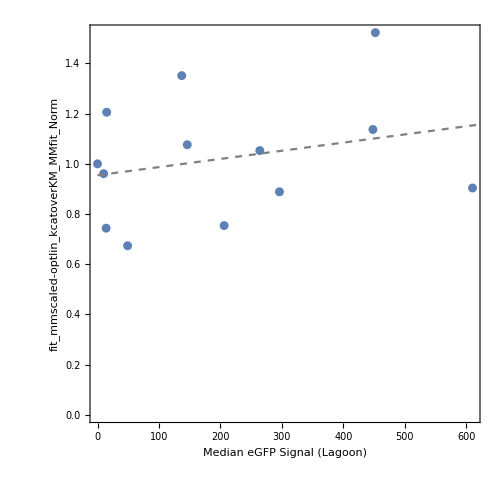

```mathematica
wtForCalc=addedLagoonIntensities[Select[#ExpIndex==1&&#MutantID=="WT"&&#EnzymeConc>0.3&&#ManualGFPFlag==0&]];

(*parameter="fit_mmscaled-optlin_kcatMMfit";*)
parameter="fit_mmscaled-optlin_kcatoverKM_MMfit";

forCorr=Values[Normal[wtForCalc[All,{"LagoonMedianIntensity",parameter}]]];

medianWT=Median[forCorr[[All,2]]];

forCorrNorm=#/{1.0,medianWT}&/@forCorr;

fitLine=LinearModelFit[forCorrNorm,x,x]

Show[ListPlot[forCorrNorm,AspectRatio->1,ImageSize->500,ImagePadding->{{75,75},{75,0}},Frame->True,Axes->False,FrameStyle->Directive[Black,16],FrameLabel->{"Median eGFP Signal (Lagoon)",parameter<>"_Norm"},PlotRange->All],Plot[fitLine[x],{x,0,1 10^5},PlotStyle->Directive[Gray,Dashed]]]

addedRescaledkcat=addedLagoonIntensities[All,Append[#,"kcatoverKm_lagoon_rescaled"->(#[parameter]/(fitLine[#LagoonMedianIntensity]))]&];
```

#### 14. Correct kcat for row/column dependence:

```mathematica
fixLogPlots[gr_]:=gr/.f:(Charting`ScaledTicks|Charting`ScaledFrameTicks)[{Log,Exp}]:>(Part[#,;;, ;;3]&@*f)

chipCorrection[datasetForCorrection_]:=Module[{pairs},

dataset=datasetForCorrection;

cmup1=dataset[Select[#ExpIndex==whichExpt&&#EnzymeConc>0.3&&#ManualGFPFlag==0&&#LocalBackgroundRatio>5.0&]];

groupedByMutant=cmup1[GroupBy["MutantID"]];

pairs=groupedByMutant[Select[Length[#]≥2&]];

test1=Table[Values[Normal[pairs[n][All,{"MutantID","Indices","kcatoverKm_lagoon_rescaled","fit_mmscaled-optlin_kcatoverKM_MMfit"}]]],{n,1,Length[pairs]}];

(* RMSE across replicates, kcat_lagoon_rescaled *)
rmse=Sqrt[Sum[Sum[(test1[[n,i,4]]-Mean[test1[[n]][[All,4]]])^2,{i,1,Length[test1[[n]]]}],{n,1,Length[test1]}]/Length[Flatten[test1,1]]];

(* plot wt pairs *)
wtTest=Partition[Select[test1,#[[1,1]]=="WT"&][[1]],2];

wtPairs=ListLogLogPlot[Table[Callout[{wtTest[[n,1,4]],wtTest[[n,2,4]]},wtTest[[n,1,1]]<>"_"<>ToString[wtTest[[n,1,2,1]]]<>"_"<>ToString[wtTest[[n,2,2,1]]]],{n,1,Length[wtTest]}],AspectRatio->1,PlotRange->{{1000.0,1 10^6},{1000.0,5 10^6}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"}];

corrplot1=Show[fixLogPlots@ListLogLogPlot[Table[Callout[{test1[[n,1,4]],test1[[n,2,4]]},test1[[n,1,1]]<>"_"<>ToString[test1[[n,1,2,1]]]<>"_"<>ToString[test1[[n,2,2,1]]]],{n,1,Length[test1]}],AspectRatio->1,PlotRange->{{1000.0,5 10^6},{1000.0,5 10^6}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"},Epilog->{Inset[Style["RMSE = "<>ToString[rmse],18,FontFamily->"Arial"],Scaled[{0.8,0.2}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"] = "<>ToString[Length[test1]],18,FontFamily->"Arial"],Scaled[{0.8,0.12}]]}],

wtPairs,

LogLogPlot[{x,x/2,x*2},{x,0.01,10000000.0},PlotStyle->Directive[Gray,Opacity[0.75],Dashed]],ImageSize->700];

test2Lagoon=Table[Append[test1[[n,i]],test1[[n,i,4]]/Mean[test1[[n]][[All,4]]]],{n,1,Length[test1]},{i,1,Length[test1[[n]]]}];

flattened=Flatten[test2Lagoon,1];
forHM=SparseArray[Table[{flattened[[n,2,2]],flattened[[n,2,1]]}->Log[flattened[[n,5]]],{n,1,Length[flattened]}]];

hm1=MatrixPlot[forHM,ImageSize->380,PlotLegends->BarLegend[Automatic,LegendLabel->"Ln(FractionBox[RowBox[{SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \" \"}], RowBox[{\"<\", SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \">\"}]])",LabelStyle->Directive[FontSize->18,Black,FontFamily->"Arial"]],PlotTheme->"Scientific",Mesh->All,MeshStyle->Directive[Gray,Dashed],FrameStyle->Directive[Black,Thickness[0.005],18,FontFamily->"Arial"],FrameLabel->{"Row","Column"}];

Print[GraphicsRow[{corrplot1,hm1}]];

lagoonDataIn=cmup1[Select[#MutantID=="WT"&]];

lagoonData=Values[Normal[lagoonDataIn[All,{"Indices","LagoonMedianIntensity","kcatoverKm_lagoon_rescaled","fit_mmscaled-optlin_kcatoverKM_MMfit"}]]];

(*ListPlot[Table[Callout[{lagoonData[[n,2]],lagoonData[[n,3]]},lagoonData[[n,1]]],{n,1,Length[lagoonData]}]]*)

gatheredbyColumnLagoon=Gather[Flatten[test2Lagoon,1],#1[[2,1]]==#2[[2,1]]&];

gatheredbyRowLagoon=Gather[Flatten[test2Lagoon,1],#1[[2,2]]==#2[[2,2]]&];

columnSortPostLagoon=Sort[Table[{gatheredbyColumnLagoon[[n,1,2,1]],gatheredbyColumnLagoon[[n,All,5]],Mean[gatheredbyColumnLagoon[[n,All,5]]]},{n,1,Length[gatheredbyColumnLagoon]}],#1[[3]]>#2[[3]]&];

columnSortPlot=ListPlot[Flatten[Table[{n,columnSortPostLagoon[[n,2,i]]},{n,1,Length[columnSortPostLagoon]},{i,1,Length[columnSortPostLagoon[[n,2]]]}],1],PlotStyle->Darker[Red],AspectRatio->0.5,ImageSize->600,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18],FrameLabel->{"Post-Sort Index (Column)","FractionBox[RowBox[{SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \" \"}], RowBox[{\"<\", SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \">\"}]]"}];

columnSortPlotMeans=ListPlot[Table[Callout[{n,columnSortPostLagoon[[n,3]]},columnSortPostLagoon[[n,1]]],{n,1,Length[columnSortPostLagoon]}],PlotStyle->Directive[Darker[Red],PointSize[0.02]],AspectRatio->0.5,ImageSize->600,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18],FrameLabel->{"Post-Sort Index (Column)","FractionBox[RowBox[{SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \" \"}], RowBox[{\"<\", SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \">\"}]]"}];

rowSortPostLagoon=Sort[Table[{gatheredbyRowLagoon[[n,1,2,2]],gatheredbyRowLagoon[[n,All,5]],Mean[gatheredbyRowLagoon[[n,All,5]]]},{n,1,Length[gatheredbyRowLagoon]}],#1[[3]]>#2[[3]]&];

rowSortPlot=ListPlot[Flatten[Table[{n,rowSortPostLagoon[[n,2,i]]},{n,1,Length[rowSortPostLagoon]},{i,1,Length[rowSortPostLagoon[[n,2]]]}],1],PlotStyle->Darker[Red],AspectRatio->0.5,ImageSize->600,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18],FrameLabel->{"Post-Sort Index (Row)","FractionBox[RowBox[{SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \" \"}], RowBox[{\"<\", SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \">\"}]]"}];

rowSortPlotMeans=ListPlot[Table[Callout[{n,rowSortPostLagoon[[n,3]]},rowSortPostLagoon[[n,1]]],{n,1,Length[rowSortPostLagoon]}],PlotStyle->Directive[Darker[Red],PointSize[0.02]],AspectRatio->0.5,ImageSize->600,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18],FrameLabel->{"Post-Sort Index (Row)","FractionBox[RowBox[{SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \" \"}], RowBox[{\"<\", SubscriptBox[\"k\", RowBox[{\"cat\", \",\", RowBox[{\"mutant\", \" \", StyleBox[\"i\",FontSlant->\"Italic\"]}]}]], \">\"}]]"}];

Print[GraphicsGrid[{{Show[columnSortPlot,columnSortPlotMeans,Epilog->Inset[PointLegend[{Darker[Red]},{"Column Mean"},LegendMarkers->{Graphics[Disk[Scaled[{1,1}],100]]},LegendMarkerSize->15,LabelStyle->Directive[18,FontFamily->"Arial"]],Scaled[{0.8,0.9}]]],Show[rowSortPlot,rowSortPlotMeans,Epilog->Inset[PointLegend[{Darker[Red]},{"Row Mean"},LegendMarkers->{Graphics[Disk[Scaled[{1,1}],100]]},LegendMarkerSize->15,LabelStyle->Directive[18,FontFamily->"Arial"]],Scaled[{0.8,0.9}]]]}}]];

(* associations of correction factors *)
corrMapColumn=AssociationThread[columnSortPostLagoon[[All,1]],columnSortPostLagoon[[All,3]]];
corrMapRow=AssociationThread[rowSortPostLagoon[[All,1]],rowSortPostLagoon[[All,3]]];

columnCorrectedWT=Table[{lagoonData[[n,1]],lagoonData[[n,4]]*(1/corrMapColumn[lagoonData[[n,1,1]]])},{n,1,Length[lagoonData]}];

forColumnCorrection=Flatten[test2Lagoon,1];

reGathered=Gather[Table[{forColumnCorrection[[n,1]],forColumnCorrection[[n,4]]*(1/corrMapColumn[forColumnCorrection[[n,2,1]]]),forColumnCorrection[[n,2]]},{n,1,Length[forColumnCorrection]}],#1[[1]]==#2[[1]]&];

(* plot wt pairs *)
wtColumnCorrected=Partition[Select[reGathered,#[[1,1]]=="WT"&][[1]],2];

(* RMSE across replicates, kcat_column_corrected *)
rmse2=Sqrt[Sum[Sum[(reGathered[[n,i,2]]-Mean[reGathered[[n]][[All,2]]])^2,{i,1,Length[reGathered[[n]]]}],{n,1,Length[reGathered]}]/Length[Flatten[reGathered,1]]];

wtPairsColumnCorrected=ListLogLogPlot[Table[Callout[{wtColumnCorrected[[n,1,2]],wtColumnCorrected[[n,2,2]]},"WT"],{n,1,Length[wtTest]}],AspectRatio->1,PlotStyle->Darker[Red],PlotRange->{{1000.0,5 10^6},{1000.0,5 10^6}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"}];

rowCorrectedWT=Table[{lagoonData[[n,1]],columnCorrectedWT[[n,2]]*(1/corrMapRow[columnCorrectedWT[[n,1,2]]])},{n,1,Length[lagoonData]}];

Print[GraphicsRow@{Histogram[{lagoonData[[All,4]],columnCorrectedWT[[All,2]]},{10^5},PlotRange->{{0,All},All},ImageSize->450,Frame->True,Axes->False,PlotLabel->Style["Wild-type Dist. After Column Correction",Black,18,FontFamily->"Arial"],FrameStyle->Directive[Black,Thickness[0.0025],18],FrameLabel->{"k_cat/K_M (/M/s)","Counts"}],

Histogram[{lagoonData[[All,4]],rowCorrectedWT[[All,2]]},{10^5},PlotRange->{{0,All},All},PlotRange->{{0,All},All},PlotLabel->Style["Wild-type Dist. After Column & Row Correction",Black,18,FontFamily->"Arial"],ImageSize->450,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18],FrameLabel->{"k_cat/K_M (/M/s)","Counts"}]}];

forRowCorrection=Flatten[reGathered,1];

reGatheredRow=Gather[Table[{forRowCorrection[[n,1]],forRowCorrection[[n,2]]*(1/corrMapRow[forRowCorrection[[n,3,2]]]),forRowCorrection[[n,3]]},{n,1,Length[forRowCorrection]}],#1[[1]]==#2[[1]]&];

(* plot wt pairs *)
wtRowCorrected=Partition[Select[reGatheredRow,#[[1,1]]=="WT"&][[1]],2];

wtPairsRowCorrected=ListLogLogPlot[Table[Callout[{wtRowCorrected[[n,1,2]],wtRowCorrected[[n,2,2]]},"WT"],{n,1,Length[wtRowCorrected]}],AspectRatio->1,PlotStyle->Darker[Red],PlotRange->{{1000.0,5 10^6},{1000.0,5 10^6}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"}];

(* RMSE across replicates, kcat_row_corrected *)
rmse3=Sqrt[Sum[Sum[(reGatheredRow[[n,i,2]]-Mean[reGatheredRow[[n]][[All,2]]])^2,{i,1,Length[reGatheredRow[[n]]]}],{n,1,Length[reGatheredRow]}]/Length[Flatten[reGatheredRow,1]]];

legend=SwatchLegend[{Directive[ColorData[97][1],Opacity[0.3]],Darker[Red]},{"Uncorrected","Corrected"},LabelStyle->Directive[18,FontFamily->"Arial"],LegendMarkerSize->20];

Print[GraphicsRow@{Show[fixLogPlots@ListLogLogPlot[Table[Callout[{reGathered[[n,1,2]],reGathered[[n,2,2]]},reGathered[[n,1,1]]],{n,1,Length[reGathered]}],PlotLabel->Style["After Column Correction",Black,18,FontFamily->"Arial"],AspectRatio->1,PlotRange->{{1000.0,5 10^6},{1000.0,5 10^6}},PlotStyle->Darker[Red],Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"},Epilog->{Inset[Style["RMSE = "<>ToString[rmse2],18,FontFamily->"Arial"],Scaled[{0.8,0.2}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"] = "<>ToString[Length[test1]],18,FontFamily->"Arial"],Scaled[{0.8,0.12}]],Inset[legend,Scaled[{0.2,0.8}]]}],

wtPairsColumnCorrected,

ListLogLogPlot[Table[{test1[[n,1,4]],test1[[n,2,4]]},{n,1,Length[test1]}],AspectRatio->1,PlotStyle->Opacity[0.3],PlotRange->{1000.0,5 10^6},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"}],

LogLogPlot[{x,x/2,x*2},{x,0.01,10000000.0},PlotStyle->Directive[Gray,Opacity[0.75],Dashed]],ImageSize->700],

Show[fixLogPlots@ListLogLogPlot[Table[Callout[{reGatheredRow[[n,1,2]],reGatheredRow[[n,2,2]]},reGatheredRow[[n,1,1]]],{n,1,Length[reGatheredRow]}],AspectRatio->1,PlotLabel->Style["After Column & Row Correction",Black,18,FontFamily->"Arial"],PlotRange->{{1000.0,5 10^6},{1000.0,5 10^6}},PlotStyle->Darker[Red],Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"},Epilog->{Inset[Style["RMSE = "<>ToString[rmse3],18,FontFamily->"Arial"],Scaled[{0.8,0.2}]],Inset[Style["StyleBox[\"n\",FontSlant->\"Italic\"] = "<>ToString[Length[test1]],18,FontFamily->"Arial"],Scaled[{0.8,0.12}]],Inset[legend,Scaled[{0.2,0.8}]]}],

wtPairsRowCorrected,

ListLogLogPlot[Table[{test1[[n,1,4]],test1[[n,2,4]]},{n,1,Length[test1]}],AspectRatio->1,PlotStyle->Opacity[0.3],PlotRange->{{1000.0,5 10^6},{1000.0,5 10^6}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025],18,FontFamily->"Arial"],FrameLabel->{"k_cat/K_(M,rep1) (/M/s)","k_cat/K_(M,rep2) (/M/s)"}],

LogLogPlot[{x,x/2,x*2},{x,0.01,10000000.0},PlotStyle->Directive[Gray,Opacity[0.75],Dashed]],ImageSize->700]}];

(* correct all mutants (including those without replicates *)

allMutants=Values[Normal[cmup1[All,{"MutantID","Indices","kcatoverKm_lagoon_rescaled","fit_mmscaled-optlin_kcatoverKM_MMfit"}]]];

allColumnCorrected=Table[{allMutants[[n,1]],allMutants[[n,4]]*(1/corrMapColumn[allMutants[[n,2,1]]]),allMutants[[n,2]]},{n,1,Length[allMutants]}];

allRowCorrected=Table[{allColumnCorrected[[n,1]],allColumnCorrected[[n,2]]*(1/corrMapRow[allColumnCorrected[[n,3,2]]]),allColumnCorrected[[n,3]]},{n,1,Length[allColumnCorrected]}];

out1=allRowCorrected;
out2=Table[Association[{"Indices"->out1[[n,3]],"kcat/Km_chip_corrected"->out1[[n,2]]}],{n,1,Length[out1]}];

appended=Dataset[JoinAcross[Normal[dataset],out2,"Indices","Left"]]

]
```

-Graphics-

-Graphics-

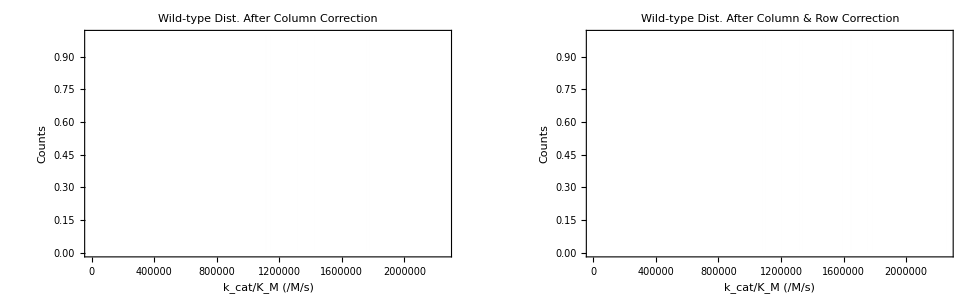

-Graphics-

```mathematica
outCorrected=chipCorrection[addedRescaledkcat];
```

## Export data:

These cells export data to wxf format (dataset format which includes all data, plots, and symbolic output) and csv format (text format of data and fitted parameters). In practice, both formats are useful and both should be exported. The dataset format allows for subsequent calculations without having to re-read in and process data, while the csv files are much smaller and contain the key fitted parameters for making interpretive plots, etc.

#### 15. Export aggregate dataset:

```mathematica
outName="180314_S3d1_PafA_ValScan_MeP";

Export[StringJoin["/Users/craig/Desktop/",outName,".wxf"],addedEnzymeConc,PerformanceGoal->"Size"]
```

/Users/craig/Desktop/180314_S3d1_PafA_ValScan_MeP.wxf

#### 15a. Export CSV of all compatible data types (string, integer, list, real):

```mathematica
normalizedDataset=Normal[outCorrected];

replaced=Fold[Replace[#1,#2,Infinity]&,normalizedDataset,{_FittedModel->"NaN",_Graphics->"NaN",_Image->"NaN",_NonlinearModelFit->"NaN",_Times->"NaN",_Overlay->"NaN",_ReplaceAll->"NaN"}];

headers=Keys[replaced[[1]]];

(*values=Map[replaceBracketsBack,Values[replaced],{2}];*)

values=Values[replaced];

datasetForExport=Prepend[values,headers];

Export[StringJoin["/Users/craig/Desktop/",outName,".csv.bz2"],datasetForExport,"Data"]
```

ReplaceAll::reps: {5.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14804933={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14804933).((offset+Times[«3»])-Optimization`FindFit`y$14804933)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14804933={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14804987={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14804987).((offset+Times[«3»])-Optimization`FindFit`y$14804987)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14804987={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14805035={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14805035).((offset+Times[«3»])-Optimization`FindFit`y$14805035)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14805035={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

ReplaceAll::reps: {5.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

ReplaceAll::reps: {5.,Indeterminate} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14832197={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14832197).((offset+Times[«3»])-Optimization`FindFit`y$14832197)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14832197={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14832247={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14832247).((offset+Times[«3»])-Optimization`FindFit`y$14832247)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14832247={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14832295={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14832295).((offset+Times[«3»])-Optimization`FindFit`y$14832295)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14832295={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14838645={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14838645).((offset+Times[«3»])-Optimization`FindFit`y$14838645)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14838645={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14838695={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14838695).((offset+Times[«3»])-Optimization`FindFit`y$14838695)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14838695={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14838743={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14838743).((offset+Times[«3»])-Optimization`FindFit`y$14838743)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14838743={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14848293={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14848293).((offset+Times[«3»])-Optimization`FindFit`y$14848293)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14848293={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14848343={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14848343).((offset+Times[«3»])-Optimization`FindFit`y$14848343)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14848343={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {Vmax,KM,offset} = {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[Block[{substrate={0.,5.,10.,20.,35.,50.},Optimization`FindFit`y$14848391={Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},1/2 ((offset+Times[«3»])-Optimization`FindFit`y$14848391).((offset+Times[«3»])-Optimization`FindFit`y$14848391)]],Block},{0,{{{},1,0,Hold[Vmax],0,0},{{},1,1,Hold[KM],0,0},{{},1,2,Hold[offset],0,0}}},«1»,«1»,{904,MachinePrecision,{None,{Hold[Block[{substrate={«6»},Optimization`FindFit`y$14848391={«6»}},1/2 Subtract[«2»].Subtract[«2»]]],Block}},True,{{Automatic,CleanUpRegisters→False,WarningMessages→False,EvaluateSymbolically→False,RuntimeErrorHandler→($Failed&)},{},Automatic,WVM},NonlinearModelFit,Automatic,None},{None,None,None}] failed at {1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::grad will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{{0.,Indeterminate},{5.,Indeterminate},{10.,Indeterminate},{20.,Indeterminate},{35.,Indeterminate},{50.,Indeterminate}},{offset+(substrate Vmax)/(KM+substrate),KM>0&&Vmax>0&&offset>0},{Vmax,KM,offset},substrate][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

/Users/craig/Desktop/180314_S3d1_PafA_ValScan_MeP.csv.bz2

## PDF export:

#### 15b. Generate summary PDF pages:

Individual PDF pages are output to a working directory. Stitching of PDFs is done using an external python session running PyPDF2.

```mathematica
dataset=Import["/Users/craig/Desktop/180314_S3d1_PafA_ValScan_MeP.wxf"];
```

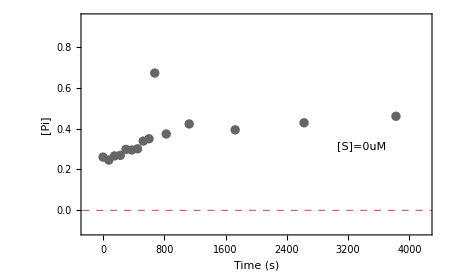
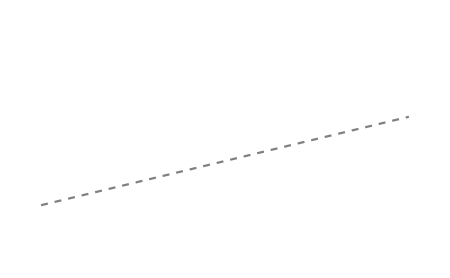
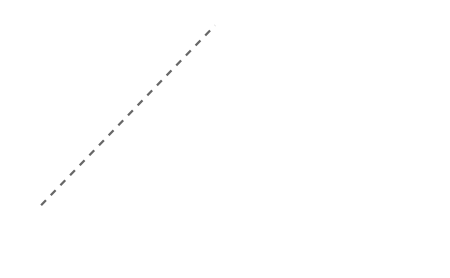
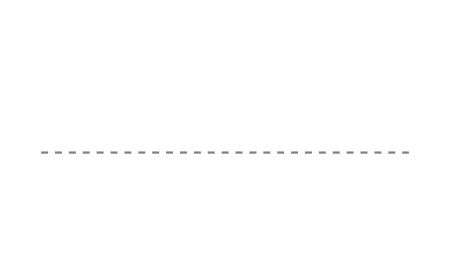
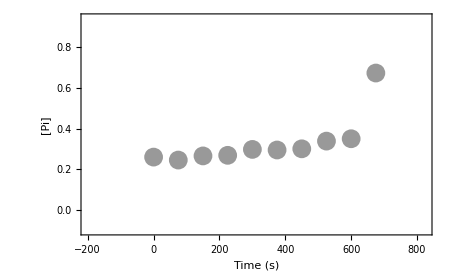
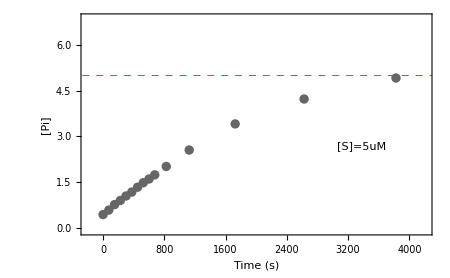
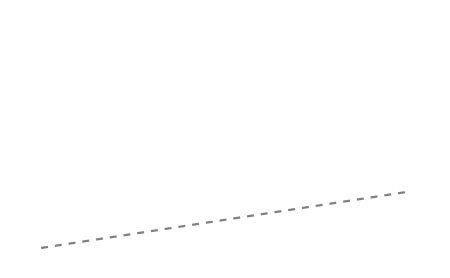
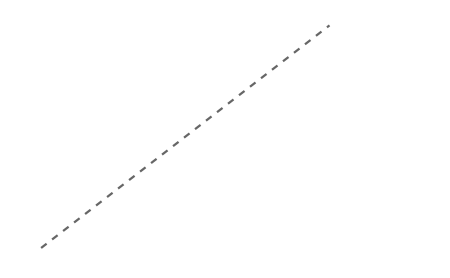
-Graphics- | Mutant | Substrate | Chamber | k_cat^(Michaelis - Menten) (s^-1) | K_M^(Michaelis - Menten) (uM) | k_cat/K_M^(Michaelis - Menten) (M^-1 s^-1) | y-int^(Michaelis - Menten) (s^-1) | K_I (uM) | LocalBGRatios | R^2 (Michaelis-Menten fit) | [E] | eGFP Intensity
 | K105V | MeP | {3,14} | 252.929 | 83.4311 | 3.03159×10^6 | 0.00575201 | NaN | 9.81309 | 0.976217 | 0.16353 | 16353
-Graphics- |  | -Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics--Graphics--Graphics- |  |  |  |  |  |  |  |  |  |

```mathematica
makeGrid[dataset,{3,14},"MeP"]
```

```mathematica
indices=Sort[Normal[DeleteDuplicates[dataset[[All,"Indices"]]]]];

Dynamic[n]

Do[

(* change 3rd argument to correspond to type of assay: cMUP, MeP, MecMUP, Inhibition *)
out=makeGrid[dataset,indices[[n]],"MeP"];

Export[StringJoin["/Users/craig/Documents/Biochemistry/AP_enzymology/MITOMI/tempPDF/temporary_PDF_",StringPadLeft[ToString[n],4,"0"],".pdf"],out,"AllowRasterization"->False];
,{n,1,1568}]
```

ReplaceAll::reps: {Indeterminate[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gtype: Symbol is not a type of graphics.

ReplaceAll::reps: {Indeterminate[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gtype: Symbol is not a type of graphics.

ReplaceAll::reps: {Indeterminate[BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Show::gtype: Symbol is not a type of graphics.

General::stop: Further output of Show::gtype will be suppressed during this calculation.

#### 15c. Join PDFs:

```mathematica
session = StartExternalSession[<|"System"->"Python","Version"->"3.6", "SessionProlog"->{"import os", "from PyPDF2 import PdfFileMerger, PdfFileReader"}|>]

defineRoot = "root='/Users/craig/Documents/Biochemistry/AP_enzymology/MITOMI/tempPDF/'";
getNames = "pdfs1=[os.path.join(root, dir) for dir in os.listdir(root) if '.pdf' in dir]";
getNames2="pdfs=sorted(pdfs1)";
createMerger = "merger = PdfFileMerger()";
executeMerge = "for pdf in pdfs: merger.append(PdfFileReader(pdf,'rb'))";
executeExport = StringJoin["merger.write('/Users/craig/Desktop/",Values[Normal[dataset[1,{"GlobalExperimentIndex"}]]][[1]],".pdf')"];
completionNotice = "print('PDF Concatenation Complete')";
```

selected::shdw: Symbol selected appears in multiple contexts {WebUnit`WebDriverAPI`,Global`}; definitions in context WebUnit`WebDriverAPI` may shadow or be shadowed by other definitions.

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session,{defineRoot, getNames,getNames2, createMerger, executeMerge, executeExport, completionNotice}]
```

PDF Concatenation Complete

{Null,Null,Null,Null,Null,Null,Null}